## Common elements

```mathematica
(* Load HEPMath package *)
Needs["HEPMath`"]
normKinVars={s-> sp+q2,s4-> sp+t1+u1,t-> t1+m2,u1p->u1-q2};
physAssump={m2>0,q2<0,s>0,sp>0,t1<0,u1<0,sp+t1+u1>0,s4>0,
s-s4-2m2>0,sp+t1>0,s+u1>0,(s-s4)^2-4m2 s>0,(sp+u1p)^2-4q2 t>0,
(* ?Marco *)(q2*s4-s*u1)>0,(q2*s4+4*m2*(q2-s-t1)-s*u1)>0(* ? *)
}/.normKinVars;

physParameterPoints={
{q2->-5,u1->-25,t1->-15,sp->115,m2->0.5},
{q2->-5,u1->-25,t1->-15,sp->115,m2->1.0},
{q2->-6,u1->-25,t1->-15,sp->115,m2->0.5},
{q2->-5,u1->-25,t1->-15,sp->120,m2->0.5}
};
Do[Module[{l,v},l=physAssump/.p;v=And@@l;If[Not[v],Print[p, " doesn't match assumptions: ",l]]],{p,physParameterPoints}]

(* total cross section parameters *)
ηOfs[s_]=s/(4m2)-1;
sOfη[η_]=(1+η)*(4m2);
ρOfs[s_]=4m2/s;
sOfρ[ρ_]=4m2/ρ;
βOfρ[ρ_]=Sqrt[1-ρ];
ρOfβ[β_]=1-β^2;
χOfβ[β_]=(1-β)/(1+β);
normTotalCSVars={ρ-> ρOfs[s],β-> βOfρ@ρOfs[s],η-> ηOfs[s],χ->χOfβ@βOfρ@ρOfs[s]};
showq2={χq-> (βq-1)/(1+βq),βq-> Sqrt[1-ρq],ρq-> 4m2/q2};

(* color factors *)
normColor={Kgγ-> 1/(NC^2-1),Kqγ-> 1/NC,CA->NC,CF-> (NC^2-1)/(2NC),NC-> 3};
normColor=(First@#-> (Last@#/.normColor))&/@normColor;

(* tools *)
getLinearCoefficientList[e_,logs_]:=Module[{ar,pos0,pos1,allPos},
ar=CoefficientList[e,logs];
pos0=Table[1,{Length@logs}];
pos1=pos0;
pos1[[1]]=2;
allPos=Join[{pos0},Table[RotateRight[pos1,n-1],{n,Length@logs}]];
Table[Part@@Flatten[{{ar},p},1],{p,allPos}]
];
getAllSymbols=e↦ DeleteDuplicates[Reap[Map[If[Head[#]==Symbol,Sow[#]]&,e,Infinity]][[2]][[1]]];
```

## Matrix elements

```mathematica
<<"~/Physik/PhD/MMa/data/ElProduction.Me.Born.m";
```

```mathematica
<<"~/Physik/PhD/MMa/data/ElProduction.Me.Soft.m";
<<"~/Physik/PhD/MMa/data/ElProduction.Me.Virt.m";
<<"~/Physik/PhD/MMa/data/ElProduction.Me.Hard.m";
```

```mathematica
<<"~/Physik/PhD/MMa/data/ElProduction.Me.Real.m";
```

```mathematica
<<"~/Physik/PhD/MMa/data/ElProduction.SV.m";
<<"~/Physik/PhD/MMa/data/ElProduction.Hard.m";
```

## Born γ*+g → Q+Qbar

### Total cross sections

```mathematica
Module[{f,int},
f[t1_]=Integrate[Limit[BGQED/.{Dim->4+ϵ,u1-> -t1 - sp},ϵ-> 0],t1];
int=FullSimplify[f[sp/2(β-1)] - f[sp/2(-β-1)]]/.{ (Log[sp (-1+β)]-Log[-sp (1+β)]-Log[sp (1+β)]+Log[sp-sp β])-> 2Log[χ]};
σGg=2π*int/sp^2
]
Module[{f,int},
f[t1_]=Integrate[BLQED/.{u1-> -t1 - sp},t1];
int=FullSimplify[f[sp/2(β-1)] - f[sp/2(-β-1)]]/.{ (Log[sp (-1+β)]-Log[-sp (1+β)]-Log[sp (1+β)]+Log[sp-sp β])-> 2Log[χ]};
σLg=2π*2*int/sp^2
]
σTg=σGg+1/2σLg;
Module[{f,int},
f[t1_]=Integrate[Limit[BPQED/.{Dim->4+ϵ,u1-> -t1 - sp},ϵ-> 0],t1];
int=FullSimplify[f[sp/2(β-1)] - f[sp/2(-β-1)]];
σPg=2π*int/sp^2
]
```

(2 π ((2 β (8 m2 (2 m2+q2)-sp^2 (-1+β^2)))/(-1+β^2)+2 (8 m2^2-2 q2^2-4 m2 sp-sp (2 q2+sp)) Log[χ]))/sp^3

-(16 π q2 ((q2+sp) β+2 m2 Log[χ]))/sp^3

(2 π (2 β (-8 m2+(2 q2+sp) (-1+β^2))+(2 q2+sp) (-1+β^2) (Log[sp (-1+β)]-Log[-sp (1+β)]-Log[sp (1+β)]+Log[sp-sp β])))/(sp^2 (-1+β^2))

```mathematica
FullSimplify[D[σGg//.{χ-> (1-β)/(1+β),β-> Sqrt[1-4m2/(sp+q2)]},m2]]//.{Sqrt[1-4m2/(sp+q2)]-> β,1/Sqrt[1-4m2/(sp+q2)]-> 1/β,(1-β)/(1+β)-> χ} //FullSimplify
FullSimplify[D[σLg//.{χ-> (1-β)/(1+β),β-> Sqrt[1-4m2/(sp+q2)]},m2]]//.{Sqrt[1-4m2/(sp+q2)]-> β,(1-β)/(1+β)-> χ}
```

-(4 π (-32 m2^2 (q2+sp)+2 m2 sp (4 q2+3 sp)+(q2+sp) (2 q2^2+2 q2 sp+sp^2)+4 m2 (-4 m2+sp) (q2+sp) β Log[χ]))/(m2 sp^3 (q2+sp) β)

-(32 π q2 Log[χ])/sp^3

```mathematica
Series[1/(1-4/3 x +x^2(1.0414 nl - 14.3323)),{x,0,2}]
```

1+(4 x)/3+(16.1101-1.0414 nl) x^2+O[x]^3

#### Check to Nucl.Phys.B 392-162

```mathematica
σLgref=16π(-q2 s)/sp^3 (β + 2m2/s Log[χ]);
σTref=4π/sp^3(-((s+q2)^2 + 4m2 s)β-(s^2+q2^2 + 4m2 s -8m2^2)Log[χ]);
FullSimplify[(σLgref-σLg)/.normTotalCSVars/.normKinVars,Assumptions-> {m2>0,0≤ 4m2/(sp+q2)≤ 1}]
FullSimplify[(σTref-σTg)/.normTotalCSVars/.normKinVars,Assumptions-> {m2>0,0≤ 4m2/(sp+q2)≤ 1}]
```

0

0

```mathematica
Kgγ * NC *CF/.normColor
```

1/2

#### plots

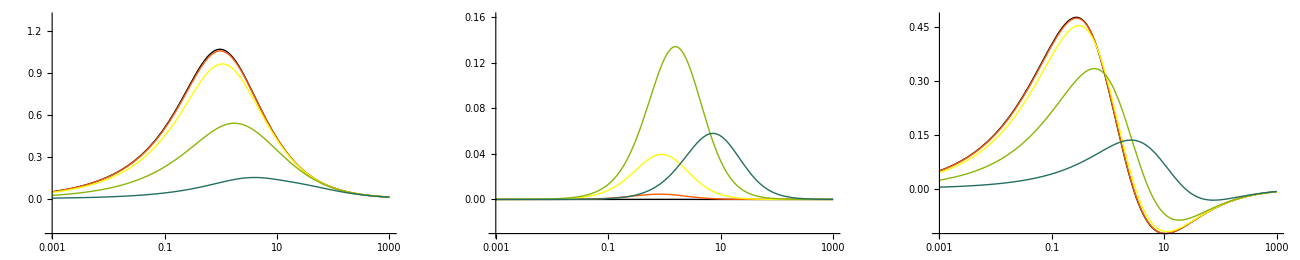

```mathematica
Module[{c0g},
c0g[var_][sV_,Q2V_,m2V_]:=Module[{sig,psNorm},
sig[T]=σTg;
sig[L]=σLg;
sig[P]=σPg;
psNorm[T]=psNorm[L]=psNorm[P]=Kgγ*NC*CF/.normColor;
(psNorm[var]*m2*(sig[var]/.normTotalCSVars/.normKinVars))//.{sp-> sV+Q2V,q2->-Q2V,m2-> m2V}
];
Show[GraphicsRow[{
LogLinearPlot[Evaluate@Table[c0g[T][sOfη@η,Q2,4.75^2],{Q2,{1*^-2,1,10,10^2,10^3}}],{η,1*^-3,1*^3},PlotRange-> {Full,{-.25,1.3}},PlotStyle->ColorData[3,"ColorList"]],
LogLinearPlot[Evaluate@Table[c0g[L][sOfη@η,Q2,4.75^2],{Q2,{1*^-2,1,10,10^2,10^3}}],{η,1*^-3,1*^3},PlotRange-> {Full,{-.03,.16}},PlotStyle->ColorData[3,"ColorList"]],
LogLinearPlot[Evaluate@Table[c0g[P][sOfη@η,Q2,4.75^2],{Q2,{1*^-2,1,10,10^2,10^3}}],{η,1*^-3,1*^3},PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]]
}],ImageSize-> 1300]
]
```

## Common NLO

```mathematica
<<"~/Physik/PhD/MMa/data/ElProduction.PsInt.m";
```

```mathematica
Module[{refG,refL,ShiftedBorn},
refG=(-(t1^2+(sp+t1)^2)/(t1(sp+t1))
+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1)) + 2sp q2/(t1 u1)-2q2^2(sp+t1)/(t1 u1^2)
-2m2 q2/(t1^2 u1^2)(t1^2 + (sp+t1)^2));
ShiftedBorn[G]=(BGQED/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1}/.{x1-> -u1/(sp+t1)};
Print@FullSimplify[refG-ShiftedBorn[G]/.{ϵ-> 0}];
refL=4q2/sp(sp t1 u1p - m2 sp^2-q2 t1^2)(sp+t1)/(sp t1 u1^2)/.normKinVars;
ShiftedBorn[L]=(BLQED/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1}/.{x1-> -u1/(sp+t1)};
Print@FullSimplify[refL-ShiftedBorn[L]/.{ϵ-> 0}];
]
```

0

0

(s (4 t1^2+sp^2 (-1+β^2)))/(4 sp t1^2)

(s (-1+β^2+√(1-β^2)))/(√(1-β^2))

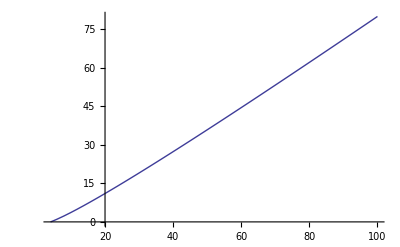

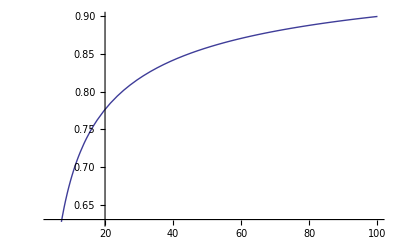

```mathematica
Module[{s4max,s4MaxVal},
s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2));
Print@Simplify@Together@D[s4max,t1];
s4MaxVal=Simplify[s4max/.{t1-> -sp/2Sqrt[1-β^2]}];
Print@s4MaxVal;
Print@Plot[s4MaxVal/.normTotalCSVars/.{m2-> 1},{s,4,100}];
Print@Plot[D[s4MaxVal/.normTotalCSVars/.{m2-> 1},s]/.{s-> sv},{sv,4,100}];
]
```

```mathematica
Module[{s4max,Mt1min,Mt1max,m2V,q2V,s4MaxVal},
s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2))/.normTotalCSVars/.normKinVars;
Mt1min=sp(1-β)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+β)/2/.normTotalCSVars/.normKinVars;
s4MaxVal=Simplify[s4max/.{t1-> -sp/2Sqrt[1-β^2]}]/.normTotalCSVars/.normKinVars;
m2V=4.74^2;
q2V=1.;
Print[{-Mt1max,-Mt1min,s4MaxVal}/.{m2-> m2V,q2-> q2V}/.{sp-> 4*m2V(1+10*^2)-q2V}];
RegionPlot3D[(sp>4m2 && -Mt1max<t1<-Mt1min && s4 < s4max)//.{m2-> m2V,q2-> q2V,sp-> 4m2(1+Exp[lnη])-q2V},{lnη,-2,2},{t1,-1000,-20},{s4,0,500},AxesLabel->Automatic]
]
```

{-89936.8,-22.473,87116.9}

-Graphics3D-

1/2 sp (√((-4 m2+q2+sp)/(q2+sp)) (q2+sp-2 Δ)+2 m2 Log[(1-√(1-(4 m2)/(q2+sp)))/(1+√(1-(4 m2)/(q2+sp)))])

-1/2 (√(1/m2) (4 m2-q2) Δ) √(s-4 m2)+1/48 (1/m2)^(3/2) (32 m2^2-8 m2 q2-12 m2 Δ-3 q2 Δ) (s-4 m2)^(3/2)+((1/m2)^(5/2) (448 m2^2+48 m2 q2+60 m2 Δ+45 q2 Δ) (s-4 m2)^(5/2))/3840+((1/m2)^(7/2) (-416 m2^2-120 m2 q2-140 m2 Δ-175 q2 Δ) (s-4 m2)^(7/2))/71680+O[s-4 m2]^(9/2)

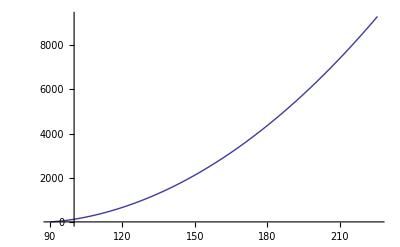

```mathematica
Module[{s4max,Mt1min,Mt1max,A},
s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2))/.normTotalCSVars/.normKinVars;
Mt1min=sp(1-β)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+β)/2/.normTotalCSVars/.normKinVars;
A=Integrate[Integrate[1,{s4,Δ,s4max}],{t1,-Mt1max,-Mt1min},Assumptions-> {0<4m2< q2+sp,sp>0,Δ>0}];
Print[A];
Print@Series[A/.{sp-> s-q2},{s,4m2,4}];
Plot[A//.{m2-> 4.75^2,q2-> 1.,Δ-> 1*^-6},{sp,4.*4.75^2,10*4.75^2}]
]
```

## NLO γ*+q → Q+Qbar+q

### ∫ A1 dΩ_n

#### Compute

```mathematica
(* build integrals *)
getPsIA1[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psI[1/Times@@({tp,u7}^({3,3}-path))]],coeff,{2}];
getPsIA1k2[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psIk2[1/Times@@({tp,u7}^({3,3}-path))]],coeff,{2}];
psIAG1=getPsIA1[CoeffAG1];
psIAL1=getPsIA1[CoeffAL1];
psIAP1k0=getPsIA1[CoeffAP1k0];
psIAP1k2=getPsIA1k2[CoeffAP1k2];
psLogsA1={psLog2[S1][u7],psLog3[S1][u7]};
```

```mathematica
(* compute pole terms *)
IntAG1pole =Expand@Total[Coefficient[CoeffAG1,ϵ,0]*Coefficient[psIAG1,ϵ,-1],2];
IntAL1pole =Expand@Total[Coefficient[CoeffAL1,ϵ,0]*Coefficient[psIAL1,ϵ,-1],2];
IntAP1pole =Expand@Total[Coefficient[CoeffAP1k0,ϵ,0]*Coefficient[psIAP1k0,ϵ,-1],2];
(* compute finite terms *)
IntAG1finite =Expand@Total[Coefficient[CoeffAG1,ϵ,0]*Coefficient[psIAG1,ϵ,0],2]+Expand@Total[Coefficient[CoeffAG1,ϵ,1]*Coefficient[psIAG1,ϵ,-1],2];
IntAL1finite =Expand@Total[Coefficient[CoeffAL1,ϵ,0]*Coefficient[psIAL1,ϵ,0],2]+Expand@Total[Coefficient[CoeffAL1,ϵ,1]*Coefficient[psIAL1,ϵ,-1],2];
IntAP1finite =Expand@Total[Coefficient[CoeffAP1k0,ϵ,0]*Coefficient[psIAP1k0,ϵ,0],2]+Expand@Total[Coefficient[CoeffAP1k0,ϵ,1]*Coefficient[psIAP1k0,ϵ,-1],2]+Expand@Total[Coefficient[CoeffAP1k2,ϵ,0]*Coefficient[psIAP1k2,ϵ,0],2];
```

#### check to Nucl.Phys.B 392-162

```mathematica
IntAG1poleref=((sp+t1)/u1^2 )*((s4^2+(sp+t1)^2)/(sp+t1)^2)*(
-(t1^2+(sp+t1)^2)/(t1(sp+t1))
+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1)) + 2sp q2/(t1 u1)-2q2^2(sp+t1)/(t1 u1^2)
-2m2 q2/(t1^2 u1^2)(t1^2 + (sp+t1)^2)
);
IntAL1poleref = (sp+t1)^3/u1^4(s4^2+(sp+t1)^2)/(sp+t1)^2 4q2/sp^2*(sp t1 (u1-q2) - m2 sp^2 - q2 t1^2)/t1/(sp+t1);

FullSimplify[((IntAG1pole)/IntAG1poleref)/.normKinVars]
FullSimplify[((IntAG1pole*s4/(8π(s4+m2)))- IntAG1poleref)/.normKinVars]
FullSimplify[((IntAL1pole)/IntAL1poleref)/.normKinVars]
FullSimplify[(IntAL1pole*s4/(8π(s4+m2))-IntAL1poleref)/.normKinVars]
```

(8 π (m2+sp+t1+u1))/(sp+t1+u1)

0

(8 π (m2+sp+t1+u1))/(sp+t1+u1)

0

```mathematica
Module[{IntAG1poleRestref,diff},
IntAG1poleRestref=-((sp+t1)/u1^2 )*((s4^2+(sp+t1)^2)/(sp+t1)^2)*(
-2+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1))-4m2 q2/(t1 u1^2)(sp+t1)
)
-(t1^2+(sp+t1)^2)/(t1(sp+t1)^2);
diff=(s4/((s4+m2)4π))*Total[Coefficient[Take[CoeffAG1,2],ϵ,1]*Coefficient[Take[psIAG1,2],ϵ,-1],2];
(*Print@Simplify@Expand[diff/.normKinVars];
Print@Simplify@Expand[(IntAG1poleRestref)/.normKinVars];
Print@Simplify@Expand[(IntAG1poleref)/.normKinVars];*)
Print@Simplify@Expand[((IntAG1poleref+IntAG1poleRestref)-diff)/.normKinVars];
]
```

0

#### Check to Marco

```mathematica
Marco`IntAG1= << "~/Physik/PhD/Marco/recalc/data/IntAG1";
Marco`IntAL1= << "~/Physik/PhD/Marco/recalc/data/IntAL1";
```

```mathematica
(* pole *)
Simplify[((Coefficient[Marco`IntAG1,eps,-1]/4)-(IntAG1pole))/.normKinVars]
Simplify[((Coefficient[Marco`IntAL1,eps,-1]/4)-(IntAL1pole))/.normKinVars]
```

0

0

```mathematica
(* detect logs for replacement *)
DeleteDuplicates[Reap[Coefficient[Marco`IntAG1,eps,0]/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
DeleteDuplicates[Reap[Coefficient[Marco`IntAL1,eps,0]/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
```

{((m2+s4) t1^2 u1^2)/((-q2+s+t1)^2 (q2 s4 t1+m2 (-q2+s+u1)^2)),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 m2 q2+s^2-4 q2 s4+2 s u1+u1^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 m2 q2+s^2-4 q2 s4+2 s u1+u1^2)))}

{((m2+s4) t1^2 u1^2)/((-q2+s+t1)^2 (q2 s4 t1+m2 (-q2+s+u1)^2)),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 m2 q2+s^2-4 q2 s4+2 s u1+u1^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 m2 q2+s^2-4 q2 s4+2 s u1+u1^2))),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2)))}

```mathematica
(* finite terms *)
Module[{me,marco,diff},
Marco`IntAG1finite=(Coefficient[Marco`IntAG1,eps,0]/4/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=CoefficientList[IntAG1finite/.normKinVars,psLogsA1];
marco=CoefficientList[Marco`IntAG1finite,psLogsA1];
diff=Simplify[(me-marco)]
]
Module[{me,marco,diff},
Marco`IntAL1finite=(Coefficient[Marco`IntAL1,eps,0]/4/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=CoefficientList[IntAL1finite,psLogsA1]/.normKinVars;
marco=CoefficientList[Marco`IntAL1finite,psLogsA1];
diff=Simplify[(me-marco)]
]
```

{{0,0},{0,0}}

{{0,0},{0,0}}

### ∫ A2 dΩ_n

#### Compute

```mathematica
(* build integrals *)
getPsIA2[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psI[1/Times@@({s5,up}^({3,3}-path))]],coeff,{2}];
psIAG2=getPsIA2[CoeffAG2];
psIAL2=getPsIA2[CoeffAL2];
psIAP2=getPsIA2[CoeffAP2];
psLogsA2={psLog3[S1][up],psLog3[S1][s5],psLog4[S1][tpsp,up],psLog4[S1][tpsp,s5]};
```

```mathematica
(* compute finite terms *)
IntAG2finite =Expand[Total[Coefficient[CoeffAG2,ϵ,0]*Coefficient[psIAG2,ϵ,0],2]/.normKinVars];
IntAL2finite =Expand[Total[Coefficient[CoeffAL2,ϵ,0]*Coefficient[psIAL2,ϵ,0],2]/.normKinVars];
IntAP2finite =Expand[Total[Coefficient[CoeffAP2,ϵ,0]*Coefficient[psIAP2,ϵ,0],2]/.normKinVars];

IntAG2finiteCoeffs=getLinearCoefficientList[IntAG2finite,psLogsA2];
IntAL2finiteCoeffs=getLinearCoefficientList[IntAL2finite,psLogsA2];
IntAP2finiteCoeffs=getLinearCoefficientList[IntAP2finite,psLogsA2];
```

#### Check to Marco

```mathematica
Marco`IntAG2= << "~/Physik/PhD/Marco/recalc/data/IntAG2";
Marco`IntAL2= << "~/Physik/PhD/Marco/recalc/data/IntAL2";
```

```mathematica
(* detect logs for replacement *)
DeleteDuplicates[Reap[Marco`IntAG2/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
DeleteDuplicates[Reap[Marco`IntAL2/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
```

{(2 m2 s+(s+√(-4 m2 s+(s-s4)^2)-s4) s4)/(2 m2 s-s4 (-s+√(-4 m2 s+(s-s4)^2)+s4)),(m2 (q2-s))/(m2 (q2-s)+s4 t1),((q2-s) (m2 q2+s4 t1))/(q2 (m2 (q2-s)+s4 t1)),(2 m2 q2+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 q2-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2)))}

{(2 m2 s+(s+√(-4 m2 s+(s-s4)^2)-s4) s4)/(2 m2 s-s4 (-s+√(-4 m2 s+(s-s4)^2)+s4)),(m2 (q2-s))/(m2 (q2-s)+s4 t1),((q2-s) (m2 q2+s4 t1))/(q2 (m2 (q2-s)+s4 t1)),(2 m2 q2+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 q2-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2)))}

```mathematica
(* finite terms *)
Module[{me,marco,logs,diff},
logs=psLogsA2;
Marco`IntAG2finite=(Marco`IntAG2/4/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=IntAG2finiteCoeffs;
marco=getLinearCoefficientList[Marco`IntAG2finite,logs];
diff=Simplify[(me-marco)];
Print@diff;

Marco`IntAL2finite=(Marco`IntAL2/4/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=IntAL2finiteCoeffs;
marco=getLinearCoefficientList[Marco`IntAL2finite,logs];
diff=Simplify[(me-marco)];
Print@diff;
]
```

{0,0,0,0,0}

{0,0,0,0,0}

### ∫ A3 dΩ_n

```mathematica
(* build integrals *)
getPsIA3[coeff_] := MapIndexed[{e,path}↦If[e===0,0,psI[1/Times@@({tp,u7,s5,up}^({2,2,2,2}-path))]],coeff,{4}];
psIAG3=getPsIA3[CoeffAG3];
psIAL3=getPsIA3[CoeffAL3];
psIAP3=getPsIA3[CoeffAP3];
psLogsA3={psLog2[S1][u7],psLog2[S1][s5],psLog2[S1][up],psLog3[S1][u7],psLog3[S1][s5],psLog3[S1][up],psLog4[S1][tpsp,s5],psLog4[S1][tpsp,up],psLog4[S2][u7,s5]};
```

```mathematica
(* check poles vanish *)
Module[{f,g0,g1,h},
h[ar_,pos_]:=Part@@Flatten[{{ar},{2,2,2,2}-pos},1];
f[l_]:=Select[l,First@#≥1&];
g0[l_,coeffs_,ints_]:=Sum[Coefficient[h[coeffs,e],ϵ,0]*Coefficient[h[ints,e],ϵ,-1],{e,f@l}];
g1[l_,coeffs_,ints_]:=Sum[Coefficient[h[coeffs,e],ϵ,1]*Coefficient[h[ints,e],ϵ,-1],{e,f@l}];
Print[(gj↦Simplify[gj@@{AG3List,CoeffAG3,psIAG3}/.normKinVars])/@{g0,g1}];
Print[(gj↦Simplify[gj@@{AL3List,CoeffAL3,psIAL3}/.normKinVars])/@{g0,g1}];
Print[(gj↦Simplify[gj@@{AP3List,CoeffAP3,psIAP3}/.normKinVars])/@{g0,g1}];
]
```

{0,0}

{0,0}

{0,0}

```mathematica
(* compute finite terms *)
IntAG3finite =Expand@Total[Coefficient[CoeffAG3,ϵ,0]*Coefficient[psIAG3,ϵ,0],4];
IntAL3finite =Expand@Total[Coefficient[CoeffAL3,ϵ,0]*Coefficient[psIAL3,ϵ,0],4];
IntAP3finite =Expand@Total[Coefficient[CoeffAP3,ϵ,0]*Coefficient[psIAP3,ϵ,0],4];
```

#### Check to Marco

```mathematica
Marco`IntAG3= (<< "~/Physik/PhD/Marco/recalc/data/IntAG3");
Marco`IntAL3= (<< "~/Physik/PhD/Marco/recalc/data/IntAL3");
```

```mathematica
(* detect logs for replacement *)
DeleteDuplicates[Reap[Marco`IntAG3/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
DeleteDuplicates[Reap[Marco`IntAL3/.{Log[x_]:> Log[Sow[x]]}][[2]][[1]]]
```

{(2 m2 s+(s+√(-4 m2 s+(s-s4)^2)-s4) s4)/(2 m2 s-s4 (-s+√(-4 m2 s+(s-s4)^2)+s4)),(m2 (q2-s))/(m2 (q2-s)+s4 t1),((q2-s) (m2 q2+s4 t1))/(q2 (m2 (q2-s)+s4 t1)),((m2+s4) (q2 s4-s u1)^2)/(m2 s^2 (-q2+s+t1)^2),((m2+s4) t1^2 u1^2)/((-q2+s+t1)^2 (q2 s4 t1+m2 (-q2+s+u1)^2)),((m2+s4) (2 q2^2+s s4-q2 (2 (s+t1)+u1))^2)/(q2 (-q2+s+t1)^2 (m2 q2+s4 t1)),(2 m2 q2+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 q2-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2))),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2))),(2 m2 s (-q2+s+u1)+s4 (-q2 s+2 q2 s4-s4 u1-√(4 m2 s (q2-u1) (-2 q2+s+u1)+(q2 s-2 q2 s4+s4 u1)^2)))/(2 m2 s (-q2+s+u1)+s4 (-q2 s+2 q2 s4-s4 u1+√(4 m2 s (q2-u1) (-2 q2+s+u1)+(q2 s-2 q2 s4+s4 u1)^2)))}

{(2 m2 s+(s+√(-4 m2 s+(s-s4)^2)-s4) s4)/(2 m2 s-s4 (-s+√(-4 m2 s+(s-s4)^2)+s4)),(m2 (q2-s))/(m2 (q2-s)+s4 t1),((q2-s) (m2 q2+s4 t1))/(q2 (m2 (q2-s)+s4 t1)),((m2+s4) (q2 s4-s u1)^2)/(m2 s^2 (-q2+s+t1)^2),((m2+s4) t1^2 u1^2)/((-q2+s+t1)^2 (q2 s4 t1+m2 (-q2+s+u1)^2)),((m2+s4) (2 q2^2+s s4-q2 (2 (s+t1)+u1))^2)/(q2 (-q2+s+t1)^2 (m2 q2+s4 t1)),(2 m2 q2+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 q2-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2))),(2 m2 (q2-s-u1)+s4 (2 q2-s-u1+√(-4 q2 (m2+s4)+(s+u1)^2)))/(2 m2 (q2-s-u1)-s4 (-2 q2+s+u1+√(-4 q2 (m2+s4)+(s+u1)^2))),(2 m2 s (-q2+s+u1)+s4 (-q2 s+2 q2 s4-s4 u1-√(4 m2 s (q2-u1) (-2 q2+s+u1)+(q2 s-2 q2 s4+s4 u1)^2)))/(2 m2 s (-q2+s+u1)+s4 (-q2 s+2 q2 s4-s4 u1+√(4 m2 s (q2-u1) (-2 q2+s+u1)+(q2 s-2 q2 s4+s4 u1)^2)))}

```mathematica
Simplify[Coefficient[Marco`IntAG3,eps,-1]/.normKinVars]
Simplify[Coefficient[Marco`IntAL3,eps,-1]/.normKinVars]
```

0

0

```mathematica
(* finite terms *)
Module[{logs,me,marco,diff},
(* all logs appear as single element -> linearize *)
logs=psLogsA3;

Marco`IntAG3finite=(Coefficient[Marco`IntAG3,eps,0]/16/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=getLinearCoefficientList[Expand@IntAG3finite/.normKinVars,logs];
marco=getLinearCoefficientList[Expand@Marco`IntAG3finite,logs];
diff=Simplify[(me-marco)];
Print@diff;

Marco`IntAL3finite=(Coefficient[Marco`IntAL3,eps,0]/16/.{Log[x_]:> getPsLog[x]}/.normKinVars);
me=getLinearCoefficientList[Expand@IntAL3finite/.normKinVars,logs];
marco=getLinearCoefficientList[Expand@Marco`IntAL3finite,logs];
diff=Simplify[(me-marco)];
Print@diff;
]
```

{0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0}

### Mass factorization

```mathematica
Module[{a,Sϵ,Pgq,
ps2to2AtNLOG,ps2to2AtNLOL,
split,BornFactor,ps2to3,x1,
shiftedBornG,shiftedBornL,shiftedBornP,massCounterG,massCounterL,massCounterP,n,
h0v,h0,h1v,h1
},
a[G]=1;
a[L]=2(1+ϵ/2);
a[P]=1;
Sϵ=(4π)^(-2-ϵ/2);

BornFactor[i_]=32 α αS eH^2 Kgγ NC CF 1/(1+ϵ/2)^2 π^3 Sϵ/Gamma[1+ϵ/2]*a[i]*(*(((t1 u1p-sp m2)sp-q2 t1^2)/(sp^2 μ2))^(ϵ/2)*)(μ2/m2)^(-ϵ/2)/.{Kgγ-> Kqγ/(2CF)};
ps2to3[i_]=64 Kqγ α αS^2 NC CF 1/(1+ϵ/2) π^3 Sϵ^2 /Gamma[1+ϵ]*a[i]*(*(((t1 u1p-sp m2)sp-q2 t1^2)/(sp^2 μ2))^(ϵ/2)*)(μ2/m2)^(-ϵ) (s4/(s4+m2))(s4^2/(s4+m2))^(ϵ/2);
(*ps2to2AtNLOG=1/2 Kqγ α αS^2 NC CF 1/(4π)^(ϵ/2)1/Gamma[1+ϵ/2]*(((t1 u1p-sp m2)sp-q2 t1^2)/(sp^2 μ2))^(ϵ/2);
ps2to2AtNLOL=2ps2to2AtNLOG;*)
Print["ps2to3[G]: ",ps2to3[G]/.{ϵ-> 0}, " ps2to3[L]: ",ps2to3[L]/.{ϵ-> 0}];
Print[];
n=CF Kqγ α αS^2 NC;
(*Print["ps2to3[G]: ",Simplify@Series[ps2to3[G]*(2π(s4+m2)/s4)4/n,{ϵ,0,1}]];
Print["BornFactor[G]: ",Simplify@Series[CF αS/2*BornFactor[G]/(eH^2 π)4/n,{ϵ,0,1}]];
Print["ps2to2AtNLOG: ",Simplify@Series[ps2to2AtNLOG 4/n,{ϵ,0,1}]];
Print["ps2to3[G]/ps2to2AtNLOG: ",Simplify[FunctionExpand@Series[FullSimplify[ps2to3[G]/ps2to2AtNLOG],{ϵ,0,1}]*(4π(s4+m2))/(s4)]];
Print[];
Print["ps2to3[L]: ",Simplify@Series[ps2to3[L]*(2π(s4+m2)/s4)2/n,{ϵ,0,1}]];
Print["BornFactor[L]: ",Simplify@Series[CF αS/2*BornFactor[L]/(eH^2 π)2/n,{ϵ,0,1}]];
Print["ps2to2AtNLOL: ",Simplify@Series[ps2to2AtNLOL 2/n,{ϵ,0,1}]];
Print["ps2to3[L]/ps2to2AtNLOL: ",Simplify[FunctionExpand@Series[FullSimplify[ps2to3[L]/ps2to2AtNLOL],{ϵ,0,1}]*(4π(s4+m2))/(s4)]];
Print[];*)
(*
Print["ps2to3[G]/BornFactor[G]: ",Simplify[FunctionExpand@Series[FullSimplify[ps2to3[G]/BornFactor[G]],{ϵ,0,1}]]];
Print["ps2to3[L]/BornFactor[L]: ",Simplify[FunctionExpand@Series[FullSimplify[ps2to3[L]/BornFactor[L]],{ϵ,0,1}]]];*)


Pgq[G][x_]= CF (1+(1-x)^2)/x;
Pgq[L][x_]= CF (1+(1-x)^2)/x;
Pgq[P][x_]= CF (2-x);
split[m_][x_]=Pgq[m][x](2/ϵ+EulerGamma-Log[4π]+Log[μF2/m2]-Log[μ2/m2]);
x1=-u1/(sp+t1);
shiftedBornG=((BornFactor[G]*(BGQED/.{Dim-> 4+ϵ}))/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1};
shiftedBornL=((BornFactor[L]*(BLQED/.{Dim-> 4+ϵ}))/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1};
shiftedBornP=((BornFactor[P]*(BPQED/.{Dim-> 4+ϵ}))/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1};
massCounterG=αS/(2π)*split[G][x1]*shiftedBornG * 1/x1*1/(sp+t1);
massCounterL=αS/(2π)*split[L][x1]*shiftedBornL * 1/x1*1/(sp+t1);
massCounterP=αS/(2π)*split[P][x1]*shiftedBornP * 1/x1*1/(sp+t1);
massCounterGpole=Simplify@SeriesCoefficient[massCounterG,{ϵ,0,-1}];
massCounterLpole=Simplify@SeriesCoefficient[massCounterL,{ϵ,0,-1}];
massCounterPpole=Simplify@SeriesCoefficient[massCounterP,{ϵ,0,-1}];

Print["check poles G: ", Simplify[massCounterGpole-x Simplify[((ps2to3[G]/.{ϵ-> 0})*eH^2IntAG1pole/.normKinVars)]]];
Print["check poles L: ", Simplify[massCounterLpole-x Simplify[((ps2to3[L]/.{ϵ-> 0})*eH^2IntAL1pole/.normKinVars)]]];
Print["check poles P: ", Simplify[massCounterPpole-x Simplify[((ps2to3[P]/.{ϵ-> 0})*eH^2IntAP1pole/.{h-> 1}/.normKinVars)]]];
Print[];

massCounterGfinite=Simplify@SeriesCoefficient[massCounterG,{ϵ,0,0}];
massCounterLfinite=Simplify@SeriesCoefficient[massCounterL,{ϵ,0,0}];

(* compute finite contributions from poles *)
(*finiteFromPolesG=FullSimplify@Limit[(ps2to3[G]*IntAG1pole*eH^2/ϵ-massCounterG)/.normKinVars,ϵ-> 0];
finiteFromPolesL=FullSimplify@Limit[(ps2to3[L]*IntAL1pole*eH^2/ϵ-massCounterL)/.normKinVars,ϵ-> 0];
finiteFromPolesP=FullSimplify@Limit[(ps2to3[P]*(IntAP1pole/.{h-> 1})*eH^2/ϵ-massCounterP)/.normKinVars,ϵ-> 0];
Print["finiteFromPolesG: ",finiteFromPolesG];
Print["finiteFromPolesL:",finiteFromPolesL];
Print["finiteFromPolesP:",finiteFromPolesP];*)
]
```

ps2to3[G]: (CF Kqγ NC s4 α αS^2)/(4 π (m2+s4)) ps2to3[L]: (CF Kqγ NC s4 α αS^2)/(2 π (m2+s4))

check poles G: (CF eH^2 Kqγ NC (2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1)) (4 m2^2 sp^2 (sp+t1)+2 m2 (sp+t1) (q2 (sp^2+2 sp t1+2 t1^2)-2 sp t1 u1)+t1 (2 q2^2 (sp+t1)^2-2 q2 sp (sp+t1) u1+(sp^2+2 sp t1+2 t1^2) u1^2)) (-1+2 x) α αS^2)/(t1^2 (sp+t1)^2 u1^4)

check poles L: (8 CF eH^2 Kqγ NC q2 (2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1)) (m2 sp^2+t1 (q2 (sp+t1)-sp u1)) (-1+2 x) α αS^2)/(sp^2 t1 u1^4)

check poles P: (CF eH^2 Kqγ NC (sp^2+2 sp t1+2 t1^2) (2 sp+2 t1+u1) (2 m2 sp^2+t1 (2 q2 (sp+t1)-sp u1)) (1-2 x) α αS^2)/(sp t1^2 (sp+t1)^2 u1^2)

#### check to Nucl.Phys.B 392-162

```mathematica
Module[{normLogs,diffG},
normLogs={Log[u_*v_]:>Log[u]+Log[v],Log[1/u_]:> -Log[u],Log[u_^v_]:> v*Log[u]};
finiteFromPolesGref=1/2Kqγ α αS^2 eH^2NC CF(
(Log[s4^2/(m2(s4+m2))]+Log[m2/μF2])(
(sp+t1)/u1^2)((s4^2+(sp+t1)^2)/(sp+t1)^2)((-(t1^2+(sp+t1)^2))/(t1(sp+t1))+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1))
+2sp q2/(t1 u1)-2q2^2(sp+t1)/(t1 u1^2)-2m2 q2/(t1^2 u1^2)(t1^2+(sp+t1)^2))
+(sp+t1)/(u1^2)((s4^2+(sp+t1)^2)/(sp+t1)^2)(4m2 sp/(t1 u1))(1-m2 sp/(t1 u1))+2(sp+t1)/(u1^2)((s4^2+(sp+t1)^2)/(sp+t1)^2)(sp q2/(t1 u1)-(m2 q2(t1^2+(sp+t1)^2)/(t1^2 u1^2))-q2^2(sp+t1)/(t1 u1^2))-(t1^2+(sp+t1)^2)/(t1(sp+t1)^2)
);
diffG=1/(4π)Kqγ α αS^2eH^2CF  NC (s4/(s4+m2))*Total[Coefficient[Take[CoeffAG1,2],ϵ,1]*Coefficient[Take[psIAG1,2],ϵ,-1],2];
finiteFromPolesLref=Kqγ α αS^2 eH^2NC CF(Log[s4^2/(m2(s4+m2))]+Log[m2/μF2]+1)*((sp+t1)^3/(u1^4))((s4^2+(sp+t1)^2)/(sp+t1)^2)(4q2/sp^2)((sp t1 u1 - m2 sp^2 -q2 t1 (sp+t1))/(t1 (sp+t1)));
Print[Simplify@Expand[(finiteFromPolesG+diffG-finiteFromPolesGref)/.{μ2->m2}//.normLogs/.normKinVars]];
Print[Simplify@Expand[(finiteFromPolesL-finiteFromPolesLref)/.{μ2->m2}//.normLogs/.normKinVars]];
]
```

0

0

#### check to Marco

```mathematica
Marco`massCounterGpole =<<"~/Physik/PhD/Marco/recalc/data/factPoleG";
Marco`massCounterLpole =<<"~/Physik/PhD/Marco/recalc/data/factPoleL";
```

```mathematica
Module[{r,me,marco,diff},
r={AEM-> α, ALPS-> αS, EH-> eH,mu^2-> μ2};
me=massCounterGpole;
marco=-Simplify@Coefficient[Marco`massCounterGpole,eps,-1]//.r;
diff=Simplify[((me/(Kqγ NC))-marco)/.normKinVars];
Print@diff;

me=massCounterLpole;
marco=-Simplify@Coefficient[Marco`massCounterLpole,eps,-1]//.r;
diff=Simplify[((me/(Kqγ NC))-marco)/.normKinVars];
Print@diff;
]
```

0

(CF eH^2 (((4 m^4 (q2+sp)^2 (q2+sp+t1)-4 m^2 (q2+sp) t1 (q2+sp+t1) u1+t1 ((q2+sp)^2+2 (q2+sp) t1+2 t1^2) u1^2) (2 (q2+sp)^2+2 t1^2+2 t1 u1+u1^2+2 (q2+sp) (2 t1+u1)))/(q2+sp+t1)^2-(8 q2 t1 (2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1)) (m2 sp^2+t1 (q2 (sp+t1)-sp u1)))/sp^2) α αS^2)/(t1^2 u1^4)

```mathematica
Marco`massCounterGfinite =<<"~/Physik/PhD/Marco/recalc/data/factFiniteG";
Marco`massCounterLfinite =<<"~/Physik/PhD/Marco/recalc/data/factFiniteL";
```

```mathematica
Module[{r,me,marco,diff},
r={AEM-> α, ALPS-> αS, EH-> eH,Log[muf^2/mu^2]-> Log[μF2/μ2],1/mu^2-> 1/μ2};
me=massCounterGfinite;
marco=-Marco`massCounterGfinite//.r;
diff=Simplify[((me/(Kqγ NC))-marco)/.normKinVars];
Print@diff;

me=massCounterLfinite;
marco=-Marco`massCounterLfinite//.r;
diff=Simplify[((me/(Kqγ NC))-marco)/.normKinVars];
Print@diff;
]
```

0

1/(2 t1^2 u1^4)CF eH^2 α αS^2 (1/(q2+sp+t1)^2(2 (q2+sp)^2+4 (q2+sp) t1+2 t1^2+2 (q2+sp) u1+2 t1 u1+u1^2) (-8 m^4 (q2+sp)^3+8 EulerGamma m^4 (q2+sp)^3-8 m^4 (q2+sp)^2 t1+8 EulerGamma m^4 (q2+sp)^2 t1+8 m^2 (q2+sp)^2 t1 u1-8 EulerGamma m^2 (q2+sp)^2 t1 u1+8 m^2 (q2+sp) t1^2 u1-8 EulerGamma m^2 (q2+sp) t1^2 u1+2 EulerGamma (q2+sp)^2 t1 u1^2-2 (q2+sp) t1^2 u1^2+4 EulerGamma (q2+sp) t1^2 u1^2-2 t1^3 u1^2+4 EulerGamma t1^3 u1^2-8 m^4 (q2+sp)^3 Log[2]-8 m^4 (q2+sp)^2 t1 Log[2]+8 m^2 (q2+sp)^2 t1 u1 Log[2]+8 m^2 (q2+sp) t1^2 u1 Log[2]-2 (q2+sp)^2 t1 u1^2 Log[2]-4 (q2+sp) t1^2 u1^2 Log[2]-4 t1^3 u1^2 Log[2]-4 m^4 (q2+sp)^3 Log[π]-4 m^4 (q2+sp)^2 t1 Log[π]+4 m^2 (q2+sp)^2 t1 u1 Log[π]+4 m^2 (q2+sp) t1^2 u1 Log[π]-(q2+sp)^2 t1 u1^2 Log[π]-2 (q2+sp) t1^2 u1^2 Log[π]-2 t1^3 u1^2 Log[π]-4 m^4 (q2+sp)^3 Log[4 π]-4 m^4 (q2+sp)^2 t1 Log[4 π]+4 m^2 (q2+sp)^2 t1 u1 Log[4 π]+4 m^2 (q2+sp) t1^2 u1 Log[4 π]-(q2+sp)^2 t1 u1^2 Log[4 π]-2 (q2+sp) t1^2 u1^2 Log[4 π]-2 t1^3 u1^2 Log[4 π]+4 m^4 (q2+sp)^3 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]+4 m^4 (q2+sp)^2 t1 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]-4 m^2 (q2+sp)^2 t1 u1 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]-4 m^2 (q2+sp) t1^2 u1 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]+(q2+sp)^2 t1 u1^2 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]+2 (q2+sp) t1^2 u1^2 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]+2 t1^3 u1^2 Log[(mu^2 (-m^2 (q2+sp)+t1 u1))/(q2+sp)]+4 m^4 (q2+sp)^3 Log[μF2/μ2]+4 m^4 (q2+sp)^2 t1 Log[μF2/μ2]-4 m^2 (q2+sp)^2 t1 u1 Log[μF2/μ2]-4 m^2 (q2+sp) t1^2 u1 Log[μF2/μ2]+(q2+sp)^2 t1 u1^2 Log[μF2/μ2]+2 (q2+sp) t1^2 u1^2 Log[μF2/μ2]+2 t1^3 u1^2 Log[μF2/μ2])-(8 q2 t1 (2 sp^2+2 t1^2+2 t1 u1+u1^2+2 sp (2 t1+u1)) (m2 sp^2+t1 (q2 (sp+t1)-sp u1)) (-1+2 EulerGamma+Log[-(m2 sp^2+t1 (q2 (sp+t1)-sp u1))/(sp^2 μ2)]+Log[μF2/(16 π^2 μ2)]))/sp^2)

### Export to c++

```mathematica
Module[{},
]
```

### Total cross sections

```mathematica
Module[{s4max,Mt1min,Mt1max,psNorm,ker,int,logs,s4MaxVal},
s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2))/.normTotalCSVars/.normKinVars;
s4MaxVal=Simplify[s4max/.{t1-> -sp/2Sqrt[1-β^2]}]/.normTotalCSVars/.normKinVars;
Mt1min=sp(1-β)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+β)/2/.normTotalCSVars/.normKinVars;
psNorm[G]=psNorm[P]=(1/(4π) Kqγ NC CF (s4/(s4+m2)))/.normColor;
psNorm[L]=(1/(2π) Kqγ NC CF (s4/(s4+m2)))/.normColor;
logs=(((r↦(First@r-> Log[Last@r]))/@Join[psLogList[S1],psLogList[S2]]));
ker[psTimesSig_]:=(m2/(4π))(psTimesSig/sp^2)/.logs/.normKinVars/.{u1-> s4-sp-t1};
int[p_,psTimesSig_]:=NIntegrate[(ker[psTimesSig]//.p) Boole[s4<(s4max//.p)],{s4,0,s4MaxVal//.p},{t1,-Mt1max//.p,-Mt1min//.p},Method->"AdaptiveMonteCarlo"];

c1q[proj_][sV_,Q2V_,m2V_]:=Module[{p,sig,psTimesSigPole,s4MaxValV,n},
p={sp-> sV+Q2V,q2->-Q2V,m2-> m2V};
s4MaxValV=s4MaxVal//.p;
n=eH^2 α αS^2;
sig[G]=IntAG1finite;
sig[L]=IntAL1finite;
sig[P]=IntAP1finite/.{h-> 1};
psTimesSigPole[G]=(finiteFromPolesG/.{Log[μF2/μ2]-> 0,μ2-> m2}/.normColor)/(n);
psTimesSigPole[L]=(finiteFromPolesL/.{Log[μF2/μ2]-> 0,μ2-> m2}/.normColor)/(n);
psTimesSigPole[P]=(finiteFromPolesP/.{Log[μF2/μ2]-> 0,μ2-> m2,h-> 1}/.normColor)/(n);
int[p,psNorm[proj]*sig[proj]+psTimesSigPole[proj]]
];

cbar1q[proj_][sV_,Q2V_,m2V_]:=Module[{p,psTimesSig,s4MaxValV,n},
p={sp-> sV+Q2V,q2->-Q2V,m2-> m2V};
s4MaxValV=s4MaxVal//.p;
n=eH^2 α αS^2;
psTimesSig[G]=Coefficient[finiteFromPolesG/.normColor,Log[μF2/μ2]]/(n);
psTimesSig[L]=Coefficient[finiteFromPolesL/.normColor,Log[μF2/μ2]]/n;
psTimesSig[P]=Coefficient[finiteFromPolesP/.normColor/.{h-> 1},Log[μF2/μ2]]/n;
int[p,psTimesSig[proj]]
];

d1q[proj_][sV_,Q2V_,m2V_]:=Module[{p,sig,s4MaxValV},
p={sp-> sV+Q2V,q2->-Q2V,m2-> m2V};
s4MaxValV=s4MaxVal//.p;
sig[G]=IntAG2finite;
sig[L]=IntAL2finite;
sig[P]=IntAP2finite/.{h-> 1};
int[p,psNorm[proj]*sig[proj]]
];

cd1q[proj_][sV_,Q2V_,m2V_]:=Module[{p,sig,s4MaxValV},
p={sp-> sV+Q2V,q2->-Q2V,m2-> m2V};
s4MaxValV=s4MaxVal//.p;
sig[G]=IntAG3finite;
sig[L]=IntAL3finite;
sig[P]=IntAP3finite/.{h-> 1};
int[p,psNorm[proj]*sig[proj]]
];
]
```

#### plots

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0679121, 0.0431927}. NIntegrate obtained -0.000300431 and 0.0000108606 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.000442778 and 9.38074×10^-6 for the integral and error estimates.

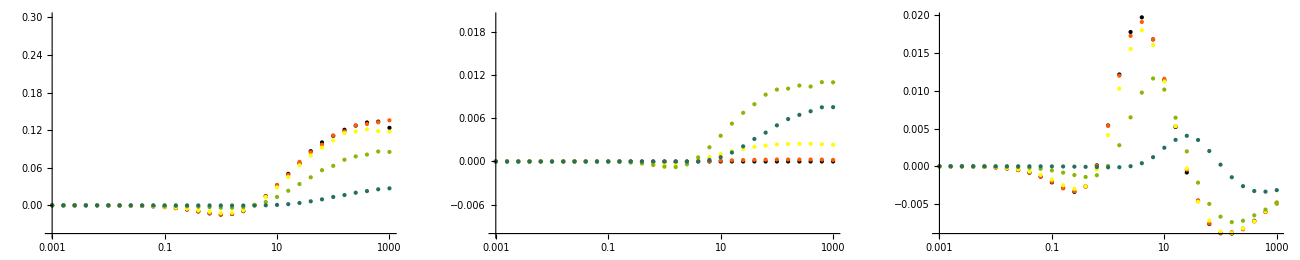

```mathematica
Module[{Qs,ηs,lLs,lGs,lTs,lPs},
Qs={1*^-2,1,10,100,1000};
ηs=Table[10^k,{k,-3,3,.2}];
lGs=Parallelize@Table[c1q[G][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lGs;*)
lLs=Parallelize@Table[c1q[L][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lLs;*)
lTs=lGs+1/2lLs;
lPs=Parallelize@Table[c1q[P][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lPs;*)
Show[GraphicsRow[{
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lTs],PlotRange-> {Full,{-.045,.3}},PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lLs],PlotRange-> {Full,{-.01,.02}},PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lPs],PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]]
}],ImageSize-> 1300]
]
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.000020999 and 4.22629×10^-7 for the integral and error estimates.

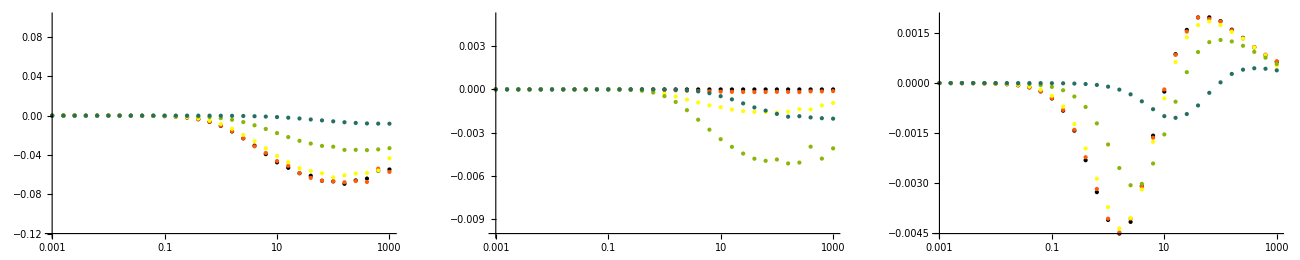

```mathematica
Module[{Qs,ηs,lLs,lGs,lTs,lPs},
Qs={1*^-2,1,10,100,1000};
ηs=Table[10^k,{k,-3,3,.2}];
lGs=Parallelize@Table[cbar1q[G][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lGs;*)
lLs=Parallelize@Table[cbar1q[L][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lLs;*)
lTs=lGs+1/2lLs;
lPs=Parallelize@Table[cbar1q[P][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lPs;*)
Show[GraphicsRow[{
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lTs],PlotRange-> {Full,{-.12,.1}},PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lLs],PlotRange-> {Full,{-.01,.005}},PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lPs],PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]]
}],ImageSize-> 1300]
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {4.01975×10^-6, 0.999943}. NIntegrate obtained -0.0000212968 and 6.01458×10^-7 for the integral and error estimates.

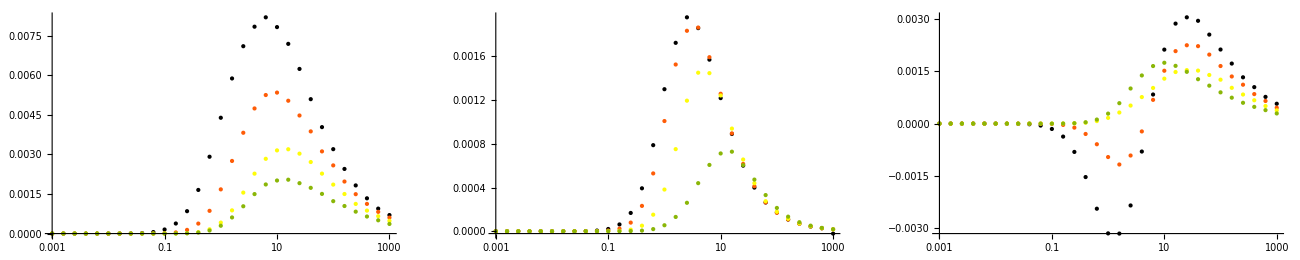

```mathematica
Module[{Qs,ηs,lLs,lGs,lTs,lPs},
Qs={1,10,100,1000};
ηs=Table[10^k,{k,-3,3,.2}];
lGs=Parallelize@Table[d1q[G][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lGs;*)
lLs=Parallelize@Table[d1q[L][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lLs;*)
lTs=lGs+1/2lLs;
lPs=Parallelize@Table[d1q[P][sOfη@η,Q,4.75^2],{Q,Qs},{η,ηs}];
(*Print@lPs;*)
Show[GraphicsRow[{
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lTs],PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lLs],PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lPs],PlotRange-> Full,PlotStyle->ColorData[3,"ColorList"]]
}],ImageSize-> 1300]
]
```

```mathematica
Module[{ηs,Qs,lL,lG,lT,lP},
ηs=Table[10^k,{k,-3,3,.2}];
lG=Parallelize@Table[cd1q[G][sOfη@η,1000,4.75^2],{η,ηs}];
Print@lG;
lL=Parallelize@Table[cd1q[L][sOfη@η,1000,4.75^2],{η,ηs}];
Print@lL;
lT=lG+1/2lL;
lP=Parallelize@Table[cd1q[P][sOfη@η,1000,4.75^2],{η,ηs}];
Print@lP;
]
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.90037×10^-16 and 2.19324×10^-17 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -6.18412×10^-15 and 5.09297×10^-16 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.26183×10^-13 and 8.44903×10^-14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.28532×10^-11 and 1.17689×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.67782×10^-13 and 6.75741×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.78144×10^-10 and 1.56842×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.45424×10^-14 and 1.49066×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 4.75512×10^-16 and 1.06644×10^-16 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 6.60218×10^-12 and 3.37677×10^-13 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 3.22019×10^-10 and 4.18957×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.78525×10^-13 and 2.26007×10^-14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.0786×10^-7 and 1.13987×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.728×10^-9 and 5.66466×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.72914×10^-8 and 3.49864×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.19828×10^-11 and 1.62551×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.18284×10^-7 and 6.94223×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.11941×10^-7 and 3.35881×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -8.80357×10^-7 and 1.88626×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.19107×10^-8 and 1.02551×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -8.59074×10^-7 and 9.12151×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.33991×10^-8 and 6.4364×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.11363×10^-7 and 4.88772×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.14726×10^-6 and 1.2708×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 4.02529×10^-10 and 1.92791×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.12753×10^-6 and 7.71135×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -6.93027×10^-7 and 9.67305×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.72166×10^-6 and 1.12185×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.74023×10^-6 and 6.30699×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.5568×10^-9 and 4.5613×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.63222×10^-7 and 1.35095×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.71538×10^-6 and 1.01653×10^-7 for the integral and error estimates.

{-2.90037×10^-16,4.75512×10^-16,-6.18412×10^-15,1.45424×10^-14,1.67782×10^-13,-2.78525×10^-13,-2.26183×10^-13,6.60218×10^-12,2.28532×10^-11,3.22019×10^-10,1.78144×10^-10,-1.728×10^-9,-1.19828×10^-11,-2.5568×10^-9,-2.19107×10^-8,4.02529×10^-10,1.72914×10^-8,-4.33991×10^-8,-1.0786×10^-7,-8.80357×10^-7,-4.11941×10^-7,-5.11363×10^-7,-5.18284×10^-7,-8.59074×10^-7,-2.14726×10^-6,-6.93027×10^-7,-1.72166×10^-6,-1.71538×10^-6,-1.12753×10^-6,-1.63222×10^-7,-1.74023×10^-6}

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.01601×10^-12 and 2.9277×10^-13 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.19478×10^-16 and 6.62655×10^-18 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.77787×10^-16 and 2.49725×10^-16 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.79685×10^-13 and 9.93002×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -6.70374×10^-19 and 1.8901×10^-19 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.68483×10^-20 and 4.914×10^-21 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 3.15619×10^-11 and 8.26412×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -9.25951×10^-11 and 1.85315×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 7.05364×10^-18 and 1.16814×10^-18 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.5036×10^-19 and 3.38611×10^-20 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.19436×10^-16 and 4.04138×10^-17 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.08373×10^-13 and 1.53665×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -6.07468×10^-8 and 2.02809×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.20247×10^-7 and 7.64574×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.1536×10^-6 and 2.24416×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.03077×10^-8 and 1.63753×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.42727×10^-6 and 2.68068×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -7.1132×10^-7 and 1.54896×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.2375×10^-7 and 3.46099×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.75997×10^-11 and 4.96523×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.07583×10^-9 and 2.04405×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.05937×10^-7 and 1.78386×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.38107×10^-7 and 8.11118×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.11392×10^-6 and 2.97505×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.13655×10^-7 and 4.5276×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -4.04597×10^-8 and 5.55243×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.04636×10^-8 and 2.14363×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -8.83728×10^-8 and 4.86368×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -7.49687×10^-8 and 2.80367×10^-9 for the integral and error estimates.

{-3.68483×10^-20,-4.5036×10^-19,-6.70374×10^-19,7.05364×10^-18,1.19478×10^-16,-2.19436×10^-16,-5.77787×10^-16,-1.08373×10^-13,-3.79685×10^-13,-8.65206×10^-12,-1.01601×10^-12,-9.25951×10^-11,3.15619×10^-11,2.75997×10^-11,-2.07583×10^-9,-4.04597×10^-8,-1.03077×10^-8,-8.83728×10^-8,-4.20247×10^-7,-7.1132×10^-7,-6.07468×10^-8,-1.42727×10^-6,-3.2375×10^-7,-2.11392×10^-6,-1.1536×10^-6,-3.05937×10^-7,-1.53342×10^-6,-1.38107×10^-7,-4.13655×10^-7,-7.49687×10^-8,-5.04636×10^-8}

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.01099×10^-14 and 3.31359×10^-16 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 4.73048×10^-12 and 7.56618×10^-14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.33961×10^-15 and 2.15397×10^-17 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.48609×10^-14 and 5.44258×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.45691×10^-11 and 1.68897×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.88775×10^-11 and 1.12494×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.15169×10^-13 and 1.49022×10^-15 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 7.26823×10^-13 and 3.2175×10^-13 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.53737×10^-16 and 1.06525×10^-16 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.01083×10^-13 and 1.97263×10^-14 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.66078×10^-11 and 4.25596×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.05661×10^-9 and 5.42565×10^-11 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.27016×10^-8 and 3.69608×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -3.29585×10^-11 and 9.69586×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -7.46764×10^-7 and 2.26714×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.80567×10^-7 and 1.21188×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 2.80189×10^-8 and 1.89953×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 1.49797×10^-9 and 1.73544×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.03998×10^-7 and 3.35312×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.6676×10^-7 and 7.17436×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.71354×10^-7 and 1.57345×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.03739×10^-7 and 1.71734×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.49804×10^-6 and 2.28248×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.81416×10^-7 and 7.02548×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -5.61445×10^-8 and 3.50494×10^-9 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -7.6401×10^-7 and 3.67236×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 4.9915×10^-9 and 4.259×10^-10 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -8.50784×10^-7 and 3.50865×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.23536×10^-7 and 1.4514×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -9.20736×10^-7 and 2.82586×10^-8 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.15516×10^-7 and 4.73921×10^-9 for the integral and error estimates.

{1.33961×10^-15,2.53737×10^-16,2.01099×10^-14,1.15169×10^-13,-1.48609×10^-14,2.01083×10^-13,4.73048×10^-12,7.26823×10^-13,1.88775×10^-11,2.66078×10^-11,-3.45691×10^-11,2.05661×10^-9,1.49797×10^-9,4.9915×10^-9,-3.29585×10^-11,2.80189×10^-8,-1.27016×10^-8,-1.6676×10^-7,-1.80567×10^-7,-1.03739×10^-7,-7.6401×10^-7,-9.20736×10^-7,-5.03998×10^-7,-8.50784×10^-7,-7.46764×10^-7,-1.49804×10^-6,-2.71354×10^-7,-2.23536×10^-7,-1.81416×10^-7,-1.15516×10^-7,-5.61445×10^-8}

#### analytic

```mathematica
Last@psLogsA2
Last@psLogsA2/.psLogList[S1]
FullSimplify@Last@IntAL2finiteCoeffs
```

psLog4[S1][tpsp,s5]

(m2 sp-t1 (sp+t1+u1))/(m2 sp)

(8 π q2 (m2+sp+t1+u1) (2 m2 q2 sp+t1 (-q2 t1+sp (sp+u1))))/(sp^2 (q2+sp)^2 t1 (sp+t1+u1))

```mathematica
Module[{list,log,i,s4max,coeff,k,j,Mt1min,Mt1max,r,vars,lVars},
list=psLogsA2/.psLogList[S1];
log=Log[Last@list/.{u1-> s4-sp-t1}];
coeff=FullSimplify[Last@IntAL2finiteCoeffs/.{u1-> s4-sp-t1}]*(s4/(s4+m2));
Print[coeff,"*",log];
s4max=s/(sp t1)(t1+sp(1-ρ)/2)(t1+sp(1+ρ)/2);
i=Simplify@Integrate[(coeff)log,s4];
(*Print@i;*)
k=Simplify[Simplify[Limit[i,s4-> s4max]/.{ρ-> Sqrt[1-4m2/s]}/.normKinVars]-Limit[i,s4-> 0]];
Mt1min=sp(1-ρ)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+ρ)/2/.normTotalCSVars/.normKinVars;
j=Simplify@Integrate[k,t1];
Print@j;
r=Simplify@Together[Simplify@Limit[j,t1-> -Mt1min]-Simplify@Limit[j,t1-> -Mt1max]];

vars=Reap[Expand@r/.{Log[x_]:> Log[Sow[x,Log]],PolyLog[2,x_]:> PolyLog[2,Sow[x,PolyLog]]}][[2]];
vars=DeleteDuplicates/@vars;
lVars=MapIndexed[{e,i}↦(Log[e]-> l[First@i]),First@vars];
Print@lVars;
Print@FullSimplify[r/.lVars/.{l[3]->ll+l[6],l[1]-> -ll+l[4],l[2]-> ll+l[5]}/.{l[5]-> l[57]+l[7]}]
]
```

(8 π q2 (2 m2 q2 sp+t1 (s4 sp-(q2+sp) t1)))/(sp^2 (q2+sp)^2 t1)*Log[(m2 sp-s4 t1)/(m2 sp)]

1/(9 sp^3 (q2+sp)^2 t1)2 π q2 (72 m2^2 q2 sp^3+27 m2^2 sp^4-216 m2 q2^2 sp t1^2-288 m2 q2 sp^2 t1^2-39 q2^2 sp^2 t1^2-72 m2 sp^3 t1^2-78 q2 sp^3 t1^2-39 sp^4 t1^2+6 q2^2 sp t1^3+12 q2 sp^2 t1^3+6 sp^3 t1^3+13 q2^2 t1^4+26 q2 sp t1^4+13 sp^2 t1^4-18 m2 sp^2 (2 q2^2+3 q2 sp+sp^2) t1 Log[t1]^2+72 m2 q2^2 sp^2 t1 Log[sp+t1]+108 m2 q2 sp^3 t1 Log[sp+t1]+12 q2^2 sp^3 t1 Log[sp+t1]+36 m2 sp^4 t1 Log[sp+t1]+24 q2 sp^4 t1 Log[sp+t1]+12 sp^5 t1 Log[sp+t1]-36 m2 sp^2 (2 q2^2+3 q2 sp+sp^2) t1 Log[t1] (1+Log[(sp+t1)/sp]-Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)])+72 m2 q2^2 sp t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]+108 m2 q2 sp^2 t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]+18 q2^2 sp^2 t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]+36 m2 sp^3 t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]+36 q2 sp^3 t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]+18 sp^4 t1^2 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]-6 q2^2 t1^4 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]-12 q2 sp t1^4 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]-6 sp^2 t1^4 Log[-((q2+sp) t1 (sp+t1))/(m2 sp^2)]-36 m2 sp^2 (2 q2^2+3 q2 sp+sp^2) t1 PolyLog[2,-t1/sp])

{Log[-(sp (4 m2+q2+sp))/(2 (q2+sp))]→l[1],Log[1/2-(2 m2)/(q2+sp)]→l[2],Log[sp (1/2-(2 m2)/(q2+sp))]→l[3],Log[sp (-1/2+(2 m2)/(q2+sp))]→l[4],Log[1/2+(2 m2)/(q2+sp)]→l[5],Log[sp (1/2+(2 m2)/(q2+sp))]→l[6],Log[(-16 m2^2+(q2+sp)^2)/(4 m2 (q2+sp))]→l[7]}

1/(9 sp (q2+sp)^3 (-4 m2+q2+sp) (4 m2+q2+sp))2 π q2 (-12 ll sp (q2+sp)^5-2304 m2^4 (q2+sp) (2 q2 (-3+l[7])+sp (-2+l[7]))+256 m2^5 sp (-13+6 l[7])+48 m2^2 (q2+sp)^3 (6 q2 (-3+l[7])+sp (-6+4 ll+3 l[7]))-3 m2 (q2+sp)^4 (6 ll^2 (2 q2+sp)+sp (47-18 l[7])+12 ll (2 q2+sp) (2+l[57]))+16 m2^3 (q2+sp)^2 (36 q2 (-2+ll (4+ll+2 l[57]))+sp (127-60 l[7]+18 ll (4+ll+2 l[57])))+36 m2 (4 m2-q2-sp) (q2+sp)^2 (4 m2+q2+sp) (2 q2+sp) (PolyLog[2,1/2-(2 m2)/(q2+sp)]-PolyLog[2,1/2+(2 m2)/(q2+sp)]))

```mathematica
Module[{list,log,i,s4max,coeff,k,j,Mt1min,Mt1max,r,vars,lVars},
list=psLogsA2/.psLogList[S1];
log=Log[list[[3]]/.{u1-> s4-sp-t1}];
coeff=FullSimplify[IntAL2finiteCoeffs[[1+3]]/.{u1-> s4-sp-t1}]*(s4/(s4+m2));
Print[coeff,"*",log];
s4max=s/(sp t1)(t1+sp(1-ρ)/2)(t1+sp(1+ρ)/2);
i=Simplify@Integrate[(coeff)log,s4];
(*Print@i;*)
k=Simplify[Simplify[Limit[i,s4-> s4max]/.{ρ-> Sqrt[1-4m2/s]}/.normKinVars]-Limit[i,s4-> 0]];
Mt1min=sp(1-ρ)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+ρ)/2/.normTotalCSVars/.normKinVars;
j=Simplify@Integrate[k,t1];
Print@j;
r=Simplify@Together[Simplify@Limit[j,t1-> -Mt1min]-Simplify@Limit[j,t1-> -Mt1max]];

vars=Reap[Expand@r/.{Log[x_]:> Log[Sow[x,Log]],PolyLog[2,x_]:> PolyLog[2,Sow[x,PolyLog]]}][[2]];
vars=DeleteDuplicates/@vars;
lVars=MapIndexed[{e,i}↦(Log[e]-> l[First@i]),First@vars];
Print@lVars;
Print@Simplify[r/.lVars]
]
```

-(8 π q2 (2 m2 q2 sp+t1 (s4 sp-(q2+sp) t1)))/(sp^2 (q2+sp)^2 t1)*Log[(q2 (m2 sp-s4 t1))/(sp (m2 q2+s4 t1))]

1/(3 sp^2 (q2+sp)^2)4 π q2 (-(3 m2^2 q2 sp^2)/t1-(3 m2^2 sp^3)/t1+13 m2 q2^2 t1+26 m2 q2 sp t1+13 m2 sp^2 t1-(64 m2^2 q2^2 √sp ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))-(80 m2^2 q2 sp^(3/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(8 m2 q2^2 sp^(3/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))-(16 m2^2 sp^(5/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(4 m2 q2 sp^(5/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(2 q2^2 sp^(5/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))-(4 m2 sp^(7/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(4 q2 sp^(7/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(2 sp^(9/2) ArcTanh[(sp+2 t1)/(√sp √(-4 m2+sp))])/(√(-4 m2+sp))+(9 m2^2 q2^2 sp Log[m2 q2])/t1+6 m2 q2^2 t1 Log[m2 q2]+6 m2 q2 sp t1 Log[m2 q2]+(12 m2^2 q2 sp^2 Log[m2 sp])/t1+(3 m2^2 sp^3 Log[m2 sp])/t1+6 m2 q2 sp t1 Log[m2 sp]+6 m2 sp^2 t1 Log[m2 sp]+12 m2 q2^2 sp Log[t1]+18 m2 q2 sp^2 Log[t1]+6 m2 sp^3 Log[t1]+6 m2 q2^2 sp Log[t1]^2+9 m2 q2 sp^2 Log[t1]^2+3 m2 sp^3 Log[t1]^2-12 m2 q2^2 sp Log[sp+t1]-18 m2 q2 sp^2 Log[sp+t1]-2 q2^2 sp^2 Log[sp+t1]-6 m2 sp^3 Log[sp+t1]-4 q2 sp^3 Log[sp+t1]-2 sp^4 Log[sp+t1]+12 m2 q2^2 sp Log[t1] Log[(sp+t1)/sp]+18 m2 q2 sp^2 Log[t1] Log[(sp+t1)/sp]+6 m2 sp^3 Log[t1] Log[(sp+t1)/sp]-(12 m2^2 q2 sp^2 Log[-((q2+sp) t1 (sp+t1))/sp])/t1-(3 m2^2 sp^3 Log[-((q2+sp) t1 (sp+t1))/sp])/t1-6 m2 q2 sp t1 Log[-((q2+sp) t1 (sp+t1))/sp]-6 m2 sp^2 t1 Log[-((q2+sp) t1 (sp+t1))/sp]-12 m2 q2^2 sp Log[t1] Log[1+(2 t1)/(sp-√(sp (-4 m2+sp)))]-18 m2 q2 sp^2 Log[t1] Log[1+(2 t1)/(sp-√(sp (-4 m2+sp)))]-6 m2 sp^3 Log[t1] Log[1+(2 t1)/(sp-√(sp (-4 m2+sp)))]-12 m2 q2^2 sp Log[t1] Log[1+(2 t1)/(sp+√(sp (-4 m2+sp)))]-18 m2 q2 sp^2 Log[t1] Log[1+(2 t1)/(sp+√(sp (-4 m2+sp)))]-6 m2 sp^3 Log[t1] Log[1+(2 t1)/(sp+√(sp (-4 m2+sp)))]+(12 m2^2 q2 sp^2 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))])/t1+(3 m2^2 sp^3 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))])/t1-12 m2 q2^2 t1 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-12 m2 q2 sp t1 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-3 q2^2 sp t1 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-6 q2 sp^2 t1 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-3 sp^3 t1 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]+2 q2 t1^3 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]+(q2^2 t1^3 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))])/sp+sp t1^3 Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-12 m2 q2^2 sp Log[t1] Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-18 m2 q2 sp^2 Log[t1] Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]-6 m2 sp^3 Log[t1] Log[-(q2 t1 (sp+t1))/(sp (m2 sp+t1 (sp+t1)))]+q2^2 sp^2 Log[m2 sp+t1 (sp+t1)]+2 q2 sp^3 Log[m2 sp+t1 (sp+t1)]+sp^4 Log[m2 sp+t1 (sp+t1)]-(9 m2^2 q2^2 sp Log[((q2+sp) (m2 sp+t1 (sp+t1)))/sp])/t1-6 m2 q2^2 t1 Log[((q2+sp) (m2 sp+t1 (sp+t1)))/sp]-6 m2 q2 sp t1 Log[((q2+sp) (m2 sp+t1 (sp+t1)))/sp]+6 m2 sp (2 q2^2+3 q2 sp+sp^2) PolyLog[2,-t1/sp]-6 m2 sp (2 q2^2+3 q2 sp+sp^2) PolyLog[2,(2 t1)/(-sp+√(sp (-4 m2+sp)))]-12 m2 q2^2 sp PolyLog[2,-(2 t1)/(sp+√(sp (-4 m2+sp)))]-18 m2 q2 sp^2 PolyLog[2,-(2 t1)/(sp+√(sp (-4 m2+sp)))]-6 m2 sp^3 PolyLog[2,-(2 t1)/(sp+√(sp (-4 m2+sp)))])

{Log[m2 q2]→l[1],Log[m2 sp]→l[2],Log[-(sp (4 m2+q2+sp))/(2 (q2+sp))]→l[3],Log[(-4 m2+q2+sp)/(2 (q2+sp))]→l[4],Log[sp (1/2-(2 m2)/(q2+sp))]→l[5],Log[sp (-1/2+(2 m2)/(q2+sp))]→l[6],Log[(4 m2+q2+sp)/(2 (q2+sp))]→l[7],Log[sp (1/2+(2 m2)/(q2+sp))]→l[8],Log[(sp (-16 m2^2+(q2+sp)^2))/(4 (q2+sp))]→l[9],Log[(q2 (-4 m2+q2+sp) (4 m2+q2+sp))/(16 m2^2 sp+4 m2 (q2+sp)^2-sp (q2+sp)^2)]→l[10],Log[(16 m2^2 sp+4 m2 (q2+sp)^2-sp (q2+sp)^2)/(4 (q2+sp))]→l[11],Log[1+(sp (-4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]→l[12],Log[1+(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]→l[13],Log[1+((4 m2-q2-sp) sp)/((q2+sp) (sp+√(sp (-4 m2+sp))))]→l[14],Log[1-(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]→l[15]}

1/(3 sp^2 (q2+sp)^3 (-16 m2^2+(q2+sp)^2))4 π q2 (-832 m2^4 q2^2 sp+48 m2^3 q2^3 sp+52 m2^2 q2^4 sp-1664 m2^4 q2 sp^2+144 m2^3 q2^2 sp^2+208 m2^2 q2^3 sp^2-832 m2^4 sp^3+144 m2^3 q2 sp^3+312 m2^2 q2^2 sp^3+48 m2^3 sp^4+208 m2^2 q2 sp^4+52 m2^2 sp^5+(2048 m2^4 q2^3 √sp ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(128 m2^2 q2^5 √sp ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(4608 m2^4 q2^2 sp^(3/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(256 m2^3 q2^3 sp^(3/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(544 m2^2 q2^4 sp^(3/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(16 m2 q2^5 sp^(3/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(3072 m2^4 q2 sp^(5/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(384 m2^3 q2^2 sp^(5/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(960 m2^2 q2^3 sp^(5/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(56 m2 q2^4 sp^(5/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(4 q2^5 sp^(5/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(512 m2^4 sp^(7/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(896 m2^2 q2^2 sp^(7/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(64 m2 q2^3 sp^(7/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(20 q2^4 sp^(7/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(128 m2^3 sp^(9/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(448 m2^2 q2 sp^(9/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(16 m2 q2^2 sp^(9/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(40 q2^3 sp^(9/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(96 m2^2 sp^(11/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(16 m2 q2 sp^(11/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(40 q2^2 sp^(11/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-(8 m2 sp^(13/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(20 q2 sp^(13/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))+(4 sp^(15/2) ArcTanh[(4 m2 √sp)/(√(-4 m2+sp) (q2+sp))])/(√(-4 m2+sp))-144 m2^3 q2^4 l[1]-384 m2^4 q2^2 sp l[1]-288 m2^3 q2^3 sp l[1]+24 m2^2 q2^4 sp l[1]-384 m2^4 q2 sp^2 l[1]-144 m2^3 q2^2 sp^2 l[1]+72 m2^2 q2^3 sp^2 l[1]+72 m2^2 q2^2 sp^3 l[1]+24 m2^2 q2 sp^4 l[1]-192 m2^3 q2^3 sp l[2]-384 m2^4 q2 sp^2 l[2]-432 m2^3 q2^2 sp^2 l[2]+24 m2^2 q2^3 sp^2 l[2]-384 m2^4 sp^3 l[2]-288 m2^3 q2 sp^3 l[2]+72 m2^2 q2^2 sp^3 l[2]-48 m2^3 sp^4 l[2]+72 m2^2 q2 sp^4 l[2]+24 m2^2 sp^5 l[2]+192 m2^3 q2^3 sp l[3]-12 m2 q2^5 sp l[3]+480 m2^3 q2^2 sp^2 l[3]-54 m2 q2^4 sp^2 l[3]+384 m2^3 q2 sp^3 l[3]-96 m2 q2^3 sp^3 l[3]+96 m2^3 sp^4 l[3]-84 m2 q2^2 sp^4 l[3]-36 m2 q2 sp^5 l[3]-6 m2 sp^6 l[3]+96 m2^3 q2^3 sp l[3]^2-6 m2 q2^5 sp l[3]^2+240 m2^3 q2^2 sp^2 l[3]^2-27 m2 q2^4 sp^2 l[3]^2+192 m2^3 q2 sp^3 l[3]^2-48 m2 q2^3 sp^3 l[3]^2+48 m2^3 sp^4 l[3]^2-42 m2 q2^2 sp^4 l[3]^2-18 m2 q2 sp^5 l[3]^2-3 m2 sp^6 l[3]^2+192 m2^3 q2^3 sp l[3] l[4]-12 m2 q2^5 sp l[3] l[4]+480 m2^3 q2^2 sp^2 l[3] l[4]-54 m2 q2^4 sp^2 l[3] l[4]+384 m2^3 q2 sp^3 l[3] l[4]-96 m2 q2^3 sp^3 l[3] l[4]+96 m2^3 sp^4 l[3] l[4]-84 m2 q2^2 sp^4 l[3] l[4]-36 m2 q2 sp^5 l[3] l[4]-6 m2 sp^6 l[3] l[4]-192 m2^3 q2^3 sp l[5]+12 m2 q2^5 sp l[5]-480 m2^3 q2^2 sp^2 l[5]-32 m2^2 q2^3 sp^2 l[5]+54 m2 q2^4 sp^2 l[5]+2 q2^5 sp^2 l[5]-384 m2^3 q2 sp^3 l[5]-96 m2^2 q2^2 sp^3 l[5]+96 m2 q2^3 sp^3 l[5]+10 q2^4 sp^3 l[5]-96 m2^3 sp^4 l[5]-96 m2^2 q2 sp^4 l[5]+84 m2 q2^2 sp^4 l[5]+20 q2^3 sp^4 l[5]-32 m2^2 sp^5 l[5]+36 m2 q2 sp^5 l[5]+20 q2^2 sp^5 l[5]+6 m2 sp^6 l[5]+10 q2 sp^6 l[5]+2 sp^7 l[5]-192 m2^3 q2^3 sp l[6]+12 m2 q2^5 sp l[6]-480 m2^3 q2^2 sp^2 l[6]+54 m2 q2^4 sp^2 l[6]-384 m2^3 q2 sp^3 l[6]+96 m2 q2^3 sp^3 l[6]-96 m2^3 sp^4 l[6]+84 m2 q2^2 sp^4 l[6]+36 m2 q2 sp^5 l[6]+6 m2 sp^6 l[6]-96 m2^3 q2^3 sp l[6]^2+6 m2 q2^5 sp l[6]^2-240 m2^3 q2^2 sp^2 l[6]^2+27 m2 q2^4 sp^2 l[6]^2-192 m2^3 q2 sp^3 l[6]^2+48 m2 q2^3 sp^3 l[6]^2-48 m2^3 sp^4 l[6]^2+42 m2 q2^2 sp^4 l[6]^2+18 m2 q2 sp^5 l[6]^2+3 m2 sp^6 l[6]^2-192 m2^3 q2^3 sp l[6] l[7]+12 m2 q2^5 sp l[6] l[7]-480 m2^3 q2^2 sp^2 l[6] l[7]+54 m2 q2^4 sp^2 l[6] l[7]-384 m2^3 q2 sp^3 l[6] l[7]+96 m2 q2^3 sp^3 l[6] l[7]-96 m2^3 sp^4 l[6] l[7]+84 m2 q2^2 sp^4 l[6] l[7]+36 m2 q2 sp^5 l[6] l[7]+6 m2 sp^6 l[6] l[7]+192 m2^3 q2^3 sp l[8]-12 m2 q2^5 sp l[8]+480 m2^3 q2^2 sp^2 l[8]+32 m2^2 q2^3 sp^2 l[8]-54 m2 q2^4 sp^2 l[8]-2 q2^5 sp^2 l[8]+384 m2^3 q2 sp^3 l[8]+96 m2^2 q2^2 sp^3 l[8]-96 m2 q2^3 sp^3 l[8]-10 q2^4 sp^3 l[8]+96 m2^3 sp^4 l[8]+96 m2^2 q2 sp^4 l[8]-84 m2 q2^2 sp^4 l[8]-20 q2^3 sp^4 l[8]+32 m2^2 sp^5 l[8]-36 m2 q2 sp^5 l[8]-20 q2^2 sp^5 l[8]-6 m2 sp^6 l[8]-10 q2 sp^6 l[8]-2 sp^7 l[8]+192 m2^3 q2^3 sp l[9]+384 m2^4 q2 sp^2 l[9]+432 m2^3 q2^2 sp^2 l[9]-24 m2^2 q2^3 sp^2 l[9]+384 m2^4 sp^3 l[9]+288 m2^3 q2 sp^3 l[9]-72 m2^2 q2^2 sp^3 l[9]+48 m2^3 sp^4 l[9]-72 m2^2 q2 sp^4 l[9]-24 m2^2 sp^5 l[9]+768 m2^4 q2^2 sp l[10]-192 m2^3 q2^3 sp l[10]-48 m2^2 q2^4 sp l[10]-256 m2^5 sp^2 l[10]+768 m2^4 q2 sp^2 l[10]-272 m2^3 q2^2 sp^2 l[10]-144 m2^2 q2^3 sp^2 l[10]-9 m2 q2^4 sp^2 l[10]+32 m2^3 q2 sp^3 l[10]-144 m2^2 q2^2 sp^3 l[10]-36 m2 q2^3 sp^3 l[10]+112 m2^3 sp^4 l[10]-48 m2^2 q2 sp^4 l[10]-54 m2 q2^2 sp^4 l[10]-36 m2 q2 sp^5 l[10]-9 m2 sp^6 l[10]-192 m2^3 q2^3 sp l[3] l[10]+12 m2 q2^5 sp l[3] l[10]-480 m2^3 q2^2 sp^2 l[3] l[10]+54 m2 q2^4 sp^2 l[3] l[10]-384 m2^3 q2 sp^3 l[3] l[10]+96 m2 q2^3 sp^3 l[3] l[10]-96 m2^3 sp^4 l[3] l[10]+84 m2 q2^2 sp^4 l[3] l[10]+36 m2 q2 sp^5 l[3] l[10]+6 m2 sp^6 l[3] l[10]+192 m2^3 q2^3 sp l[6] l[10]-12 m2 q2^5 sp l[6] l[10]+480 m2^3 q2^2 sp^2 l[6] l[10]-54 m2 q2^4 sp^2 l[6] l[10]+384 m2^3 q2 sp^3 l[6] l[10]-96 m2 q2^3 sp^3 l[6] l[10]+96 m2^3 sp^4 l[6] l[10]-84 m2 q2^2 sp^4 l[6] l[10]-36 m2 q2 sp^5 l[6] l[10]-6 m2 sp^6 l[6] l[10]+144 m2^3 q2^4 l[11]+384 m2^4 q2^2 sp l[11]+288 m2^3 q2^3 sp l[11]-24 m2^2 q2^4 sp l[11]+384 m2^4 q2 sp^2 l[11]+144 m2^3 q2^2 sp^2 l[11]-72 m2^2 q2^3 sp^2 l[11]-72 m2^2 q2^2 sp^3 l[11]-24 m2^2 q2 sp^4 l[11]+192 m2^3 q2^3 sp l[6] l[12]-12 m2 q2^5 sp l[6] l[12]+480 m2^3 q2^2 sp^2 l[6] l[12]-54 m2 q2^4 sp^2 l[6] l[12]+384 m2^3 q2 sp^3 l[6] l[12]-96 m2 q2^3 sp^3 l[6] l[12]+96 m2^3 sp^4 l[6] l[12]-84 m2 q2^2 sp^4 l[6] l[12]-36 m2 q2 sp^5 l[6] l[12]-6 m2 sp^6 l[6] l[12]-192 m2^3 q2^3 sp l[3] l[13]+12 m2 q2^5 sp l[3] l[13]-480 m2^3 q2^2 sp^2 l[3] l[13]+54 m2 q2^4 sp^2 l[3] l[13]-384 m2^3 q2 sp^3 l[3] l[13]+96 m2 q2^3 sp^3 l[3] l[13]-96 m2^3 sp^4 l[3] l[13]+84 m2 q2^2 sp^4 l[3] l[13]+36 m2 q2 sp^5 l[3] l[13]+6 m2 sp^6 l[3] l[13]+192 m2^3 q2^3 sp l[6] l[14]-12 m2 q2^5 sp l[6] l[14]+480 m2^3 q2^2 sp^2 l[6] l[14]-54 m2 q2^4 sp^2 l[6] l[14]+384 m2^3 q2 sp^3 l[6] l[14]-96 m2 q2^3 sp^3 l[6] l[14]+96 m2^3 sp^4 l[6] l[14]-84 m2 q2^2 sp^4 l[6] l[14]-36 m2 q2 sp^5 l[6] l[14]-6 m2 sp^6 l[6] l[14]-192 m2^3 q2^3 sp l[3] l[15]+12 m2 q2^5 sp l[3] l[15]-480 m2^3 q2^2 sp^2 l[3] l[15]+54 m2 q2^4 sp^2 l[3] l[15]-384 m2^3 q2 sp^3 l[3] l[15]+96 m2 q2^3 sp^3 l[3] l[15]-96 m2^3 sp^4 l[3] l[15]+84 m2 q2^2 sp^4 l[3] l[15]+36 m2 q2 sp^5 l[3] l[15]+6 m2 sp^6 l[3] l[15]+6 m2 sp (q2+sp)^2 (2 q2+sp) (-16 m2^2+(q2+sp)^2) PolyLog[2,(-4 m2+q2+sp)/(2 (q2+sp))]-6 m2 sp (q2+sp)^2 (2 q2+sp) (-16 m2^2+(q2+sp)^2) PolyLog[2,(4 m2+q2+sp)/(2 (q2+sp))]+192 m2^3 q2^3 sp PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-12 m2 q2^5 sp PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+480 m2^3 q2^2 sp^2 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-54 m2 q2^4 sp^2 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+384 m2^3 q2 sp^3 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-96 m2 q2^3 sp^3 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+96 m2^3 sp^4 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-84 m2 q2^2 sp^4 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-36 m2 q2 sp^5 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-6 m2 sp^6 PolyLog[2,((4 m2-q2-sp) sp)/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-192 m2^3 q2^3 sp PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+12 m2 q2^5 sp PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-480 m2^3 q2^2 sp^2 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+54 m2 q2^4 sp^2 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-384 m2^3 q2 sp^3 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+96 m2 q2^3 sp^3 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]-96 m2^3 sp^4 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+84 m2 q2^2 sp^4 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+36 m2 q2 sp^5 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+6 m2 sp^6 PolyLog[2,-(sp (4 m2+q2+sp))/((q2+sp) (-sp+√(sp (-4 m2+sp))))]+192 m2^3 q2^3 sp PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-12 m2 q2^5 sp PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+480 m2^3 q2^2 sp^2 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-54 m2 q2^4 sp^2 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+384 m2^3 q2 sp^3 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-96 m2 q2^3 sp^3 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+96 m2^3 sp^4 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-84 m2 q2^2 sp^4 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-36 m2 q2 sp^5 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-6 m2 sp^6 PolyLog[2,(sp (-4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-192 m2^3 q2^3 sp PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+12 m2 q2^5 sp PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-480 m2^3 q2^2 sp^2 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+54 m2 q2^4 sp^2 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-384 m2^3 q2 sp^3 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+96 m2 q2^3 sp^3 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]-96 m2^3 sp^4 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+84 m2 q2^2 sp^4 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+36 m2 q2 sp^5 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))]+6 m2 sp^6 PolyLog[2,(sp (4 m2+q2+sp))/((q2+sp) (sp+√(sp (-4 m2+sp))))])

```mathematica
Module[{list,log,i,s4max,coeff,k,j,Mt1min,Mt1max,r,vars,lVars},
list=psLogsA2/.psLogList[S1];
log=Log[list[[2]]/.{u1-> s4-sp-t1}];
coeff=FullSimplify[IntAL2finiteCoeffs[[1+2]]/.{u1-> s4-sp-t1}]*(s4/(s4+m2));
Print[coeff,"*",log];
s4max=s/(sp t1)(t1+sp(1-ρ)/2)(t1+sp(1+ρ)/2);
i=Simplify@Integrate[(coeff)log,s4];
(*Print@i;*)
k=Simplify[Simplify[Limit[i,s4-> s4max]/.{ρ-> Sqrt[1-4m2/s]}/.normKinVars]-Limit[i,s4-> 0]];
Mt1min=sp(1-ρ)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+ρ)/2/.normTotalCSVars/.normKinVars;
j=Simplify@Integrate[k,t1];
Print@j;
r=Simplify@Together[Simplify@Limit[j,t1-> -Mt1min]-Simplify@Limit[j,t1-> -Mt1max]];

vars=Reap[Expand@r/.{Log[x_]:> Log[Sow[x,Log]],PolyLog[2,x_]:> PolyLog[2,Sow[x,PolyLog]]}][[2]];
vars=DeleteDuplicates/@vars;
lVars=MapIndexed[{e,i}↦(Log[e]-> l[First@i]),First@vars];
Print@lVars;
Print@Simplify[r/.lVars]
]
```

-(4 π q2 (4 m2^2 (4 q2+5 sp)-2 m2 (2 q2^2+2 s4^2-5 s4 sp+4 sp^2+q2 (-4 s4+6 sp-3 t1)+s4 t1-3 sp t1)+(q2-s4+sp) (sp (q2-s4+sp)-(q2-2 s4+sp) t1)))/(sp^2 (-4 m2 (q2+sp)+(q2-s4+sp)^2)^(3/2))*Log[(2 m2 (q2+sp)+s4 (q2-s4+sp+√((-q2+s4-sp)^2-4 m2 (q2+sp))))/(2 m2 (q2+sp)-s4 (-q2+s4-sp+√((-q2+s4-sp)^2-4 m2 (q2+sp))))]

$Aborted

```mathematica
Module[{list,log,i,s4max,coeff,k,j,Mt1min,Mt1max,r,vars,lVars},
list=psLogsA2/.psLogList[S1];
log=1;
coeff=Expand[IntAL2finiteCoeffs[[1+0]]/.{u1-> s4-sp-t1}]*(s4/(s4+m2));
(*Print[coeff,"*",log];*)
s4max=s/(sp t1)(t1+sp(1-ρ)/2)(t1+sp(1+ρ)/2);
i=Simplify@Integrate[(coeff)log,s4];
(*Print@i;*)
k=Simplify[Simplify[Limit[i,s4-> s4max]/.{ρ-> Sqrt[1-4m2/s]}/.normKinVars]-Limit[i,s4-> 0]];
Mt1min=sp(1-ρ)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+ρ)/2/.normTotalCSVars/.normKinVars;
j=Simplify@Integrate[k,t1];
Print@j;
r=Simplify@Together[Simplify@Limit[j,t1-> -Mt1min]-Simplify@Limit[j,t1-> -Mt1max]];

vars=Reap[Expand@r/.{Log[x_]:> Log[Sow[x,Log]],PolyLog[2,x_]:> PolyLog[2,Sow[x,PolyLog]]}][[2]];
vars=DeleteDuplicates/@vars;
lVars=MapIndexed[{e,i}↦(Log[e]-> l[First@i]),First@vars];
Print@lVars;
Print@Simplify[r/.lVars]
]
```

$Aborted

## NLO γ*+g → Q+Qbar+g

```mathematica
getPsI[coeff_]:= MapIndexed[{e,path}↦If[e===0,0,psI[1/Times@@({tp,u6,s3,u7}^({3,3,3,3}-path))]],coeff,{4}];
getPsIk2[coeff_]:= MapIndexed[{e,path}↦If[e===0,0,psIk2[1/Times@@({tp,u6,s3,u7}^({3,3,3,3}-path))]],coeff,{4}];
getPsLogList[v_]:=DeleteDuplicates[Reap[Expand[v]/.{
psLog1[S_][ab_]:> Sow[psLog1[S][ab]],
psLog2[S_][ABC_]:> Sow[psLog2[S][ABC]],
psLog3[S_][ABC_]:> Sow[psLog3[S][ABC]],
psLog4[S_][ab_,ABC_]:> Sow[psLog4[S][ab,ABC]],
psLog5[S_][ABC_]:> Sow[psLog5[S][ABC]]
}][[2,1]]];
```

### RQED

#### Compute

```mathematica
Do[
psIRQED[proj]=getPsI[CoeffRQED[proj]/.{k2hat2-> 0}];
IntRQED[proj]=Expand@Total[CoeffRQED[proj]*psIRQED[proj],4];
IntRQEDfinite[proj] =Coefficient[IntRQED[proj],ϵ,0];
psLogsRQED[proj]=getPsLogList[IntRQEDfinite[proj]];
,{proj,{G,L,P}}]
```

```mathematica
Module[{parallelCollect},
parallelCollect[e_]:=Module[{f,l,vs,cc},
f=e;
l=Reap[f//.{
psLog1[S_][ab_]:> Sow[psLog1[S][ab]],
psLog2[S_][ABC_]:> Sow[psLog2[S][ABC]],
psLog3[S_][ABC_]:> Sow[psLog3[S][ABC]],
psLog4[S_][ab_,ABC_]:> Sow[psLog4[S][ab,ABC]],
psLog5[S_][ABC_]:> Sow[psLog5[S][ABC]],
psDiLog1[S_][ABC_]:> Sow[psDiLog1[S][ABC]],
psDiLog2[S_][ABC_]:> Sow[psDiLog2[S][ABC]],
psDiLog3[S_][ABC_]:> Sow[psDiLog3[S][ABC]],
Sqrt[z_]:> Sow[Sqrt[z],sqrt]}];
l=Last@l;
l=DeleteDuplicates/@l;
vs=Flatten[l];
Print@vs;
PrintTemporary["compute coeffs"];
cc=CoefficientRules[f,vs];
PrintTemporary["simplify coeffs: "<>ToString@Length@cc];
cc=ParallelMap[el↦(First@el-> If[Total@First@el>0,Simplify[Last@el],Last@el]),cc];
FromCoefficientRules[cc,vs]
];
IntRQEDfinite[G]=parallelCollect[IntRQEDfinite[G]/.normKinVars/.{u1-> s4-sp-t1}];
IntRQEDfinite[L]=parallelCollect[IntRQEDfinite[L]/.normKinVars/.{u1-> s4-sp-t1}];
IntRQEDfinite[P]=parallelCollect[IntRQEDfinite[P]/.normKinVars/.{u1-> s4-sp-t1}];
]
```

{psLog1[S1][u6],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],√(t1 ((q2+sp)^2 t1+4 m2 (sp (s4-t1)-q2 t1)))}

{psLog1[S1][u6],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],√(t1 ((q2+sp)^2 t1+4 m2 (sp (s4-t1)-q2 t1)))}

{psLog1[S1][u6],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],√(t1 ((q2+sp)^2 t1+4 m2 (sp (s4-t1)-q2 t1)))}

### ROK

#### Compute

```mathematica
Do[
psIROK1[proj]=getPsI[CoeffROK1[proj]];
IntROK1[proj]=Expand@Total[CoeffROK1[proj]*psIROK1[proj],4];
psIROK2[proj]=getPsI[CoeffROK2[proj]];
IntROK2[proj]=Expand@Total[CoeffROK2[proj]*psIROK2[proj],4];
(* compute pole terms *)
IntROK1pole[proj] =Coefficient[IntROK1[proj],ϵ,-1];
IntROK2pole[proj] =Coefficient[IntROK2[proj],ϵ,-1];
(* compute finite terms *)
IntROK1finite[proj] =Coefficient[IntROK1[proj],ϵ,0];
IntROK2finite[proj] =Coefficient[IntROK2[proj],ϵ,0];
psLogsROK1[proj]=getPsLogList[IntROK1finite[proj]];
psLogsROK2[proj]=getPsLogList[IntROK2finite[proj]];
,{proj,{G,L}}]
(*psIRPOKk0=getPsI[CoeffRPOKk0];
psIRPOKk2=getPsIk2[CoeffRPOKk2];
IntROK[P]=Expand@Total[CoeffRPOKk0[proj]*psIRPOKk0[proj],4]+Expand@Total[CoeffRPOKk2[proj]*psIRPOKk2[proj],4];*)
```

```mathematica
Module[{parallelCollect},
parallelCollect[e_]:=Module[{f,l,vs,cc},
f=e;
l=Reap[f//.{
psLog1[S_][ab_]:> Sow[psLog1[S][ab]],
psLog2[S_][ABC_]:> Sow[psLog2[S][ABC]],
psLog3[S_][ABC_]:> Sow[psLog3[S][ABC]],
psLog4[S_][ab_,ABC_]:> Sow[psLog4[S][ab,ABC]],
psLog5[S_][ABC_]:> Sow[psLog5[S][ABC]],
psDiLog1[S_][ABC_]:> Sow[psDiLog1[S][ABC]],
psDiLog2[S_][ABC_]:> Sow[psDiLog2[S][ABC]],
psDiLog3[S_][ABC_]:> Sow[psDiLog3[S][ABC]],
Sqrt[z_]:> Sow[Sqrt[z],sqrt]}];
l=Last@l;
l=DeleteDuplicates/@l;
vs=Flatten[l];
Print@vs;
PrintTemporary["compute coeffs"];
cc=CoefficientRules[f,vs];
PrintTemporary["simplify coeffs: "<>ToString@Length@cc];
cc=ParallelMap[el↦(First@el-> Simplify[Last@el]),cc];
FromCoefficientRules[cc,vs]
];
IntROK1finite[G]=parallelCollect[IntROK1finite[G]/.normKinVars/.{u1-> s4-sp-t1}];
IntROK1finite[L]=parallelCollect[IntROK1finite[L]/.normKinVars/.{u1-> s4-sp-t1}];
IntROK2finite[G]=parallelCollect[IntROK2finite[G]/.normKinVars/.{u1-> s4-sp-t1}];
IntROK2finite[L]=parallelCollect[IntROK2finite[L]/.normKinVars/.{u1-> s4-sp-t1}];
]
```

{psLog1[S1][u6],psLog2[S1][s3],psLog2[S1][u7],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],√(t1 ((q2+sp)^2 t1+4 m2 (sp (s4-t1)-q2 t1)))}

{psLog1[S1][u6],psLog2[S1][s3],psLog2[S1][u7],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],√(t1 ((q2+sp)^2 t1+4 m2 (sp (s4-t1)-q2 t1)))}

{psLog2[S1][u7],psLog3[S1][u7]}

{psLog2[S1][u7],psLog3[S1][u7]}

#### check to Nucl.Phys.B 392-162

```mathematica
Module[{a, Sϵ,psR,psFactor,f},
a[G]=1;
a[L]=2(1+ϵ/2);
Sϵ=(4π)^(-2-ϵ/2);
psR[i_]=64 Kgγ α αS^2 eH^2 NC CF 1/(1+ϵ/2)^2 π^3 Sϵ^2 μ2^(-ϵ/2)/Gamma[1+ϵ]*a[i]*s4/(s4+m2)*(s4^2/(s4+m2))^(ϵ/2);
psFactor[L]=2Kgγ α αS^2 eH^2 NC CA CF 1/(1+ϵ/2) 1/(4π)^(ϵ/2) 1/Gamma[1+ϵ/2];
psFactor[G]=Kgγ α αS^2 eH^2 NC CA CF 1/(1+ϵ/2)^2 1/(4π)^(ϵ/2) 1/Gamma[1+ϵ/2];
f=( s4)/(4π(s4+m2));
Print@Series[CA psR[L],{ϵ,0,1}];
Print@Series[f*psFactor[L],{ϵ,0,1}];
Print@Series[CA psR[G],{ϵ,0,1}];
Print@Series[f*psFactor[G],{ϵ,0,1}];
]
```

(CA CF eH^2 Kgγ NC s4 α αS^2)/(2 π (m2+s4))+(CA CF eH^2 Kgγ NC s4 α αS^2 (-1+2 EulerGamma-4 Log[2]-2 Log[π]+Log[s4^2/(m2+s4)]-Log[μ2]) ϵ)/(4 π (m2+s4))+O[ϵ]^2

(CA CF eH^2 Kgγ NC s4 α αS^2)/(2 π (m2+s4))+(CA CF eH^2 Kgγ NC s4 α αS^2 (-1+EulerGamma-2 Log[2]-Log[π]) ϵ)/(4 π (m2+s4))+O[ϵ]^2

(CA CF eH^2 Kgγ NC s4 α αS^2)/(4 π (m2+s4))+(CA CF eH^2 Kgγ NC s4 α αS^2 (-2+2 EulerGamma-2 Log[4 π]+Log[s4^2/(m2+s4)]-Log[μ2]) ϵ)/(8 π (m2+s4))+O[ϵ]^2

(CA CF eH^2 Kgγ NC s4 α αS^2)/(4 π (m2+s4))+(CA CF eH^2 Kgγ NC s4 α αS^2 (-2+EulerGamma-2 Log[2]-Log[π]) ϵ)/(8 π (m2+s4))+O[ϵ]^2

```mathematica
Module[{me,refPole,denom},
me[G]=(s4)/(4π(s4+m2))(IntROK1pole[G]+IntROK2pole[G]);
denom[G]=t1^2(sp+t1)^3u1^4 s4;
refPole[G]=2(-1/u1)*(((sp+t1)^2+u1^2)/(s4(sp+t1))-((sp+t1)^2+s4^2)/(u1(sp+t1))-(u1^2+s4^2)/(sp+t1)^2)*
(-(t1^2+(sp+t1)^2)/(t1(sp+t1))
+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1)) + 2sp q2/(t1 u1)-2q2^2(sp+t1)/(t1 u1^2)
-2m2 q2/(t1^2 u1^2)(t1^2 + (sp+t1)^2));
Print@FullSimplify@Expand[(refPole[G]-(me[G]))/.normKinVars];

me[L]=(s4)/(4π(s4+m2))(IntROK1pole[L]+IntROK2pole[L]);
denom[L]=sp^2t1(sp+t1)u1^4 s4/q2;
refPole[L]=-2((sp+t1)^2/u1^3)*
(((sp+t1)^2+u1^2)/(s4(sp+t1))-((sp+t1)^2+s4^2)/(u1(sp+t1))-(u1^2+s4^2)/(sp+t1)^2)*
(4q2/sp)((sp t1 u1p-m2 sp^2-q2 t1^2)/(sp t1 (sp+t1)));
Print@FullSimplify@Expand[(refPole[L]-(me[L]))/.normKinVars];
]
```

0

0

```mathematica
Module[{refPoleResta,refPoleRestb,c1,c2,i1,i2,sa,sb},
i1=Coefficient[psIROK1[G],ϵ,-1];
i2=Coefficient[psIROK2[G],ϵ,-1];
c1=Coefficient[CoeffROK1[G],ϵ,1];
c2=Coefficient[CoeffROK2[G],ϵ,1];
sb=(s4)/(4π(s4+m2))*(Expand@Total[c1*i1,4]+Expand@Total[c2*i2,4]);
refPoleResta=2(-1/u1)*(((sp+t1)^2+u1^2)/(s4(sp+t1))-((sp+t1)^2+s4^2)/(u1(sp+t1))-(u1^2+s4^2)/(sp+t1)^2)*(
-1-sp^2/(t1(sp+t1))+q2 sp/(t1 u1)-q2^2(sp+t1)/(t1 u1^2)-m2 q2 sp^2/(t1^2 u1^2)
);
refPoleRestb=8m2 sp s4/(t1 u1^3)(1-m2 sp/(t1 u1))-4m2 q2 s4/(t1^2u1^4)(t1^2+(sp+t1)^2)-4q2 s4/(t1 u1^4)((sp+t1)q2-sp u1);
Print@FullSimplify[(sb-(refPoleRestb+refPoleResta))/.normKinVars];
]
```

0

```mathematica
Module[{refPoleRest,c1,c2,i1,i2,s},
c1=Coefficient[CoeffROK1[L],ϵ,1];
c2=Coefficient[CoeffROK2[L],ϵ,1];
i1=Coefficient[psIROK1[L],ϵ,-1];
i2=Coefficient[psIROK2[L],ϵ,-1];
s=(s4)/(4π(s4+m2))*(Expand@Total[c1*i1,4]+Expand@Total[c2*i2,4]);
refPoleRest=(8q2(sp+t1)s4/u1^4)*((sp t1 u1p - m2 sp^2-q2 t1^2)/(sp^2 t1));
Print@FullSimplify[(s-refPoleRest)/.normKinVars];
]
```

0

### SQED, SOK

```mathematica
Module[{coeff,psInt},
psISQED={psI[1/s3^2],psI[1/s3],psI[1]};
coeff=CoefficientList[s3^2 EikonalFactorQED,s3];
psInt=Expand@Total[coeff*psISQED];
psInt=Normal@Series[Limit[psInt*s4/(s4+m2)^(1)*s4/ϵ/(2π),s4-> 0],{ϵ,0,0}];
IntEikonalFactorQED=Collect[psInt/.{-q2+t1+u1-> -s,psLog3[S1][s3]-> -2Log[χ],psDiLog1[S1][s3]-> PolyLog[2,1-χ^2]},ϵ,Simplify];
IntEikonalFactorQED=IntEikonalFactorQED//.{Sqrt[s(s-4m2)]-> s β,1/Sqrt[s(s-4m2)]-> 1/(s*β)};
IntEikonalFactorQED=Collect[IntEikonalFactorQED,ϵ,FullSimplify]
]
```

(-4-(4 (-2 m2+s) Log[χ])/(s β))/ϵ+(2 (s β+(2 m2-s) Log[χ] (1+Log[χ])+(2 m2-s) PolyLog[2,1-χ^2]))/(s β)

```mathematica
Module[{coeff,psInt},
psISOK={{psI[1/tp/s3],psI[1/tp]},{psI[1/s3],psI[1]}};
coeff=CoefficientList[tp s3 EikonalFactorOK,{tp,s3}];
psInt=Expand@Total[coeff*psISOK,2];
psInt=Normal@Series[Limit[(psInt)*s4/(s4+m2)^(1)*s4/ϵ(1-ϵ^2 π^2/16)/(4π),s4-> 0],{ϵ,0,0}];
IntEikonalFactorOK=Collect[psInt//.{u1-> -sp-t1,sp-> s-q2}/.{
psLog2[S1][s3]->2Log[t1/u1],psLog3[S1][s3]-> -2Log[χ],psLog5[S1][s3]-> Log[χ u1/t1],
psDiLog1[S1][s3]-> PolyLog[2,1-χ^2],psDiLog2[S1][s3]-> PolyLog[2,1-t1/(u1 χ)],psDiLog3[S1][s3]-> PolyLog[2,1-u1/(t1 χ)]
},ϵ,FullSimplify];
IntEikonalFactorOK=IntEikonalFactorOK//.{Sqrt[s(s-4m2)]-> s β,1/Sqrt[s(s-4m2)]-> 1/(s*β)};
IntEikonalFactorOK=Collect[IntEikonalFactorOK,ϵ,FullSimplify]
]
```

4/ϵ^2+(2 (Log[t1/u1]+((-2 m2+s) Log[χ])/(s β)))/ϵ+(-4 (2 m2+s (-1+β)) Log[χ]^2-s β (π^2-2 Log[(u1 χ)/t1]^2)+4 s β (PolyLog[2,1-t1/(u1 χ)]-PolyLog[2,1-u1/(t1 χ)])+4 (-2 m2+s) PolyLog[2,1-χ^2])/(4 s β)

#### check to Nucl.Phys.B 392-162

```mathematica
Module[{ref},
ref=-4/ϵ+2+2(s-2m2)/(s β)(-(2/ϵ+1)Log[χ]+2PolyLog[2,χ]+2PolyLog[2,-χ]-Log[χ]^2+2Log[χ]Log[1-χ^2]-Zeta[2]);
Print@ref;
Print@FullSimplify[(Expand@ref- Expand@IntEikonalFactorQED)/.{β-> Sqrt[1-4m2/s]},Assumptions-> {s>4m2,m2>0,0<χ<1}];
]
Module[{ref},
ref=4/ϵ^2+2/ϵ Log[t1/u1]+Log[χ]Log[u1/t1]+1/2Log[u1/t1]^2-1/2Log[χ]^2-3/2 Zeta[2]+PolyLog[2,1-t1/(u1 χ)]-PolyLog[2,1-u1/(t1 χ)]-(s-2m2)/(s β)(-2/ϵ Log[χ]+2 PolyLog[2,χ]+2PolyLog[2,-χ]-Log[χ]^2+2Log[χ]Log[1-χ^2]-Zeta[2]);
Print@ref;
Print@FullSimplify[(Expand@ref- Expand@IntEikonalFactorOK)/.{β-> Sqrt[1-4m2/s]},Assumptions-> {s>4m2,m2>0,0<χ<1}];
]
```

2-4/ϵ+(2 (-2 m2+s) (-π^2/6+(-1-2/ϵ) Log[χ]-Log[χ]^2+2 Log[χ] Log[1-χ^2]+2 PolyLog[2,-χ]+2 PolyLog[2,χ]))/(s β)

0

-π^2/4+4/ϵ^2+(2 Log[t1/u1])/ϵ+1/2 Log[u1/t1]^2+Log[u1/t1] Log[χ]-Log[χ]^2/2+PolyLog[2,1-t1/(u1 χ)]-PolyLog[2,1-u1/(t1 χ)]-((-2 m2+s) (-π^2/6-(2 Log[χ])/ϵ-Log[χ]^2+2 Log[χ] Log[1-χ^2]+2 PolyLog[2,-χ]+2 PolyLog[2,χ]))/(s β)

0

#### Comments

```mathematica
Module[{Sϵ,softPsi,Ci,s1,s2},
Sϵ=(4π)^(-2-ϵ/2);
softPsi=64 Kgγ α αS^2 eH^2 NC CF 1/(1+ϵ/2)^2 π^3 Sϵ^2 μ2^(-ϵ/2)/Gamma[1+ϵ]*(((t1 u1p-sp m2)sp - q2 t1^2)/(sp^2 μ2))^(ϵ/2);
Ci=4 α αS^2 eH^2 1/(1+ϵ/2)^2π^2 Sϵ/Gamma[1+ϵ/2]Exp[ϵ/2(EulerGamma-Log[4π])]*(((t1 u1p-sp m2)sp - q2 t1^2)/(sp^2 μ2))^(ϵ/2)*(Δ2/(μ2 m2))^(ϵ/2);
s1=Series[softPsi*2CF(Δ2/m2)^(ϵ/2),{ϵ,0,2}];
s2=Series[Ci*4 Kgγ NC CF^2,{ϵ,0,2}];
Print[FullSimplify[s1-s2/(2π)/.{Log[Δ2/m2/μ2]-> Log[Δ2/m2]-Log[μ2]}]];
s1=Series[softPsi*CA(Δ2/m2)^(ϵ/2),{ϵ,0,2}];
s2=Series[Ci*4 Kgγ NC CF CA,{ϵ,0,2}];
Print[FullSimplify[s1-s2/(4π)/.{Log[Δ2/m2/μ2]-> Log[Δ2/m2]-Log[μ2]}]];
]
```

-1/32 (CF^2 eH^2 Kgγ NC π α αS^2) ϵ^2+O[ϵ]^3

-1/64 (CA CF eH^2 Kgγ NC π α αS^2) ϵ^2+O[ϵ]^3

```mathematica
Module[{l3,rl3,dl1,rdl1},
l3=psLog3[S1][s3]/.psLogList[S1]/.{u1-> -sp-t1}/.{sp-> s-q2};
Print@l3;
rl3=(1/χ)^2/.normTotalCSVars;
Print@FullSimplify[Expand[l3/rl3],Assumptions-> {s>4m2,m2>0}];
dl1=psDiLog1[S1][s3]/.psDiLogList[S1]/.{u1-> -sp-t1}/.{sp-> s-q2};
Print@dl1;
rdl1=(1-χ^2)/.normTotalCSVars;
Print@FullSimplify[Expand[dl1/rdl1],Assumptions-> {s>4m2,m2>0}];
]
```

(2 m2-s-√(-4 m2 s+s^2))/(2 m2-s+√(-4 m2 s+s^2))

1

(2 √(-4 m2 s+s^2))/(-2 m2+s+√(-4 m2 s+s^2))

1

```mathematica
Module[{l2,l5,rl5,dl2,rdl2,dl3,rdl3},
l2=psLog2[S1][s3]/.psLogList[S1]/.{sp-> -u1-t1};
Print@l2;
l5=psLog5[S1][s3]/.psLogList[S1]/.{u1-> -sp-t1};
Print@l5;
rl5=(χ u1/t1)/.normTotalCSVars;
Print@FullSimplify[(l5-rl5)/.{u1-> -sp-t1}/.{sp-> s-q2},Assumptions-> {s>4m2,m2>0}];
dl2=psDiLog2[S1][s3]/.psDiLogList[S1]/.{u1-> -sp-t1}/.{sp-> s-q2};
Print@dl2;
rdl2=(1-t1/(u1 χ))/.normTotalCSVars;
Print@FullSimplify[(dl2-rdl2)/.{u1-> -sp-t1}/.{sp-> s-q2},Assumptions-> {s>4m2,m2>0}];
dl3=psDiLog2[S1][s3]/.psDiLogList[S1]/.{u1-> -sp-t1}/.{sp-> s-q2};
Print@dl3;
rdl3=(1-u1/(t1 χ))/.normTotalCSVars;
Print@FullSimplify[(dl2-rdl2)/.{u1-> -sp-t1}/.{sp-> s-q2},Assumptions-> {s>4m2,m2>0}];
]
```

t1^2/u1^2

((2 m2-q2-sp+√((-q2-sp)^2-4 m2 (q2+sp))) (sp+t1))/(2 m2 t1)

0

(2 m2 (-q2+s)+(s+√(-4 m2 s+s^2)) t1)/(2 m2 (-q2+s+t1))

0

(2 m2 (-q2+s)+(s+√(-4 m2 s+s^2)) t1)/(2 m2 (-q2+s+t1))

0

### Mass factorization

```mathematica
Module[{a,Sϵ,Pgg,
split,BornFactor,ps2to3,x1,
shiftedBorn,massCounter
},
a[G]=1;
a[L]=2(1+ϵ/2);
a[P]=1;
Sϵ=(4π)^(-2-ϵ/2);

BornFactor[i_]=32 α αS eH^2 Kgγ NC CF 1/(1+ϵ/2)^2 π^3 Sϵ/Gamma[1+ϵ/2]*a[i](*(((t1 u1p-sp m2)sp-q2 t1^2)/(sp^2 m2))^(ϵ/2)*)(μ2/m2)^(-ϵ/2);
ps2to3[i_]=64 Kgγ α αS^2 eH^2 NC CF  1/(1+ϵ/2)^2 π^3 Sϵ^2 /Gamma[1+ϵ]*a[i](*(((t1 u1p-sp m2)sp-q2 t1^2)/(sp^2 m2))^(ϵ/2)*)(μ2/m2)^(-ϵ)(s4/(s4+m2))(s4^2/((s4+m2)m2))^(ϵ/2);
(*ps2to2AtNLOG=Kgγ α αS^2 eH^2 NC CF CA 1/(1+ϵ/2)^2 1/(4π)^(ϵ/2)1/Gamma[1+ϵ/2](*(((t1 u1p-sp m2)sp-q2 t1^2)/(sp^2 m2))^(ϵ/2)*)(μ2/m2)^(-ϵ/2);
ps2to2AtNLOL=2ps2to2AtNLOG;*)
Print["ps2to3[G]: ",ps2to3[G]/.{ϵ-> 0}, " ps2to3[L]: ",ps2to3[L]/.{ϵ-> 0}];
Print[];

Pgg[G][x_]= CA (2/(1-x)+2/x-4+2x-2x^2);
Pgg[L][x_]= Pgg[G][x];
Pgg[P][x_]= 2CA (1/(1-x)-2x+1);
split[proj_][x_]=Pgg[proj][x](2/ϵ+EulerGamma-Log[4π]+(Log[μF2/m2]-Log[μ2/m2]));
x1=-u1/(sp+t1);
shiftedBorn[G]=((BornFactor[G]*(BGQED))/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1};
shiftedBorn[L]=((BornFactor[L]*(BLQED))/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1};
shiftedBorn[P]=((BornFactor[P]*(BPQED))/.normKinVars)/.{sp-> x1 sp, t1-> x1 t1};

massCounter[G]=αS/(2π)*split[G][x1]*shiftedBorn[G] * 1/x1*1/(sp+t1);
massCounter[L]=αS/(2π)*split[L][x1]*shiftedBorn[L] * 1/x1*1/(sp+t1);
(*massCounterP=αS/(2π)*split[P][x1]*shiftedBornP * 1/x1*1/(sp+t1);*)
RMassCounterPole[G]=Simplify@SeriesCoefficient[massCounter[G],{ϵ,0,-1}];
RMassCounterPole[L]=Simplify@SeriesCoefficient[massCounter[L],{ϵ,0,-1}];
(*massCounterPpole=Simplify@SeriesCoefficient[massCounterP,{ϵ,0,-1}];*)

Print["check poles G: ", Simplify[RMassCounterPole[G]-Simplify[((ps2to3[G]/.{ϵ-> 0})CA (IntROK1pole[G]+IntROK2pole[G])/.normKinVars)]]];
Print["check poles L: ", Simplify[RMassCounterPole[L]-Simplify[((ps2to3[L]/.{ϵ-> 0})CA (IntROK1pole[L]+IntROK2pole[L])/.normKinVars)]]];
(* Print["check poles P: ", Simplify[massCounterPpole-Simplify[((ps2to3[P]/.{ϵ-> 0})*eH^2IntAP1pole/.{h-> 1}/.normKinVars)]]];*)
Print[];

(* compute finite contributions from poles *)
RHardFiniteFromPoles[G]=FullSimplify@Limit[(ps2to3[G]*CA (IntROK1pole[G]+IntROK2pole[G])/ϵ-massCounter[G])/.normKinVars,ϵ-> 0];
RHardFiniteFromPoles[L]=FullSimplify@Limit[(ps2to3[L]*CA (IntROK1pole[L]+IntROK2pole[L])/ϵ-massCounter[L])/.normKinVars,ϵ-> 0];
(*finiteFromPolesP=FullSimplify@Limit[(ps2to3[P]*(IntAP1pole/.{h-> 1})*eH^2/ϵ-massCounterP)/.normKinVars,ϵ-> 0];*)
Print["RHardFiniteFromPoles[G]: ",RHardFiniteFromPoles[G]];
Print["RHardFiniteFromPoles[L]:",RHardFiniteFromPoles[L]];
(*Print["finiteFromPolesP:",finiteFromPolesP];*)
]
```

ps2to3[G]: (CF eH^2 Kgγ NC s4 α αS^2)/(4 π (m2+s4)) ps2to3[L]: (CF eH^2 Kgγ NC s4 α αS^2)/(2 π (m2+s4))

check poles G: 0

check poles L: 0

RHardFiniteFromPoles[G]: 1/(t1^2 (sp+t1)^3 u1^4 (sp+t1+u1))2 CA CF eH^2 Kgγ NC ((sp+t1)^2+(sp+t1) u1+u1^2)^2 α αS^2 (2 q2 (sp+t1) (m2 sp^2+q2 t1 (sp+t1))-2 q2 sp t1 (sp+t1) u1+2 t1 (sp^2+sp t1+t1^2) u1^2-(2 (2 m2+q2) (sp+t1) (m2 sp^2+q2 t1 (sp+t1))-2 (2 m2+q2) sp t1 (sp+t1) u1+t1 (sp^2+2 sp t1+2 t1^2) u1^2) (Log[(sp+t1+u1)^2/(m2 (m2+sp+t1+u1))]-Log[μF2/m2]))

RHardFiniteFromPoles[L]:-(16 CA CF eH^2 Kgγ NC q2 (m2 sp^2+q2 t1 (sp+t1)-sp t1 u1) ((sp+t1)^2+(sp+t1) u1+u1^2)^2 α αS^2 (Log[(sp+t1+u1)^2/(m2 (m2+sp+t1+u1))]-Log[μF2/m2]))/(sp^2 t1 (sp+t1) u1^4 (sp+t1+u1))

```mathematica
Save["~/Physik/PhD/MMa/data/ElProduction.Hard.m",
{IntRQEDfinite,IntROK1finite,IntROK2finite,RHardFiniteFromPoles}
]
```

```mathematica
Integrate[Log[x]/x,x]
```

Log[x]^2/2

```mathematica
Module[{m2V,q2V,ΔV,ηV,spV,s4max,s4MaxVal,Mt1min,Mt1max,f},
m2V=(4+3/4)^2;
q2V=-1*^2;
ΔV=1*^-6;
ηV=550.;
spV=4m2V(1+ηV)-q2V;
Print@{m2-> m2V,q2-> q2V,sp-> spV};
s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2))/.normTotalCSVars/.normKinVars//.{m2-> m2V,q2-> q2V,sp-> spV};
s4MaxVal=Simplify[s4max/.{t1-> -sp/2Sqrt[1-β^2]}]/.normTotalCSVars/.normKinVars//.{m2-> m2V,q2-> q2V,sp-> spV};
Mt1min=sp(1-β)/2/.normTotalCSVars/.normKinVars//.{m2-> m2V,q2-> q2V,sp-> spV};
Mt1max=sp(1+β)/2/.normTotalCSVars/.normKinVars//.{m2-> m2V,q2-> q2V,sp-> spV};
f=Boole[Δ<s4<s4max]4*RHardFiniteFromPoles[G]//.{Kgγ NC eH^2 α αS^2 -> 1,CA-> 1,CF-> 1,μF2-> m2}/.normKinVars/.{u1-> s4-sp-t1}//.{m2-> m2V,q2-> q2V,sp-> spV,Δ-> ΔV};
Print@{t1,-Mt1max,-Mt1min};
Print@{s4,ΔV,s4max,s4MaxVal};
Print@Series[f,{s4,0,0}];
Print@Series[f/.{t1-> -25000},{s4,0,0}];
Print["s4max: ",s4max/.{t1-> -24000}];
Print@N[f/.{t1-> -24000,s4-> 1}];
Print@N[f/.{t1-> -24000,s4-> 10}];
Print@N[f/.{t1-> -24000,s4-> 25000}];
Print@N[f/.{t1-> -24000,s4-> 25500}];
Print@N[f/.{t1-> -24000,s4-> 25700}];
Plot3D[Log[f],{s4,0,s4MaxVal},{t1,-Mt1max,-Mt1min}]
]
```

{m2→361/16,q2→-100,sp→49827.8}

{t1,-49805.1,-22.6181}

{s4,1/1000000,(0.997993 (22.6181+t1) (49805.1+t1))/t1,47609.3}

Boole[1/1000000<s4<(0.997993 (22.6181+t1) (49805.1+t1))/t1] (1/((-49827.8-1. t1)^4 t1^2 (49827.8+t1)^3 s4)8. (6.16432×10^18+4.9485×10^14 t1+1.48968×10^10 t1^2+199311. t1^3+t1^4) (-2.46755×10^18+5.0639×10^19 t1+3.82209×10^15 t1^2+1.28138×10^11 t1^3+2.1623×10^6 t1^4+14.4652 t1^5+6.12683×10^17 Log[s4]-1.23015×10^19 t1 Log[s4]-9.88613×10^14 t1^2 Log[s4]-3.47484×10^10 t1^3 Log[s4]-597933. t1^4 Log[s4]-4. t1^5 Log[s4])+1/((-49827.8-1. t1)^5 t1^2 (49827.8+t1)^3)(3.36063×10^40-6.69858×10^41 t1-1.21051×10^38 t1^2-9.99217×10^33 t1^3-4.93405×10^29 t1^4-1.60011×10^25 t1^5-3.51795×10^20 t1^6-5.21924×10^15 t1^7-5.01769×10^10 t1^8-282679. t1^9-0.709141 t1^10-6.04283×10^37 Log[s4]-1.33982×10^36 t1 Log[s4]-1.60848×10^32 t1^2 Log[s4]-8.06285×10^27 t1^3 Log[s4]-2.15671×10^23 t1^4 Log[s4]-3.24571×10^18 t1^5 Log[s4]-2.60538×10^13 t1^6 Log[s4]-8.71463×10^7 t1^7 Log[s4])+O[s4]^1)

Boole[1/1000000<s4<24733.] ((-147.159+31.8603 Log[s4])/s4+(-0.706024-5.63445×10^-6 Log[s4])+O[s4]^1)

s4max: 25729.1

-148.203

-7.98123

1.98568

10.5539

75.3976

-Graphics3D-

#### check to Nucl.Phys.B 392-162

```mathematica
Module[{normLogs,refFinite,diff,c1,c2,i1,i2},
normLogs={Log[u_*v_]:>Log[u]+Log[v],Log[1/u_]:> -Log[u],Log[u_^v_]:> v*Log[u]};
refFinite[G]=Kgγ α αS^2 eH^2NC CA CF(
((-1/u1)(Log[s4^2/(m2(s4+m2))]-Log[μF2/m2])*(
((sp+t1)^2+u1^2)/(s4(sp+t1))-((sp+t1)^2+s4^2)/(u1(sp+t1))-(u1^2+s4^2)/(sp+t1)^2)*(
-(t1^2+(sp+t1)^2)/(t1(sp+t1))+4m2 sp/(t1 u1)(1-m2 sp/(t1 u1))+2sp q2/(t1 u1)-2q2^2(sp+t1)/(t1 u1^2)-2m2 q2/(t1^2 u1^2)(t1^2+(sp+t1)^2)
)
)+8m2 sp s4/(t1 u1^3)(1-m2 sp/(t1 u1))-4m2 q2 s4/(t1^2u1^4)(t1^2+(sp+t1)^2)-4q2 s4/(t1 u1^4)((sp+t1)q2-sp u1)
);
i1=Coefficient[psIROK1[G],ϵ,-1];
i2=Coefficient[psIROK2[G],ϵ,-1];
c1=Coefficient[CoeffROK1[G],ϵ,1];
c2=Coefficient[CoeffROK2[G],ϵ,1];
diff[G]=1/(4π)Kgγ α αS^2eH^2 NC CA CF (s4/(s4+m2))*(Expand@Total[c1*i1,4]+Expand@Total[c2*i2,4]);
Print[FullSimplify@Expand[(RHardFiniteFromPoles[G]+diff[G]-refFinite[G])//.normLogs/.normKinVars]];

refFinite[L]=2Kgγ α αS^2 eH^2NC CA CF(
(-(sp+t1)^2/u1^3)(Log[s4^2/(m2(s4+m2))]-Log[μF2/m2])*
(
(((sp+t1)^2+u1^2)/(s4(sp+t1))-((sp+t1)^2+s4^2)/(u1(sp+t1))-(u1^2+s4^2)/(sp+t1)^2)*
4q2/sp^2*(sp t1 u1p-m2 sp^2-q2 t1^2)/(t1(sp+t1)) 
)
+(8q2(sp+t1)s4/u1^4)*((sp t1 u1p - m2 sp^2-q2 t1^2)/(sp^2 t1))
);
c1=Coefficient[CoeffROK1[L],ϵ,1];
c2=Coefficient[CoeffROK2[L],ϵ,1];
i1=Coefficient[psIROK1[L],ϵ,-1];
i2=Coefficient[psIROK2[L],ϵ,-1];
diff[L]=1/(2π)Kgγ α αS^2eH^2 NC CA CF (s4/(s4+m2))*(Expand@Total[c1*i1,4]+Expand@Total[c2*i2,4]);
Print[FullSimplify@Expand[(RHardFiniteFromPoles[L]+diff[L]-refFinite[L])//.normLogs/.normKinVars]];
]
```

0

0

### S+V

```mathematica
Module[{n,Sϵ},
Sϵ=(4π)^(-2-ϵ/2);
n=1/(1+ϵ/2)^2Sϵ/Gamma[1+ϵ/2];
Limit[n,ϵ-> 0]
]
```

1/(16 π^2)

```mathematica
Module[{nS,IntSOK,IntSQED,calc,nBorn,nV,Ci,nSOK,nSQED,nSEq,nFact,nRen,an},
nS[e_]:=Module[{f},
f=e//.{PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z]}\
//.{ln[u1/t1]-> ln[-u1/m2]-ln[-t1/m2],ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]}\
//.{Li2[1-χ^2]-> -2Li2[χ]-2Li2[-χ]+zeta2-2ln[χ](ln[1-χ]+ln[1+χ])}\
//.{s-> sp+q2,sp-> -t1-u1};
f=Normal@Series[f,{ϵ,0,0}]//.{Log[z_]:> ln[z]};
Collect[f,{ϵ,Li2[_],ln[_],zeta2},FullSimplify]
];

IntSOK[G]=nS[IntEikonalFactorOK*BGQED];
IntSOK[L]=nS[IntEikonalFactorOK*BLQED];
IntSQED[G]=nS[IntEikonalFactorQED*BGQED];
IntSQED[L]=nS[IntEikonalFactorQED*BLQED];

calc[e_,ser_:True]:=Module[{f,l,vs,c},
f=e//.{PolyLog[2,z_]:> Li2[z],Log[z_]:> ln[z]}\
//.{s-> sp+q2,sp-> -t1-u1};
PrintTemporary["compute series"];
If[ser,f=Normal@Series[f,{ϵ,0,0}]//.{Log[z_]:> ln[z]}];
l=Reap[f//.{Li2[z_]:> Sow[Li2[z],Li2],ln[z_]:> Sow[ln[z],ln],Sqrt[z_]:> Sow[Sqrt[z],sqrt]}];
l=Last@l;
l=DeleteDuplicates/@l;
vs=Flatten[{l,zeta2}];
PrintTemporary["compute coeffs"];
c=CoefficientRules[f,vs];
c=ParallelMap[el↦(First@el-> Simplify[Last@el]),c];
FromCoefficientRules[c,vs]
];

nBorn=32 α αS eH^2 Kgγ NC CF π^3;
nV=128 Kgγ α eH^2αS^2 NC CF π^4/(16π^2)(μ2/m2)^(-ϵ/2);
Ci=4α αS^2eH^2π^2(Δ/m2)^(ϵ)(μ2/m2)^(-ϵ/2);
nSOK=4Kgγ NC CA CF*Ci;
nSQED=4Kgγ NC CF^2*Ci;
nSEq=nBorn CF αS/(4π)(μ2/m2)^(-ϵ/2);
nFact=nBorn*αS/(2π);
nRen=nBorn*αS/(4π);
an[G]=1/(16π^2);
an[L]=2/(16π^2);

PrintTemporary["SVOK[G]"];
SVOK[G]=calc[an[G](calc[nSOK*IntSOK[G]]+nV*CA*VOK[G]-calc[nFact*CA(2(ln[Δ/m2]-ln[-u1/m2])+11/6)(2/ϵ-(ln[μ2/m2]-ln[μF2/m2]))BGQED]+calc[nRen(2/ϵ-(ln[μ2/m2]-ln[μR2/m2]))(11CA/3)BGQED])];
PrintTemporary["SVOK[L]"];
SVOK[L]=calc[an[L](calc[nSOK*IntSOK[L]]+nV*CA*VOK[L]-calc[nFact*CA(2(ln[Δ/m2]-ln[-u1/m2])+11/6)(2/ϵ-(ln[μ2/m2]-ln[μF2/m2]))BLQED]+calc[nRen(2/ϵ-(ln[μ2/m2]-ln[μR2/m2]))(11CA/3)BLQED])];
PrintTemporary["SVQED[G]"];
SVQED[G]=calc[an[G](calc[nSQED*IntSQED[G]]+calc[nV*2CF*VQED[G]]+calc[8nSEq(2/ϵ-1)BGQED]),False];
PrintTemporary["SVQED[L]"];
SVQED[L]=calc[an[L](calc[nSQED*IntSQED[L]]+calc[nV*2CF*VQED[L]]+calc[8nSEq(2/ϵ-1)BLQED]),False];

Print["check poles:"];
Print@Simplify@Coefficient[SVOK[G],ϵ,-2];
Print@Simplify@Coefficient[SVOK[L],ϵ,-2];
Print@FullSimplify@Coefficient[SVOK[G]/(BGQED/.{ϵ-> 0}),ϵ,-1];
Print@FullSimplify@Coefficient[SVOK[L]/BLQED,ϵ,-1];
Print@FullSimplify@Coefficient[SVQED[G]/(BGQED/.{ϵ-> 0}),ϵ,-1];
Print@FullSimplify@Coefficient[SVQED[L]/BLQED,ϵ,-1];
]
```

check poles:

0

0

0

«3 more identical outputs»

```mathematica
Save["~/Physik/PhD/MMa/data/ElProduction.SV.m",
{SVQED,SVOK}
]
```

```mathematica
Coefficient[{SVOK[G],SVOK[L],SVQED[G],SVQED[L]},ln[μ2/m2]]
```

{0,0,0,0}

#### check SVQED0 to Marco

```mathematica
Module[{a,b,n},
n[e_]:=e//.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],zeta2-> π^2/6};
a=Li2[1-χ^2] //n;
b=-2Li2[χ]-2Li2[-χ]+zeta2-2ln[χ](ln[1-χ]+ln[1+χ])//n;
Print@FullSimplify[a-b,Assumptions-> {0≤ χ≤ 1}];
]
```

0

```mathematica
Module[{common,showq2},
showq2={χq-> (βq-1)/(1+βq),βq-> Sqrt[1-4m2/q2]};
common=CF^2 NC eH^2 αS^2 4^3 α Kgγ;
SVQED0=(SVQED[G]/common)//.showq2//.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]};
SVQED0=Limit[SVQED0,q2-> 0,Assumptions-> {q2<0,u1<0,t1<0,m2>0,Δ>0,zeta2>0}];
SVQED0=SVQED0//.{Log[z_]:> ln[z],PolyLog[2,z_]:> Li2[z]}\
//.{ln[-u1]-> ln[-u1/m2]+ln[m2],ln[-t1]-> ln[-t1/m2]+ln[m2],ln[Δ]-> ln[Δ/m2]+ln[m2],ln[u1/t1]-> ln[-u1/m2]-ln[-t1/m2],ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]}\
//.{Li2[1-χ^2]-> -2Li2[χ]-2Li2[-χ]+zeta2-2ln[χ](ln[1-χ]+ln[1+χ])};
SVQED0=Collect[SVQED0,{ln[_],Li2[_],zeta2},Simplify];
SVQED0=SVQED0//.{π^2-> 6zeta2,ln[μ2/μR2]->0,ln[μ2/μF2]->0};
SVQED0=Collect[SVQED0,{ϵ,ln[_],Li2[_],zeta2},Simplify]
]
```

(8 m2^4 (t1+u1)^2-t1^2 u1^2 (t1^2+u1^2)+3 m2 t1 u1 (t1^3+4 t1^2 u1+4 t1 u1^2+u1^3)+4 m2^3 (3 t1^3+10 t1^2 u1+10 t1 u1^2+3 u1^3)+m2^2 (4 t1^4+25 t1^3 u1+46 t1^2 u1^2+25 t1 u1^3+4 u1^4))/(64 t1^2 (m2+t1) u1^2 (m2+u1))-(zeta2 (32 m2^3 t1 u1 (t1+u1)^2+2 m2 t1^2 u1^2 (5 t1^2+22 t1 u1+5 u1^2)-4 m2^2 (t1+u1) (-14 t1^2 u1^2+2 t1^3 u1 (-2+β)+2 t1 u1^3 (-2+β)+t1^4 β+u1^4 β)+t1^2 u1^2 (t1+u1) (3 t1^2 (-1+β)+3 u1^2 (-1+β)+4 t1 u1 (1+β))))/(64 t1^3 u1^3 (t1+u1) β)+((2 m2 t1^2 (t1-u1)+m2^2 (6 t1^2-4 t1 u1-2 u1^2)-t1^2 (2 t1^2+2 t1 u1+u1^2)) Li2[(m2+t1)/m2])/(32 t1^3 u1)-((2 m2 (t1-u1) u1^2+2 m2^2 (t1^2+2 t1 u1-3 u1^2)+u1^2 (t1^2+2 t1 u1+2 u1^2)) Li2[(m2+u1)/m2])/(32 t1 u1^3)-((t1^3+5 t1^2 u1+5 t1 u1^2+u1^3-8 m2^2 (t1+u1)+2 m2 (t1^2+6 t1 u1+u1^2)) Li2[-χ])/(32 t1 u1 (t1+u1) β)+((-8 m2^3 (t1+u1)^2-2 m2 t1 u1 (t1^2+4 t1 u1+u1^2)+t1 u1 (t1^3+t1^2 u1+t1 u1^2+u1^3)-4 m2^2 (t1^3+5 t1^2 u1+5 t1 u1^2+u1^3)) Li2[χ])/(8 t1^2 u1^2 (t1+u1) β)+((32 m2^3 (t1+u1)^2+2 m2 t1 u1 (5 t1^2+22 t1 u1+5 u1^2)+8 m2^2 (t1+u1) (2 t1^2+2 u1^2-t1 u1 (-7+β))+t1 u1 (t1+u1) (3 t1^2 (-1+β)+3 u1^2 (-1+β)+4 t1 u1 (1+β))) ln[χ]^2)/(128 t1^2 u1^2 (t1+u1) β)+ln[-t1/m2] ((-16 m2^4 (t1+u1)+t1^3 u1 (2 t1+3 u1)-4 m2^3 (9 t1^2+12 t1 u1+u1^2)-2 m2^2 t1 (13 t1^2+23 t1 u1+2 u1^2)+m2 t1^2 (-4 t1^2-11 t1 u1+3 u1^2))/(64 t1^2 (m2+t1)^2 u1)+((-16 m2^3 (t1+u1)-2 m2 t1 u1 (t1+u1)-8 m2^2 (3 t1^2+3 t1 u1+u1^2)+t1 (2 t1^3+4 t1^2 u1+3 t1 u1^2+u1^3)) ln[χ])/(32 t1^2 u1 (t1+u1) β))+ln[Δ/m2] ((4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2))/(16 t1^2 u1^2)+((8 m2^3 (t1+u1)^2+2 m2 t1 u1 (t1^2+4 t1 u1+u1^2)-t1 u1 (t1^3+t1^2 u1+t1 u1^2+u1^3)+4 m2^2 (t1^3+5 t1^2 u1+5 t1 u1^2+u1^3)) ln[χ])/(16 t1^2 u1^2 (t1+u1) β))+ln[-u1/m2] ((-16 m2^4 (t1+u1)+t1 u1^3 (3 t1+2 u1)+m2 u1^2 (3 t1^2-11 t1 u1-4 u1^2)-4 m2^3 (t1^2+12 t1 u1+9 u1^2)-2 m2^2 u1 (2 t1^2+23 t1 u1+13 u1^2))/(64 t1 u1^2 (m2+u1)^2)+((-16 m2^3 (t1+u1)-2 m2 t1 u1 (t1+u1)-8 m2^2 (t1^2+3 t1 u1+3 u1^2)+u1 (t1^3+3 t1^2 u1+4 t1 u1^2+2 u1^3)) ln[χ])/(32 t1 u1^2 (t1+u1) β))+ln[χ] ((32 m2^4 (t1+u1)^2+4 m2^2 (t1^2+4 t1 u1+u1^2)^2+8 m2^3 (3 t1^3+13 t1^2 u1+13 t1 u1^2+3 u1^3)-t1 u1 (t1+u1)^2 (t1^2+u1^2-2 t1 u1 β^2)+2 m2 t1 u1 (t1+u1) (t1^2 (-1+β^2)+u1^2 (-1+β^2)+2 t1 u1 (2+β^2)))/(32 t1^2 u1^2 (t1+u1) (4 m2+t1+u1) β)+((-8 m2^3 (t1+u1)^2-2 m2 t1 u1 (t1^2+4 t1 u1+u1^2)+t1 u1 (t1^3+t1^2 u1+t1 u1^2+u1^3)-4 m2^2 (t1^3+5 t1^2 u1+5 t1 u1^2+u1^3)) ln[1-χ])/(8 t1^2 u1^2 (t1+u1) β)-((t1^3+5 t1^2 u1+5 t1 u1^2+u1^3-8 m2^2 (t1+u1)+2 m2 (t1^2+6 t1 u1+u1^2)) ln[1+χ])/(32 t1 u1 (t1+u1) β))

```mathematica
Module[{pathMarco,f,g,n,vars,c,me,Marco,diff},
n[e_]:=e//.{m-> Sqrt[m2],t-> t1+m2,u-> u1+m2,s-> -t1-u1,sbar-> s β};
pathMarco="~/Physik/PhD/Marco/Virt/SVQED/";
g={
zeta2->"svqedunp.f1",
ln[-t1/m2]ln[χ]->"svqedunp.f2",
ln[-u1/m2]ln[χ]->"svqedunp.f3",
Li2[(t1+m2)/m2]-> "svqedunp.f4",
Li2[(u1+m2)/m2]-> "svqedunp.f5",
ln[-t1/m2]->"svqedunp.f6",
ln[-u1/m2]->"svqedunp.f7",
ln[1-χ]ln[χ]->"svqedunp.f8",
ln[1+χ]ln[χ]->"svqedunp.f9",
Li2[χ]-> "svqedunp.f10",
Li2[-χ]-> "svqedunp.f11",
ln[χ]^2->"svqedunp.f12",
ln[χ]->"svqedunp.f13",
1->"svqedunp.non"
};
vars={Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],Li2[χ],Li2[-χ],ln[-t1/m2],ln[-u1/m2],ln[χ],ln[1+χ],ln[1-χ],ln[Δ/m2],zeta2};
f=CoefficientRules[SVQED0/.{cm1-> 1,fSEq-> 2},vars];
Print["me:",Length@f," vs. Marco:",Length@g,"+2"];
Do[
c=First@First@CoefficientRules[First@e,vars];
me=FullSimplify[c/.f];
Marco=FullSimplify@n@Get[pathMarco<>Last@e]/.{Li2[_]:> 1,Log[_]:> 1,zeta2-> 1};
diff=FullSimplify[(me-Marco)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[First@e,": ",diff];
If[0===diff,Continue[]];
Print[First@e,"@me: ",me];
Print[First@e,"@Marco: ",Marco];
,{e,g}];
(* +2 *)
c=First@First@#&/@CoefficientRules[{ln[Δ/m2],ln[Δ/m2]ln[χ]},vars];
me=FullSimplify[c/.f];
Marco=FullSimplify@Coefficient[n@Get[pathMarco<>"svqedunp.del"]/.{Log[delta]-> 1},Log[x],{0,1}];
diff=FullSimplify[(me-Marco)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[ln[Δ/m2],": ",First@diff];
Print[ln[Δ/m2]ln[χ],": ",Last@diff];
]
```

me:16 vs. Marco:14+2

zeta2: 0

ln[-t1/m2] ln[χ]: 0

ln[-u1/m2] ln[χ]: 0

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

ln[-t1/m2]: 0

ln[-u1/m2]: 0

ln[1-χ] ln[χ]: ((2 m2+t1+u1) (-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)))/(16 t1^2 u1^2 (t1+u1) √(1+(4 m2)/(t1+u1)))

ln[1-χ] ln[χ]@me: ((2 m2+t1+u1) (-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)))/(8 t1^2 u1^2 (t1+u1) β)

ln[1-χ] ln[χ]@Marco: ((2 m2+t1+u1) (-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)) β)/(16 t1^2 u1^2 (4 m2+t1+u1))

ln[χ] ln[1+χ]: ((2 m2+t1+u1) (-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)))/(16 t1^2 u1^2 (t1+u1) √(1+(4 m2)/(t1+u1)))

ln[χ] ln[1+χ]@me: -((4 m2+t1+u1) (t1^2+4 t1 u1+u1^2-2 m2 (t1+u1)))/(32 t1 u1 (t1+u1) β)

ln[χ] ln[1+χ]@Marco: (16 m2^3 (t1+u1)+2 m2 t1 u1 (t1+u1)+8 m2^2 (t1^2+5 t1 u1+u1^2)-t1 u1 (3 t1^2+4 t1 u1+3 u1^2))/(32 t1^2 u1^2 β)

Li2[χ]: 0

Li2[-χ]: 0

ln[χ]^2: 0

ln[χ]: ((2 m2+t1+u1) (4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2)))/(16 t1^2 u1^2 (t1+u1) √(1+(4 m2)/(t1+u1)))

ln[χ]@me: (32 m2^4 (t1+u1)^2+8 m2^3 (t1+u1) (3 t1+u1) (t1+3 u1)+4 m2^2 (t1^2+4 t1 u1+u1^2)^2-t1 u1 (t1+u1)^2 (t1^2+u1^2-2 t1 u1 β^2)+2 m2 t1 u1 (-t1^3+3 t1^2 u1+3 t1 u1^2-u1^3+(t1+u1)^3 β^2))/(32 t1^2 u1^2 (t1+u1) (4 m2+t1+u1) β)

ln[χ]@Marco: -(t1 (t1-u1)^2 u1 (t1+u1)-8 m2^3 (t1+u1)^2-4 m2 t1 u1 (t1^2+3 t1 u1+u1^2)-4 m2^2 (t1+u1) (t1^2+4 t1 u1+u1^2)+2 (2 m2+t1+u1) (4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2)))/(32 t1^2 u1^2 (t1+u1) β)

1: 0

ln[Δ/m2]: 0

ln[Δ/m2] ln[χ]: 0

#### check SVOK0 to Marco

```mathematica
Module[{common,showq2},
common=CF CA NC eH^2 αS^2 2^6 α Kgγ;
showq2={χq-> (βq-1)/(1+βq),βq-> Sqrt[1-4m2/q2]};
SVOK0=SVOK[G]/common//.showq2//.{ln[z_]:> Log[z],Li2[z_]:> PolyLog[2,z]};
SVOK0=Limit[SVOK0,q2-> 0,Assumptions-> {q2<0,u1<0,t1<0,m2>0,Δ>0,zeta2>0}];
SVOK0=SVOK0//.{Log[z_]:> ln[z],PolyLog[2,z_]:> Li2[z]}\
//.{ln[-u1]-> ln[-u1/m2]+ln[m2],ln[-t1]-> ln[-t1/m2]+ln[m2],ln[Δ]-> ln[Δ/m2]+ln[m2],ln[μF2]-> ln[μF2/m2]+ln[m2],ln[μR2]-> ln[μR2/m2]+ln[m2],ln[u1/t1]-> ln[-u1/m2]-ln[-t1/m2],ln[t1/u1]-> ln[-t1/m2]-ln[-u1/m2]}\
//.{Li2[1-χ^2]-> -2Li2[χ]-2Li2[-χ]+zeta2-2ln[χ](ln[1-χ]+ln[1+χ])};
SVOK0=Collect[SVOK0,{ϵ,ln[_],Li2[_],zeta2},Simplify];
SVOK0=SVOK0//.{π^2-> 6zeta2,μR2-> μ2,μF2-> μ2};
SVOK0=Collect[SVOK0,{ϵ,ln[_],Li2[_],zeta2},Simplify]
]
```

-(m2 (t1+u1) (t1^2+u1^2))/(64 t1^2 u1^2)+1/(128 t1^3 u1^3 (t1+u1) β)zeta2 (32 m2^3 t1 u1 (t1+u1)^2+2 m2 t1^2 u1^2 (t1^2 (5+2 β)+u1^2 (5+2 β)+2 t1 u1 (11+2 β))-2 m2^2 (t1+u1) (t1^4 β+u1^4 β-2 t1^2 u1^2 (14+β)+2 t1^3 u1 (-4+5 β)+2 t1 u1^3 (-4+5 β))+t1^2 u1^2 (t1+u1) (4 t1 u1 (1+β)+t1^2 (-3+5 β)+u1^2 (-3+5 β)))+((-m2 t1^2 (t1-3 u1)+t1^3 (t1+2 u1)+m2^2 (-3 t1^2+2 t1 u1+u1^2)) Li2[(m2+t1)/m2])/(64 t1^3 u1)+((m2 (3 t1-u1) u1^2+u1^3 (2 t1+u1)+m2^2 (t1^2+2 t1 u1-3 u1^2)) Li2[(m2+u1)/m2])/(64 t1 u1^3)+((-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)) Li2[1-t1/(u1 χ)])/(64 t1^2 u1^2)+((4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2)) Li2[1-u1/(t1 χ)])/(64 t1^2 u1^2)+((t1^3+5 t1^2 u1+5 t1 u1^2+u1^3-8 m2^2 (t1+u1)+2 m2 (t1^2+6 t1 u1+u1^2)) Li2[-χ])/(64 t1 u1 (t1+u1) β)+((8 m2^3 (t1+u1)^2+2 m2 t1 u1 (t1^2+4 t1 u1+u1^2)-t1 u1 (t1^3+t1^2 u1+t1 u1^2+u1^3)+4 m2^2 (t1^3+5 t1^2 u1+5 t1 u1^2+u1^3)) Li2[χ])/(16 t1^2 u1^2 (t1+u1) β)-(m2^2 (t1^2+u1^2) ln[-t1/m2]^2)/(32 t1^2 u1^2)-(m2^2 (t1^2+u1^2) ln[-u1/m2]^2)/(32 t1^2 u1^2)+((-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)) ln[Δ/m2]^2)/(32 t1^2 u1^2)+((-32 m2^3 (t1+u1)^2+8 m2^2 (t1+u1) (t1^2 (-2+β)+u1^2 (-2+β)+t1 u1 (-7+3 β))+2 m2 t1 u1 (2 t1 u1 (-11+4 β)+t1^2 (-5+4 β)+u1^2 (-5+4 β))-t1 u1 (t1+u1) (4 t1 u1 (1+β)+t1^2 (-3+5 β)+u1^2 (-3+5 β))) ln[χ]^2)/(256 t1^2 u1^2 (t1+u1) β)+ln[Δ/m2] (((4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2)) ln[μ2/m2])/(32 t1^2 u1^2)+((-8 m2^3 (t1+u1)^2-2 m2 t1 u1 (t1^2+4 t1 u1+u1^2)+t1 u1 (t1^3+t1^2 u1+t1 u1^2+u1^3)-4 m2^2 (t1^3+5 t1^2 u1+5 t1 u1^2+u1^3)) ln[χ])/(32 t1^2 u1^2 (t1+u1) β))+ln[-t1/m2] ((-t1^3 u1+m2^2 (t1+u1)^2+m2 (-t1^3+t1 u1^2))/(64 t1^2 (m2+t1) u1)+((4 m2 t1 u1 (t1+u1)-t1 u1 (t1^2+u1^2)+m2^2 (6 t1^2+8 t1 u1+6 u1^2)) ln[-u1/m2])/(32 t1^2 u1^2)+((-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)) ln[Δ/m2])/(32 t1^2 u1^2)+((16 m2^3 u1 (t1+u1)+2 m2 t1 u1 (t1+u1) (u1+2 t1 β+2 u1 β)-t1 u1 (t1+u1) (2 t1 u1+u1^2 (1+β)+t1^2 (2+β))+4 m2^2 (t1^3 β+3 t1^2 u1 (2+β)+3 t1 u1^2 (2+β)+u1^3 (2+β))) ln[χ])/(64 t1^2 u1^2 (t1+u1) β))+ln[-u1/m2] ((-t1 u1^3+m2^2 (t1+u1)^2+m2 u1 (t1^2-u1^2))/(64 t1 u1^2 (m2+u1))+((4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2)) ln[Δ/m2])/(32 t1^2 u1^2)+((-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)) ln[μ2/m2])/(32 t1^2 u1^2)+((16 m2^3 t1 (t1+u1)+t1 u1 (t1+u1) (-2 t1 u1+u1^2 (-2+β)+t1^2 (-1+β))-4 m2^2 (t1^3 (-2+β)+3 t1^2 u1 (-2+β)+3 t1 u1^2 (-2+β)+u1^3 β)-2 m2 t1 u1 (t1+u1) (2 u1 β+t1 (-1+2 β))) ln[χ])/(64 t1^2 u1^2 (t1+u1) β))+ln[χ] (-((t1+u1) (t1 u1+m2 (t1+u1)) β)/(32 t1 u1 (4 m2+t1+u1))+((8 m2^3 (t1+u1)^2+2 m2 t1 u1 (t1^2+4 t1 u1+u1^2)-t1 u1 (t1^3+t1^2 u1+t1 u1^2+u1^3)+4 m2^2 (t1^3+5 t1^2 u1+5 t1 u1^2+u1^3)) ln[1-χ])/(16 t1^2 u1^2 (t1+u1) β)+((t1^3+5 t1^2 u1+5 t1 u1^2+u1^3-8 m2^2 (t1+u1)+2 m2 (t1^2+6 t1 u1+u1^2)) ln[1+χ])/(64 t1 u1 (t1+u1) β))

```mathematica
Module[{pathMarco,f,g,n,vars,c,ecs,cl,me,Marco,diff},
n[e_]:=e//.{m-> Sqrt[m2],t-> t1+m2,u-> u1+m2,s-> -t1-u1,sbar-> s β};
pathMarco="~/Physik/PhD/Marco/Virt/SVOK/";
g={
zeta2->"svokunp.f1",
ln[-t1/m2]ln[χ]->"svokunp.f2",
ln[-u1/m2]ln[χ]->"svokunp.f3",
Li2[(t1+m2)/m2]-> "svokunp.f4",
Li2[(u1+m2)/m2]-> "svokunp.f5",
ln[-t1/m2]ln[-u1/m2]->"svokunp.f6",
ln[-t1/m2]^2->"svokunp.f7",
ln[-u1/m2]^2->"svokunp.f8",
ln[-t1/m2]->"svokunp.f9",
ln[-u1/m2]->"svokunp.f10",
ln[1-χ]ln[χ]->"svokunp.f11",
ln[1+χ]ln[χ]->"svokunp.f12",
Li2[χ]-> "svokunp.f13",
Li2[-χ]-> "svokunp.f14",
ln[χ]^2->"svokunp.f15",
ln[χ]->"svokunp.f16",
Li2[1-t1/(χ u1)]-> "svokunp.f17",
Li2[1-u1/(χ t1)]-> "svokunp.f18",
1->"svokunp.non"
};
vars={Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],Li2[χ],Li2[-χ],Li2[1-t1/(χ u1)],Li2[1-u1/(χ t1)],ln[-t1/m2],ln[-u1/m2],ln[χ],ln[1+χ],ln[1-χ],ln[Δ/m2],ln[μ2/m2],zeta2};
f=CoefficientRules[SVOK0,vars];
Print["me:",Length@f," vs. Marco:",Length@g,"+1+3"];
Do[
c=First@First@CoefficientRules[First@e,vars];
me=FullSimplify[c/.f];
Marco=FullSimplify@n@Get[pathMarco<>Last@e]/.{Li2[_]:> 1,Log[_]:> 1,zeta2-> 1};
diff=FullSimplify[(me-Marco)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[First@e,": ",diff];
If[0===diff,Continue[]];
Print[First@e,"@me: ",me];
Print[First@e,"@Marco: ",Marco];
,{e,g}];

(* +1 *)
c=First@First@CoefficientRules[ln[Δ/m2]^2,vars];
me=FullSimplify[c/.f];
Marco=FullSimplify@Coefficient[n@Get[pathMarco<>"svokunp.del2"]/.{Log[delta]-> 1},Log[x],{0,1}];
diff=FullSimplify[me-Marco];
Print[ln[Δ/m2]^2,": ",First@diff];

(* +3 *)
ecs=First@First@#&/@CoefficientRules[{ln[Δ/m2]ln[μ2/m2],ln[Δ/m2]ln[-t1/m2],ln[Δ/m2]ln[-u1/m2]},vars];
g=CoefficientRules[n@Get[pathMarco<>"svokunp.del"]//.{Log[delta]-> ln[Δ/m2],logt1-> ln[-t1/m2],logu1-> ln[-u1/m2],Log[muf]-> 1/2(ln[μ2/m2]+Log[m2]),Log[x]-> ln[χ],Log[Sqrt[m2]]-> 1/2ln[m2],Log[m2]-> ln[m2]},vars];
Do[
cl=Times@@(vars^c);
me=FullSimplify@(c/.f);
Marco=FullSimplify@(c/.g);
If[me===c,Print[cl,": ",-Marco];Print[cl,"@me: ",0];Print[cl,"@Marco: ",Marco];Continue[];];
If[Marco===c,Print[cl,": ",me];Print[cl,"@me: ",me];Print[cl,"@Marco: ",0];Continue[];];
diff=FullSimplify[me-Marco];
Print[cl,": ",diff];
If[0===diff,Continue[]];
Print[cl,"@me: ",me];
Print[cl,"@Marco: ",Marco];
,{c,ecs}];

Print@Simplify@Coefficient[SVOK0,ln[μ2/m2]];
Print@Simplify[n@Get[pathMarco<>"svokunp.muf"]];
]
```

me:25 vs. Marco:19+1+3

zeta2: 0

ln[-t1/m2] ln[χ]: 0

ln[-u1/m2] ln[χ]: 0

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

ln[-t1/m2] ln[-u1/m2]: 0

ln[-t1/m2]^2: 0

ln[-u1/m2]^2: 0

ln[-t1/m2]: 0

ln[-u1/m2]: 0

ln[1-χ] ln[χ]: 0

ln[χ] ln[1+χ]: 0

Li2[χ]: 0

Li2[-χ]: 0

ln[χ]^2: 0

ln[χ]: 0

Li2[1-t1/(u1 χ)]: 0

Li2[1-u1/(t1 χ)]: 0

1: 0

ln[Δ/m2]^2: 0

ln[Δ/m2] ln[μ2/m2]: 0

ln[-t1/m2] ln[Δ/m2]: 0

ln[-u1/m2] ln[Δ/m2]: 0

((-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)) (ln[-u1/m2]-ln[Δ/m2]))/(32 t1^2 u1^2)

(logu1 (-4 m2 t1 u1 (t1+u1)-4 m2^2 (t1+u1)^2+t1 u1 (t1^2+u1^2)) Log[delta])/(32 t1^2 u1^2)

#### check SVQED0 to PRD 40 (1989) 54, EQ. (D3)

```mathematica
Module[{BQED,FQED,SVQEDW,willy,n,vars,f,g,c,me,Beenakker,diff},
BQED=t1/u1+u1/t1+4m^2 s/t1/u1 (1-m^2 s/t1/u1)+eps (-1+s^2/t1/u1)+eps^2 s^2/4/t1/u1;

FQED=-4 BQED (1+(s-2m^2) 1/sbar Log[x]) Log[delta]+2 zeta2+2+3m^2 (s-2m^2) 1/t/u-4m^2 (s-2m^2) (5s-8m^2)/s^2/t-(10s-24m^2-s(3s^2+10 s m^2-24 m^4)/t1/u1+16s^2 m^4 (s-2m^2)/t1^2/u1^2) zeta2 1/sbar+(28 s m^2+32 m^4-(3s^2+8m^4) zeta2)/t1/u1-8s m^2 (4s m^2+8m^4+s m^2 zeta2)/t1^2/u1^2-4s^2 m^4(s^2-8s m^2-s^2 zeta2)/t1^3/u1^3-8m^4 (s-8m^2)/t1^3+(2s+52m^2-72m^4/s+64m^6/s^2-(20s m^2-100m^4+136m^6/s-64m^8/s^2)/u)/t1-4m^2 (s-26m^2+16m^4/s-s(s-m^2)/u)/t1^2+(4s (1-s m^2/t1/u1)+2(s-2m^2)(2-s(s+4m^2)/t1/u1+4s^2 m^4/t1^2/u1^2))/sbar*Log[x]-(1-1/2(3s^2-8m^4)/t1/u1-(5s-12 m^2-1/2 s/t1/u1 (3s^2+10 s m^2-24m^4)+8s^2 m^4(s-2m^2)/t1^2/u1^2)/sbar)Log[x]^2-2(1-(27s-32m^2)/t+(4s^2-22s m^2+15 m^4)/t^2+6(5s-4m^2)/t1-4m^2(s-4m^2)/t1^2+2(13s^2-18s m^2+8m^4)/t1/u1-2(11s^2-18s m^2+8 m^4)/t/u1+2(2s^3-13s^2 m^2+18s m^4-8 m^6)/t^2/u1) Log[-t1/m^2]-4(s-(s+2m^2)(s-4m^2)/t1-2(s^3-12s m^4+8m^6)/t1/u1+8m^4(s-2m^2)/t1^2)Log[x] Log[-t1/m^2] 1/sbar+4(1-(s+4m^2)/t1-2 m^4/t1^2+2s m^4/t1^3-2(s^2+s m^2-3m^4)/t1/u1)Li2[t/m^2]-8(s-2m^2)(2-s(s+4m^2)/t1/u1+4s^2 m^4/t1^2/u1^2)(Log[x] Log[1-x]+Li2[x])/sbar-2(s-4m^2)(2+s(s+2m^2)/t1/u1)(Log[x] Log[1+x]+Li2[-x])/sbar;

SVQEDW=Expand[FQED+(FQED/.{t1->u1,u1->t1,t->u,u->t})];
(*SORT*)
willy=SVQEDW;

n[e_]:=e//.{m-> Sqrt[m2],t-> t1+m2,u-> u1+m2,s-> -t1-u1,sbar-> s β,Log[z_]:> ln[z],delta-> Δ/m2,x-> χ,eps-> 0};
willy=n@willy/2^7;
vars={Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],Li2[χ],Li2[-χ],ln[-t1/m2],ln[-u1/m2],ln[χ],ln[1+χ],ln[1-χ],ln[Δ/m2],zeta2};
f=CoefficientRules[SVQED0/.{cm1-> 1,fSEq-> 2},vars];
g=CoefficientRules[willy,vars];
Print["me:",Length@f," vs. Beenakker:",Length@g];
Do[
c=Times@@(vars^First@e);
me=FullSimplify[Last@e];
Beenakker=FullSimplify[First@e/.g];
diff=FullSimplify[(me-Beenakker)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[c,": ",diff];
If[0===diff,Continue[]];
Print[c,"@me: ",me];
Print[c,"@Beenakker: ",Beenakker];
,{e,f}];
]
```

me:16 vs. Beenakker:16

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

Li2[χ]: 0

Li2[-χ]: 0

ln[-t1/m2] ln[χ]: 0

ln[-t1/m2]: 0

ln[-u1/m2] ln[χ]: 0

ln[-u1/m2]: 0

ln[χ]^2: 0

ln[χ] ln[1+χ]: 0

ln[1-χ] ln[χ]: 0

ln[Δ/m2] ln[χ]: 0

ln[χ]: 0

ln[Δ/m2]: 0

zeta2: 0

1: 0

#### check SVOK0 to NPB 374, Eq. (A.1) and (A.2)

```mathematica
Module[{BQED,FOKS,FOKA,willy,n,vars,f,g,c,me,Smith,diff},
BQED=t1/u1+u1/t1+4m^2 s/t1/u1 (1-m^2 s/t1/u1);

FOKS=BQED*(2(Log[delta]^2+(-Log[Q^2/m^2]+(s-2m^2) 1/sbar Log[x])*Log[delta])+(s-2m^2)(Log[x]^2-4 Log[x] Log[1-x]-4 Li2[x]-2 zeta2) 1/sbar-1/2 Log[x]^2+Log[-t1/m^2]^2-Log[-t1/m^2] Log[-u1/m^2]+2 Log[-t1/m^2] Log[Q^2/m^2]-3/2 zeta2)+(2 Log[x] Log[1+x]+2 Li2[-x]+zeta2)*(-4m^4 s/t1/u1+m^2 (-s^2/t1/u1-4)+s+1/2 s^3/t1/u1) 1/sbar+(32 m^6 s/t1^2/u1+m^4(48 s/t1/u1-16 u1/t1^2)+4m^2 s/t1+4 t1^2/u1+2 u1^2/t1+8 t1+6u1) 1/sbar Log[x] Log[-t1/m^2]+(2m^4 s/t1/u1+m^2(2+1/2 s^2/t1/u1)-1/2 s-1/4 s^3/t1/u1)*1/sbar Log[x]^2+(2m^2 s^2/t1/u1-2s) 1/sbar Log[x]+(m^4 (-6/t1/u1+4/t1^2+2 u1/t1^3)+m^2(6/t1-2/u1)+4+2t1/u1)Li2[t/m^2]+(8m^4/t1/u1-4m^2 s/t1/u1+2-s^2/t1/u1) Log[-t1/m^2]^2+(m^4(-8/t1/u1+8s^2/t1^2/u1^2)-4m^2 s/t1/u1+2-s^2/t1/u1)*Log[-t1/m^2] Log[-u1/m^2]+(2m^4/t1/u1+1/2-3/4 s^2/t1/u1) Log[x]^2+(m^4(-s^4/t1^3/u1^3-12 s^2/t1^2/u1^2+20/t1/u1)+4m^2 s/t1/u1-6+4s^2/t1/u1) zeta2+(m^2(4/t1+2/u1+2u1/t1^2)+4s/u1+4 t1^2/t/u1+2 t1/t) Log[-t1/m^2]+m^2 s (1/t1^2+1/u1^2);

FOKA=2 BQED (2 Log[-t1/m^2] Log[delta]+Log[x] Log[-u1/m^2]+Log[-u1/m^2] Log[Q^2/m^2]+Li2[1-t1/x/u1]);

willy=Expand[FOKS+(FOKS/.{t1->u1,u1->t1,t->u,u->t})+FOKA-(FOKA/.{t1->u1,u1->t1,t->u,u->t})];

n[e_]:=e//.{m-> Sqrt[m2],t-> t1+m2,u-> u1+m2,s-> -t1-u1,sbar-> s β,Log[z_]:> ln[z],delta-> Δ/m2,x-> χ,eps-> 0,Q^2-> μ2};
willy=n@willy/2^7;
vars={Li2[(t1+m2)/m2],Li2[(u1+m2)/m2],Li2[χ],Li2[-χ],Li2[1-t1/(χ u1)],Li2[1-u1/(χ t1)],ln[-t1/m2],ln[-u1/m2],ln[χ],ln[1+χ],ln[1-χ],ln[Δ/m2],ln[μ2/m2],zeta2};
f=CoefficientRules[SVOK0,vars];
g=CoefficientRules[willy,vars];
Print["me:",Length@f," vs. Smith:",Length@g];
Do[
c=Times@@(vars^First@e);
me=FullSimplify[Last@e];
Smith=FullSimplify[First@e/.g];
If[Smith===First@e,Print[c,": ",me];Print[c,"@me: ",me];Print[c,"@Smith: ",0];Continue[];];
diff=FullSimplify[(me-Smith)/.{β-> Sqrt[1-4m2/(-t1-u1)]}];
Print[c,": ",diff];
If[0===diff,Continue[]];
Print[c,"@me: ",me];
Print[c,"@Smith: ",Smith];
,{e,f}];
]
```

me:25 vs. Smith:25

Li2[(m2+t1)/m2]: 0

Li2[(m2+u1)/m2]: 0

Li2[χ]: 0

Li2[-χ]: 0

Li2[1-t1/(u1 χ)]: 0

Li2[1-u1/(t1 χ)]: 0

ln[-t1/m2]^2: 0

ln[-t1/m2] ln[-u1/m2]: 0

ln[-t1/m2] ln[χ]: 0

ln[-t1/m2] ln[Δ/m2]: 0

ln[-t1/m2]: 0

ln[-u1/m2]^2: 0

ln[-u1/m2] ln[χ]: 0

ln[-u1/m2] ln[Δ/m2]: 0

ln[-u1/m2] ln[μ2/m2]: 0

ln[-u1/m2]: 0

ln[χ]^2: 0

ln[χ] ln[1+χ]: 0

ln[1-χ] ln[χ]: 0

ln[Δ/m2] ln[χ]: 0

ln[χ]: 0

ln[Δ/m2]^2: 0

ln[Δ/m2] ln[μ2/m2]: 0

zeta2: 0

1: 0

### Export to c++

```mathematica
Module[{put,path,d,psIROK,coeffROK},
put[psIs_,coeffs_,sum_,fp_]:=Module[{f,l,vs,cc,logs,out,v,c,j},
f=(s4/(s4+m2)/π)(sum);
l=Reap[f//.{
psLog1[S_][ab_]:> Sow[psLog1[S][ab]],
psLog2[S_][ABC_]:> Sow[psLog2[S][ABC]],
psLog3[S_][ABC_]:> Sow[psLog3[S][ABC]],
psLog4[S_][ab_,ABC_]:> Sow[psLog4[S][ab,ABC]],
psLog5[S_][ABC_]:> Sow[psLog5[S][ABC]],
psDiLog1[S_][ABC_]:> Sow[psDiLog1[S][ABC]],
psDiLog2[S_][ABC_]:> Sow[psDiLog2[S][ABC]],
psDiLog3[S_][ABC_]:> Sow[psDiLog3[S][ABC]],
Sqrt[z_]:> Sow[Sqrt[z],sqrt]}];
l=Last@l;
l=DeleteDuplicates/@l;
vs=Flatten[l];
Print@vs;
PrintTemporary["compute coeffs"];
cc=CoefficientRules[f,vs];
PrintTemporary["simplify coeffs: "<>ToString@Length@cc];
cc=ParallelMap[el↦(First@el->If[0==Total[First@el]&&Not[forceSim0],Last@el,Simplify[Last@el]]),cc];
PrintTemporary["simplify logs"];
logs=(((r↦(First@r-> Log[FullSimplify[Last@r//.{sp+t1+u1-> s4}]]))/@Join[psLogList[S1],psLogList[S2]]));
j=0;
out=OpenWrite[fp];
PrintTemporary["sum"];
Do[
If[0===Total@First@el,Continue[]];
v=Times@@(vs^First@el)/.logs;
c=Simplify[Last@el//.normKinVars];
WriteString[out,"dbl v"<>ToString@j<>" = "<>ToString@CForm[v]<>";\n"];
WriteString[out,"dbl c"<>ToString@j<>" = "<>ToString@CForm[c]<>";\n"];
j=j+1;
,{el,cc}];

PrintTemporary["write 1-coeff"];
Module[{pPsIs,pCoeffs,r},
pPsIs=psIs/π/.{psLog1[S__][z__]:> 0,psLog2[S__][z__]:> 0,psLog3[S__][z__]:> 0,psLog4[S__][z__]:> 0,psLog5[S__][z__]:> 0,psDiLog1[S__][z__]:> 0};
pCoeffs=(s4/(s4+m2))coeffs;
r=0;
MapIndexed[{ps,ind}↦Module[{co},
co=Extract[pCoeffs,ind];
If[0===co,Return[]];
r += FullSimplify[Coefficient[co,ϵ,0]//.{sp+t1+u1-> s4}]*FullSimplify[Coefficient[ps,ϵ,0]//.{sp+t1+u1-> s4}];
r += FullSimplify[Coefficient[co,ϵ,1]//.{sp+t1+u1-> s4}]*FullSimplify[Coefficient[ps,ϵ,-1]//.{sp+t1+u1-> s4}];
],pPsIs,{4}];
WriteString[out,"dbl v"<>ToString@j<>" = 1;\n"];
WriteString[out,"dbl c"<>ToString@j<>" = "<>ToString@CForm[r]<>";\n"];
j=j+1;
];
Close[out];
];

path="~/Physik/PhD/CodeLiteWS/ElProduction/tmpl/";
d[G]=Max/@Transpose[{Dimensions@CoeffROK1[G],Dimensions@CoeffROK2[G]}];
d[L]=Max/@Transpose[{Dimensions@CoeffROK1[L],Dimensions@CoeffROK2[L]}];
coeffROK[G]=PadRight[CoeffROK1[G],d[G]]+PadRight[CoeffROK2[G],d[G]];
coeffROK[L]=PadRight[CoeffROK1[L],d[L]]+PadRight[CoeffROK2[L],d[L]];
psIROK[G]=getPsI[coeffROK[G]];
psIROK[L]=getPsI[coeffROK[L]];
put[psIROK[G],coeffROK[G],IntROK1finite[G]+IntROK2finite[G],path<>"IntROKfiniteG.c"];
put[psIROK[L],coeffROK[L],IntROK1finite[L]+IntROK2finite[L],path<>"IntROKfiniteL.c"];
put[psIRQED[G],CoeffRQED[G],IntRQEDfinite[G],path<>"IntRQEDfiniteG.c"];
put[psIRQED[L],CoeffRQED[L],IntRQEDfinite[L],path<>"IntRQEDfiniteL.c"];
]
```

{psLog1[S1][u6],psLog2[S1][s3],psLog2[S1][u7],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],√(t1 ((q2+sp)^2 t1+4 m2 (sp (s4-t1)-q2 t1)))}

{psLog1[S1][u6],psLog2[S1][s3],psLog2[S1][u7],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],√(t1 ((q2+sp)^2 t1+4 m2 (sp (s4-t1)-q2 t1)))}

{psLog1[S1][u6],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],√(t1 (s^2 t1+4 m2 (-q2 t1+sp (sp+u1))))}

{psLog1[S1][u6],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],√(t1 (s^2 t1+4 m2 (-q2 t1+sp (sp+u1))))}

```mathematica
(*Module[{psI,coeffs,r,vs,cr,c0},
psI=psIRQED[G]/π/.{psLog1[S__][z__]:> 0,psLog2[S__][z__]:> 0,psLog3[S__][z__]:> 0,psLog4[S__][z__]:> 0,psLog5[S__][z__]:> 0,psDiLog1[S__][z__]:> 0};
coeffs=(s4/(s4+m2))CoeffRQED[G];
r=0;
MapIndexed[{ps,ind}↦Module[{c},
c=Extract[coeffs,ind];
If[0===c,Return[]];
r += FullSimplify[Coefficient[c,ϵ,0]]*Coefficient[ps,ϵ,0];
r += FullSimplify[Coefficient[c,ϵ,1]]*Coefficient[ps,ϵ,-1];
],psI,{4}];
Print@r;
vs={psLog1[S1][u6],psLog3[S1][s3],psLog3[S1][u7],psLog4[S1][u6,s3],psLog4[S1][u6,u7],psLog4[S2][u7,s3],Sqrt[t1 ((q2+sp)^2 t1+4 m2 (sp (s4-t1)-q2 t1))]};
cr=CoefficientRules[(s4/(s4+m2)/π)IntRQEDfinite[G],vs];
c0=Table[0,{Length@vs}]/.cr;
(*Print@Simplify[(c0-r)/.normKinVars];*)
Print[r//.normKinVars];
Print[{c0,r}//.normKinVars/.physParameterPoints];
]*)
```

8/s4+(8 (2 m2+q2) s4 (m2+u1))/((sp+t1)^2 u1^2)+(s4 (2 m2+s4) (sp+t1) ((2 m2+q2) t1^2+t1 (-q2+sp+t1) u1+2 (-m2+t1) u1^2))/((m2+s4)^2 t1^2 u1^2 (sp+t1+u1))+(2 (2 m2+q2) s4 (4 m2^2+4 m2 t1-sp t1))/(t1^2 (q2 s4 t1+m2 (sp+u1)^2))+(s4^2 (2 m2-s+s4) (t1 (-q2+sp+t1-u1)+2 m2 (t1+u1)))/((m2+s4)^2 t1^2 u1 (sp+t1+u1))+1/((m2+s4)^2 t1 (sp+t1)^3 u1 (sp+t1+u1))s4 (sp+t1+2 u1) (-12 m2^3 sp^2+2 m2^2 ((sp+t1) (4 q2 sp-9 sp^2-2 q2 t1)+sp (-13 sp+2 t1) u1)+s4 ((sp+t1)^2 (-3 q2^2-4 q2 t1+t1^2)+2 (sp+t1) (3 q2 sp-2 q2 t1+2 sp t1+t1^2) u1+(-3 sp^2+4 sp t1+t1^2) u1^2)+2 m2 (-(sp+t1)^2 (q2^2+sp^2-2 sp t1-t1^2+3 q2 (-2 sp+t1))+(sp+t1) (8 q2 sp-8 sp^2-3 q2 t1+7 sp t1+2 t1^2) u1+(-8 sp^2+5 sp t1+t1^2) u1^2))-(2 (2 m2+q2) s4 (8 m2^2+4 m2 t1-t1^2) (q2 (-4 m2+s-s4-t1) t1+sp (2 m2+t1) (sp+u1)))/(t1^2 (q2 s4 t1+m2 (sp+u1)^2) (s^2 t1+4 m2 (-q2 t1+sp (sp+u1))))-(4 (2 (m2+q2)+3 sp) (2 m2 q2 s4+s ((2 m2-s+s4) t1-2 m2 (sp+u1))))/(s4 t1 (s^2 t1+4 m2 (-q2 t1+sp (sp+u1))))+1/((m2+s4) t1^2 u1^2 (sp+t1+u1)^2)2 s4 (8 m2^3 (t1+u1)^2+2 m2 (2 q2 t1^2 (sp+t1)+t1 (-2 (q2^2+sp^2)+(4 q2+5 sp) t1+6 t1^2) u1+(sp (2 q2+sp)+4 (q2+sp) t1+12 t1^2) u1^2+(2 q2+sp+4 t1) u1^3)-t1 u1 (sp+t1+u1) (2 q2^2+2 sp^2+3 sp t1+t1^2+5 sp u1-u1^2-q2 (4 sp+5 t1+u1))+4 m2^2 (q2 (t1^2+u1^2)+2 ((t1+u1)^3+sp (t1^2+t1 u1+u1^2))))+(8 m2 (2 m2+q2) (q2 s^2 s4 t1^3 (-q2+t1+u1)^2+4 m2^3 (3 sp^6+2 sp^5 (t1+6 u1)+4 q2^2 t1^2 (t1^2+2 t1 u1+2 u1^2)+4 q2 sp t1 (2 q2 t1 (t1+2 u1)-u1 (t1^2+t1 u1+2 u1^2))+sp^3 (-4 q2 t1 (t1+6 u1)+6 u1 (t1^2+t1 u1+2 u1^2))+sp^4 (-8 q2 t1+3 (t1^2+2 t1 u1+6 u1^2))+sp^2 (8 q2^2 t1^2+u1^2 (3 t1^2+2 t1 u1+3 u1^2)-4 q2 t1 (t1^2+2 t1 u1+6 u1^2)))+m2 t1^2 (q2^4 (2 sp^2-6 sp t1-7 t1^2+4 sp u1-6 t1 u1+2 u1^2)+sp^2 (sp+u1)^2 (sp^2+2 sp (t1+u1)+2 (t1+u1)^2)+2 q2^3 (3 sp^3+sp^2 (-7 t1+4 u1)+(t1+u1) (2 t1^2+t1 u1-2 u1^2)-sp (6 t1^2+8 t1 u1+u1^2))+q2^2 (11 sp^4+2 (t1+u1)^2 (2 t1+u1)^2+4 sp^3 (3 t1+5 u1)+2 sp (t1+u1) (18 t1^2+20 t1 u1+u1^2)+sp^2 (35 t1^2+42 t1 u1+9 u1^2))-2 q2 sp (2 u1 (t1+u1)^2 (2 t1+u1)+sp^3 (5 t1+6 u1)+sp u1 (t1+u1) (11 t1+10 u1)+sp^2 (3 t1^2+18 t1 u1+14 u1^2)))+4 m2^2 t1 (2 q2^3 t1 (t1^2-2 (sp+u1)^2)+sp (sp+u1)^2 (sp^3+sp^2 t1+2 sp (t1-u1) (t1+u1)-u1 (t1+u1)^2)+q2 (4 sp^5-sp^4 (t1-11 u1)-sp (t1-u1) (2 t1-u1) u1 (t1+u1)+t1 u1^2 (t1+u1)^2+sp^3 u1 (-2 t1+9 u1)-sp^2 (t1^3+t1^2 u1-u1^3))+q2^2 (2 sp^4+sp^3 (-5 t1+6 u1)+2 t1 (t1+u1) (2 t1^2+3 t1 u1+2 u1^2)+sp^2 (7 t1^2-6 t1 u1+6 u1^2)+sp (12 t1^3+17 t1^2 u1+3 t1 u1^2+2 u1^3)))))/(s4 t1^2 (q2 s4 t1+m2 (sp+u1)^2) (s^2 t1+4 m2 (-q2 t1+sp (sp+u1)))^2)+(2 s4 (t1-u1) (-q2+t1+u1) ((q2+s4) t1-sp (2 m2+u1p)))/((-4 m2 s+(s-s4)^2) (m2+s4) t1 u1 (sp+t1+u1))+(2 s4 (8 m2^2-(sp+t1)^2-3 t1 u1-2 u1^2+2 m2 (2 q2+sp+2 u1)+3 q2 (sp+t1+2 u1)) ((q2+s4) t1-sp (2 m2+u1p)))/((m2+s4) t1 (sp+t1)^2 u1 (sp+t1+u1))+(4 s4 (-q2 t1+sp (2 m2+u1p)))/((sp+t1)^3 u1)-1/((m2+s4)^2 t1 u1 (sp+t1+u1) (-4 q2 t+(sp+u1p)^2)^2)s4 (-q2+sp+2 t1+u1) (2 m2 ((sp+t1)^2 (-2 q2^3+8 sp^3+q2^2 (15 sp+11 t1)-q2 sp (21 sp+17 t1))+3 (sp+t1) ((5 q2-4 sp) (q2-2 sp) sp+(2 q2^2-7 q2 sp+sp^2) t1+5 q2 t1^2) u1+(6 sp (4 sp^2+sp t1-t1^2)+q2 (-21 sp^2-4 sp t1+11 t1^2)) u1^2+(8 sp^2-5 sp t1-t1^2) u1^3)+s4 (3 (-q2+sp) (sp+t1)^2 (q2^2+sp^2-2 q2 (sp+t1))+(sp+t1) (9 (q2-sp)^2 sp-(q2^2+4 q2 sp+sp^2) t1+10 q2 t1^2) u1+(-q2+sp) (9 sp^2-2 sp t1-5 t1^2) u1^2+(3 sp^2-4 sp t1-t1^2) u1^3)+4 m2^3 sp (-8 q2 (sp+t1)+3 sp (sp+u1))+2 m2^2 (4 q2^2 (sp+t1) (3 sp+2 t1)+sp (sp+u1) (13 sp^2-2 t1 u1+13 sp (t1+u1))-q2 (31 sp^3-10 t1^2 u1+6 sp t1 (5 t1+3 u1)+sp^2 (61 t1+31 u1))))-(2 s4 ((2 m2-q2+s4) sp-t1 (q2+u1)) (8 m2^2-2 q2^2-3 sp^2-4 sp t1-2 t1^2+2 m2 (3 q2+sp+2 t1)-4 sp u1-3 t1 u1-u1^2+q2 (5 sp+8 t1+5 u1)))/((m2+s4) t1 u1 (sp+t1+u1) (-4 q2 t+(sp+u1p)^2))+(2 (2 m2+q2) s4 (q2^2 (sp+t1)-2 q2 (sp+t1)^2-q2 (2 sp+t1) u1+s4 sp (sp+u1)+2 m2 (-2 q2 (sp+t1)+sp (sp+u1))))/(t1 (q2 s4 t1+m2 (sp+u1)^2) (-4 q2 t+(sp+u1p)^2))+1/(s4 (4 m2 (sp+t1) (-q2 t1+sp u1p)+(-q2 t1+sp u1p)^2)^2)8 m2 (2 m2+q2) (4 m2^2 ((4 q2^2+4 q2 sp+3 sp^2) (sp+t1)^2-2 (2 q2-sp) sp (sp+t1) u1+3 sp^2 u1^2)+(q2 (sp+t1)-sp u1)^2 (q2^2+sp^2-2 q2 (t1+u1)+2 s4 (t1+u1))-4 m2 (q2 (sp+t1)-sp u1) (sp^3+2 q2^2 (sp+t1)+sp^2 u1-t1 (t1+u1)^2+2 sp (-t1^2+u1^2)+q2 (sp^2-2 t1 (t1+u1)-sp (t1+3 u1))))-(4 s4 (8 m2^2-2 q2^2+4 m2 u1+2 q2 u1-u1^2) (-q2 t1+sp (2 m2+u1p)))/((sp+t1) u1 (4 m2 (sp+t1) (-q2 t1+sp u1p)+(-q2 t1+sp u1p)^2))+(4 (2 (m2+q2)+3 sp) (2 m2 (2 q2 t1+sp (s4-2 u1p))+(-s+s4) (q2 t1-sp u1p)))/(s4 (4 m2 (sp+t1) (-q2 t1+sp u1p)+(-q2 t1+sp u1p)^2))+(4 m2 s4 (4 m2^2-q2^2-m2 sp+sp^2) ((2 π (m2+s4) (2 m2 q2 s4+s ((2 m2-s+s4) t1-2 m2 (sp+u1))))/(m2 s4^2 t1 (s^2 t1+4 m2 (-q2 t1+sp (sp+u1))))-(2 π (m2+s4) (2 m2 (2 q2 t1+sp (s4-2 u1p))+(-s+s4) (q2 t1-sp u1p)))/(m2 s4^2 (4 m2 (sp+t1) (-q2 t1+sp u1p)+(-q2 t1+sp u1p)^2))))/(π (m2+s4) sp)

8/(sp+t1+u1)+(8 (2 m2+q2) (m2+u1) (sp+t1+u1))/((sp+t1)^2 u1^2)+((sp+t1) (2 m2+sp+t1+u1) ((2 m2+q2) t1^2+t1 (-q2+sp+t1) u1+2 (-m2+t1) u1^2))/(t1^2 u1^2 (m2+sp+t1+u1)^2)+(4 (sp+t1+u1) (-q2 t1+sp (2 m2-q2+u1)))/((sp+t1)^3 u1)+((2 m2-q2+t1+u1) (sp+t1+u1) (t1 (-q2+sp+t1-u1)+2 m2 (t1+u1)))/(t1^2 u1 (m2+sp+t1+u1)^2)+(2 (2 m2+q2) (4 m2^2+4 m2 t1-sp t1) (sp+t1+u1))/(t1^2 (m2 (sp+u1)^2+q2 t1 (sp+t1+u1)))+(2 (t1-u1) (-q2+t1+u1) (-sp (2 m2-q2+u1)+t1 (q2+sp+t1+u1)))/(t1 (-4 m2 (q2+sp)+(q2-t1-u1)^2) u1 (m2+sp+t1+u1))+(2 (-sp (2 m2-q2+u1)+t1 (q2+sp+t1+u1)) (8 m2^2-(sp+t1)^2-3 t1 u1-2 u1^2+2 m2 (2 q2+sp+2 u1)+3 q2 (sp+t1+2 u1)))/(t1 (sp+t1)^2 u1 (m2+sp+t1+u1))-(2 (-t1 (q2+u1)+sp (2 m2-q2+sp+t1+u1)) (8 m2^2-2 q2^2-3 sp^2-4 sp t1-2 t1^2+2 m2 (3 q2+sp+2 t1)-4 sp u1-3 t1 u1-u1^2+q2 (5 sp+8 t1+5 u1)))/(t1 u1 (m2+sp+t1+u1) (-4 q2 (m2+t1)+(-q2+sp+u1)^2))+1/(t1 (sp+t1)^3 u1 (m2+sp+t1+u1)^2)(sp+t1+2 u1) (-12 m2^3 sp^2+2 m2^2 ((sp+t1) (4 q2 sp-9 sp^2-2 q2 t1)+sp (-13 sp+2 t1) u1)+(sp+t1+u1) ((sp+t1)^2 (-3 q2^2-4 q2 t1+t1^2)+2 (sp+t1) (3 q2 sp-2 q2 t1+2 sp t1+t1^2) u1+(-3 sp^2+4 sp t1+t1^2) u1^2)+2 m2 (-(sp+t1)^2 (q2^2+sp^2-2 sp t1-t1^2+3 q2 (-2 sp+t1))+(sp+t1) (8 q2 sp-8 sp^2-3 q2 t1+7 sp t1+2 t1^2) u1+(-8 sp^2+5 sp t1+t1^2) u1^2))-(4 (sp+t1+u1) (8 m2^2-2 q2^2+4 m2 u1+2 q2 u1-u1^2) (-q2 t1+sp (2 m2-q2+u1)))/((sp+t1) u1 (4 m2 (sp+t1) (-q2 t1+sp (-q2+u1))+(-q2 t1+sp (-q2+u1))^2))-(2 (2 m2+q2) (8 m2^2+4 m2 t1-t1^2) (sp+t1+u1) (q2 t1 (-4 m2+q2-2 t1-u1)+sp (2 m2+t1) (sp+u1)))/(t1^2 (m2 (sp+u1)^2+q2 t1 (sp+t1+u1)) ((q2+sp)^2 t1+4 m2 (-q2 t1+sp (sp+u1))))+(2 (2 m2+q2) (sp+t1+u1) (q2^2 (sp+t1)-2 q2 (sp+t1)^2-q2 (2 sp+t1) u1+sp (sp+u1) (sp+t1+u1)+2 m2 (-2 q2 (sp+t1)+sp (sp+u1))))/(t1 (-4 q2 (m2+t1)+(-q2+sp+u1)^2) (m2 (sp+u1)^2+q2 t1 (sp+t1+u1)))-(4 (2 (m2+q2)+3 sp) (2 m2 q2 (sp+t1+u1)+(q2+sp) (-2 m2 (sp+u1)+t1 (2 m2-q2+t1+u1))))/(t1 (sp+t1+u1) ((q2+sp)^2 t1+4 m2 (-q2 t1+sp (sp+u1))))+(4 (2 (m2+q2)+3 sp) ((-q2+t1+u1) (q2 t1-sp (-q2+u1))+2 m2 (2 q2 t1+sp (sp+t1+u1-2 (-q2+u1)))))/((sp+t1+u1) (4 m2 (sp+t1) (-q2 t1+sp (-q2+u1))+(-q2 t1+sp (-q2+u1))^2))+(8 m2 (2 m2+q2) (4 m2^2 ((4 q2^2+4 q2 sp+3 sp^2) (sp+t1)^2-2 (2 q2-sp) sp (sp+t1) u1+3 sp^2 u1^2)+(q2 (sp+t1)-sp u1)^2 (q2^2+sp^2-2 q2 (t1+u1)+2 (t1+u1) (sp+t1+u1))-4 m2 (q2 (sp+t1)-sp u1) (sp^3+2 q2^2 (sp+t1)+sp^2 u1-t1 (t1+u1)^2+2 sp (-t1^2+u1^2)+q2 (sp^2-2 t1 (t1+u1)-sp (t1+3 u1)))))/((sp+t1+u1) (4 m2 (sp+t1) (-q2 t1+sp (-q2+u1))+(-q2 t1+sp (-q2+u1))^2)^2)-1/(t1 u1 (m2+sp+t1+u1)^2 (-4 q2 (m2+t1)+(-q2+sp+u1)^2)^2)(-q2+sp+2 t1+u1) (2 m2 ((sp+t1)^2 (-2 q2^3+8 sp^3+q2^2 (15 sp+11 t1)-q2 sp (21 sp+17 t1))+3 (sp+t1) ((5 q2-4 sp) (q2-2 sp) sp+(2 q2^2-7 q2 sp+sp^2) t1+5 q2 t1^2) u1+(6 sp (4 sp^2+sp t1-t1^2)+q2 (-21 sp^2-4 sp t1+11 t1^2)) u1^2+(8 sp^2-5 sp t1-t1^2) u1^3)+(sp+t1+u1) (3 (-q2+sp) (sp+t1)^2 (q2^2+sp^2-2 q2 (sp+t1))+(sp+t1) (9 (q2-sp)^2 sp-(q2^2+4 q2 sp+sp^2) t1+10 q2 t1^2) u1+(-q2+sp) (9 sp^2-2 sp t1-5 t1^2) u1^2+(3 sp^2-4 sp t1-t1^2) u1^3)+4 m2^3 sp (-8 q2 (sp+t1)+3 sp (sp+u1))+2 m2^2 (4 q2^2 (sp+t1) (3 sp+2 t1)+sp (sp+u1) (13 sp^2-2 t1 u1+13 sp (t1+u1))-q2 (31 sp^3-10 t1^2 u1+6 sp t1 (5 t1+3 u1)+sp^2 (61 t1+31 u1))))+1/(t1^2 u1^2 (sp+t1+u1) (m2+sp+t1+u1))2 (8 m2^3 (t1+u1)^2+2 m2 (2 q2 t1^2 (sp+t1)+t1 (-2 (q2^2+sp^2)+(4 q2+5 sp) t1+6 t1^2) u1+(sp (2 q2+sp)+4 (q2+sp) t1+12 t1^2) u1^2+(2 q2+sp+4 t1) u1^3)-t1 u1 (sp+t1+u1) (2 q2^2+2 sp^2+3 sp t1+t1^2+5 sp u1-u1^2-q2 (4 sp+5 t1+u1))+4 m2^2 (q2 (t1^2+u1^2)+2 ((t1+u1)^3+sp (t1^2+t1 u1+u1^2))))+(8 m2 (2 m2+q2) (q2 (q2+sp)^2 t1^3 (-q2+t1+u1)^2 (sp+t1+u1)+4 m2^3 (3 sp^6+2 sp^5 (t1+6 u1)+4 q2^2 t1^2 (t1^2+2 t1 u1+2 u1^2)+4 q2 sp t1 (2 q2 t1 (t1+2 u1)-u1 (t1^2+t1 u1+2 u1^2))+sp^3 (-4 q2 t1 (t1+6 u1)+6 u1 (t1^2+t1 u1+2 u1^2))+sp^4 (-8 q2 t1+3 (t1^2+2 t1 u1+6 u1^2))+sp^2 (8 q2^2 t1^2+u1^2 (3 t1^2+2 t1 u1+3 u1^2)-4 q2 t1 (t1^2+2 t1 u1+6 u1^2)))+m2 t1^2 (q2^4 (2 sp^2-6 sp t1-7 t1^2+4 sp u1-6 t1 u1+2 u1^2)+sp^2 (sp+u1)^2 (sp^2+2 sp (t1+u1)+2 (t1+u1)^2)+2 q2^3 (3 sp^3+sp^2 (-7 t1+4 u1)+(t1+u1) (2 t1^2+t1 u1-2 u1^2)-sp (6 t1^2+8 t1 u1+u1^2))+q2^2 (11 sp^4+2 (t1+u1)^2 (2 t1+u1)^2+4 sp^3 (3 t1+5 u1)+2 sp (t1+u1) (18 t1^2+20 t1 u1+u1^2)+sp^2 (35 t1^2+42 t1 u1+9 u1^2))-2 q2 sp (2 u1 (t1+u1)^2 (2 t1+u1)+sp^3 (5 t1+6 u1)+sp u1 (t1+u1) (11 t1+10 u1)+sp^2 (3 t1^2+18 t1 u1+14 u1^2)))+4 m2^2 t1 (2 q2^3 t1 (t1^2-2 (sp+u1)^2)+sp (sp+u1)^2 (sp^3+sp^2 t1+2 sp (t1-u1) (t1+u1)-u1 (t1+u1)^2)+q2 (4 sp^5-sp^4 (t1-11 u1)-sp (t1-u1) (2 t1-u1) u1 (t1+u1)+t1 u1^2 (t1+u1)^2+sp^3 u1 (-2 t1+9 u1)-sp^2 (t1^3+t1^2 u1-u1^3))+q2^2 (2 sp^4+sp^3 (-5 t1+6 u1)+2 t1 (t1+u1) (2 t1^2+3 t1 u1+2 u1^2)+sp^2 (7 t1^2-6 t1 u1+6 u1^2)+sp (12 t1^3+17 t1^2 u1+3 t1 u1^2+2 u1^3)))))/(t1^2 (sp+t1+u1) (m2 (sp+u1)^2+q2 t1 (sp+t1+u1)) ((q2+sp)^2 t1+4 m2 (-q2 t1+sp (sp+u1)))^2)+(4 m2 (4 m2^2-q2^2-m2 sp+sp^2) (sp+t1+u1) ((2 π (m2+sp+t1+u1) (2 m2 q2 (sp+t1+u1)+(q2+sp) (-2 m2 (sp+u1)+t1 (2 m2-q2+t1+u1))))/(m2 t1 (sp+t1+u1)^2 ((q2+sp)^2 t1+4 m2 (-q2 t1+sp (sp+u1))))-(2 π (m2+sp+t1+u1) ((-q2+t1+u1) (q2 t1-sp (-q2+u1))+2 m2 (2 q2 t1+sp (sp+t1+u1-2 (-q2+u1)))))/(m2 (sp+t1+u1)^2 (4 m2 (sp+t1) (-q2 t1+sp (-q2+u1))+(-q2 t1+sp (-q2+u1))^2))))/(π sp (m2+sp+t1+u1))

{{0.250091,0.250091},{0.311891,0.311891},{0.239117,0.239117},{0.253034,0.253034}}

```mathematica
Module[{put,path},
put[e_,fp_]:=Module[{f,l,vs,cs,v,c,pos,found,ds,ws,j,out,a,b},
f=e//.{Kgγ NC  eH^2 α αS^2 -> 1,CF-> 1,CA-> 1,π^2-> 6zeta2,ln[μF2/m2]-> 0,ln[μR2/m2]-> 0};
l=Reap[f//.{
Li2[z_]:> Sow[Li2[z],Li2],
ln[z_]:> Sow[ln[z],ln],
Sqrt[z_]:> Sow[Sqrt[z],sqrt]}];
l=Last@l;
l=DeleteDuplicates/@l;
vs=Flatten[{l,zeta2}];
PrintTemporary["compute coeffs"];
cs=CoefficientRules[f,vs];
ds={};
ws={};
Do[
v=Times@@(vs^First@el);
c=Simplify[Last@el//.normKinVars];
found=False;
(* recombine elements: iterate over "trivial" coefficients *)
Do[
If[found,Continue[]];
pos=Position[ds,g c];
If[0===Length@pos,Continue[]];
ws[[First@First@pos]]+=v/g;
found=True;
,{g,{1,-1,2,-2,1/2,-1/2}}];
If[found,Continue[]];
AppendTo[ds,c];
AppendTo[ws,v];
,{el,cs}];
ws=FullSimplify/@ws;

(*a=Coefficient[e//.{Kgγ NC  eH^2 α αS^2 -> 1,CF-> 1,CA-> 1,ln[μF2/m2]-> 0,ln[μR2/m2]-> 0},ln[-t1/m2]];
b=Coefficient[ds.ws,ln[-t1/m2]];
Print["a: ",a];
Print["b: ",b];
Print["diff: ",Simplify[a-b]];
Print[Simplify[((e//.{Kgγ NC  eH^2 α αS^2 -> 1,CF-> 1,CA-> 1,ln[μF2/m2]-> 0,ln[μR2/m2]-> 0})-(ds.ws))//.showq2/.{(*Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],*)zeta2-> Zeta[2]}/.normTotalCSVars/.normKinVars/.physParameterPoints]]*)

j=0;
out=OpenWrite[fp];
PrintTemporary["sum"];
Do[
c=First@el/.{β-> beta,χ-> chi,βq-> betaq,χq-> chiq,Δ-> Delta};
v=Last@el/.{β-> beta,χ-> chi,βq-> betaq,χq-> chiq,Δ-> Delta};
WriteString[out,"dbl v"<>ToString@j<>" = "<>ToString@CForm[v]<>";\n"];
WriteString[out,"dbl c"<>ToString@j<>" = "<>ToString@CForm[c]<>";\n"];
WriteString[out,"r += c"<>ToString@j<>"*v"<>ToString@j<>";\n"];
j=j+1;
,{el,Transpose[{ds,ws}]}];
Close[out];
];
path="~/Physik/PhD/CodeLiteWS/ElProduction/tmpl/";
(*put[SVOK[G],path<>"SVOKG.c"];
put[SVOK[L],path<>"SVOKL.c"];
put[SVQED[G],path<>"SVQEDG.c"];
put[SVQED[L],path<>"SVQEDL.c"];*)
]
```

```mathematica
Module[{path,put},
put[e_,fp_]:=Module[{f,out},
f=e//.{Kgγ NC  eH^2-> 1, α αS^2 -> 1,CF-> 1,CA-> 1,Log[μF2/m2]-> 0,Δ-> Delta};
f=Simplify[FullSimplify@f/.{t1+u1-> -sp}];
out=OpenWrite[fp];
WriteString[out,ToString@CForm@f];
Close[out];
Print@f;
];
path="~/Physik/PhD/CodeLiteWS/ElProduction/tmpl/";
put[Coefficient[SVOK[G],ln[μR2/m2]],path<>"SVOKGScaleR.c"];
put[Coefficient[SVOK[G],ln[μF2/m2]],path<>"SVOKGScaleF.c"];
put[Coefficient[SVOK[L],ln[μR2/m2]],path<>"SVOKLScaleR.c"];
put[Coefficient[SVOK[L],ln[μF2/m2]],path<>"SVOKLScaleF.c"];
]
```

(11 (-4 m2^2 sp^2+t1 u1 (2 q2^2+2 q2 sp+t1^2+u1^2)-2 m2 (-2 sp t1 u1+q2 (t1^2+u1^2))))/(6 t1^2 u1^2)

((4 m2^2 sp^2-t1 u1 (2 q2^2+2 q2 sp+t1^2+u1^2)+2 m2 (-2 sp t1 u1+q2 (t1^2+u1^2))) (11+12 ln[Delta/m2]-12 ln[-u1/m2]))/(6 t1^2 u1^2)

-(44 q2 (-m2 sp^2+(q2+sp) t1 u1))/(3 sp^2 t1 u1)

(4 q2 (-m2 sp^2+(q2+sp) t1 u1) (11+12 ln[Delta/m2]-12 ln[-u1/m2]))/(3 sp^2 t1 u1)

```mathematica
Total@Coefficient[SVOK[G],{ln[μR2/m2],ln[μF2/m2]}]
```

-(2 CA CF eH^2 Kgγ NC (4 m2^2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))+2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2))) α αS^2 ln[-u1/m2])/(t1^2 u1^2)+(2 CA CF eH^2 Kgγ NC (4 m2^2 (t1+u1)^2-t1 u1 (2 q2^2+t1^2+u1^2-2 q2 (t1+u1))+2 m2 (2 t1 u1 (t1+u1)+q2 (t1^2+u1^2))) α αS^2 ln[Δ/m2])/(t1^2 u1^2)

```mathematica
N[Zeta[2],15]
```

1.64493406684823

```mathematica
RHardFiniteFromPoles[L]
```

-(16 CA CF eH^2 Kgγ NC q2 (m2 sp^2+q2 t1 (sp+t1)-sp t1 u1) ((sp+t1)^2+(sp+t1) u1+u1^2)^2 α αS^2 (Log[(sp+t1+u1)^2/(m2 (m2+sp+t1+u1))]-Log[μF2/m2]))/(sp^2 t1 (sp+t1) u1^4 (sp+t1+u1))

```mathematica
Module[{path,put},
put[e_,fp_]:=Module[{f,out},
f=e/.{sp+t1+u1-> s4}//.{Kgγ NC  eH^2 α αS^2 -> 1,CF-> 1,CA-> 1,Log[μF2/m2]-> 0};
out=OpenWrite[fp];
WriteString[out,ToString@CForm@f];
Close[out];
Print@f;
];
path="~/Physik/PhD/CodeLiteWS/ElProduction/tmpl/";
put[RHardFiniteFromPoles[G]*4,path<>"RPoleG.c"];
put[Coefficient[RHardFiniteFromPoles[G]*4,Log[μF2/m2]],path<>"RPoleGScaleF.c"];
put[RHardFiniteFromPoles[L]*2,path<>"RPoleL.c"];
put[Coefficient[RHardFiniteFromPoles[L]*2,Log[μF2/m2]],path<>"RPoleLScaleF.c"];
]
```

1/(s4 t1^2 (sp+t1)^3 u1^4)8 ((sp+t1)^2+(sp+t1) u1+u1^2)^2 (2 q2 (sp+t1) (m2 sp^2+q2 t1 (sp+t1))-2 q2 sp t1 (sp+t1) u1+2 t1 (sp^2+sp t1+t1^2) u1^2-(2 (2 m2+q2) (sp+t1) (m2 sp^2+q2 t1 (sp+t1))-2 (2 m2+q2) sp t1 (sp+t1) u1+t1 (sp^2+2 sp t1+2 t1^2) u1^2) Log[s4^2/(m2 (m2+s4))])

1/(s4 t1^2 (sp+t1)^3 u1^4)8 ((sp+t1)^2+(sp+t1) u1+u1^2)^2 (4 m2^2 sp^3+2 m2 q2 sp^3+4 m2^2 sp^2 t1+6 m2 q2 sp^2 t1+2 q2^2 sp^2 t1+8 m2 q2 sp t1^2+4 q2^2 sp t1^2+4 m2 q2 t1^3+2 q2^2 t1^3-4 m2 sp^2 t1 u1-2 q2 sp^2 t1 u1-4 m2 sp t1^2 u1-2 q2 sp t1^2 u1+sp^2 t1 u1^2+2 sp t1^2 u1^2+2 t1^3 u1^2)

-(32 q2 (m2 sp^2+q2 t1 (sp+t1)-sp t1 u1) ((sp+t1)^2+(sp+t1) u1+u1^2)^2 Log[s4^2/(m2 (m2+s4))])/(s4 sp^2 t1 (sp+t1) u1^4)

(32 q2 (m2 sp^2+q2 t1 (sp+t1)-sp t1 u1) ((sp+t1)^2+(sp+t1) u1+u1^2)^2)/(s4 sp^2 t1 (sp+t1) u1^4)

### Total cross sections

```mathematica
Module[{s4max,Mt1min,Mt1max,kerSV,kerH,intSV,intH,s4MaxVal,psNorm,logs},
s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2))/.normTotalCSVars/.normKinVars;
s4MaxVal=Simplify[s4max/.{t1-> -sp/2Sqrt[1-β^2]}]/.normTotalCSVars/.normKinVars;
Mt1min=sp(1-β)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+β)/2/.normTotalCSVars/.normKinVars;
psNorm[G]=psNorm[P]=(1/(4π) Kgγ NC CF (s4/(s4+m2)))/.normColor;
psNorm[L]=(1/(2π) Kgγ NC CF (s4/(s4+m2)))/.normColor;
logs=(((r↦(First@r-> Log[Last@r]))/@Join[psLogList[S1],psLogList[S2]]));
kerSV[psTimesSig_]:=(m2/(4π))(psTimesSig/sp^2)/.normKinVars//.{u1-> -sp-t1};
kerH[psTimesSig_]:=(m2/(4π))(psTimesSig/sp^2)/.normKinVars//.{u1-> s4-sp-t1};
intSV[p_,psTimesSig_]:=NIntegrate[(kerSV[psTimesSig]//.p) ,{t1,-Mt1max//.p,-Mt1min//.p}];
(*intH[p_,psTimesSig_]:=NIntegrate[(kerH[psTimesSig]//.p) Boole[s4<(s4max//.p)],{t1,-Mt1max//.p,-Mt1min//.p},{s4,Δ/.p,s4MaxVal//.p},Method->{"AdaptiveMonteCarlo"},PrecisionGoal-> 5];*)
intH[p_,psTimesSig_]:=NIntegrate[(kerH[psTimesSig]*((-Mt1min-(-Mt1max))*(s4max-Δ)))//.{s4-> (Δ+(s4max-Δ)*x2),t1-> -Mt1max+(-Mt1min-(-Mt1max))*x1}//.p,{x1,0,1},{x2,0,1},Method->{"AdaptiveMonteCarlo"},PrecisionGoal-> 5];

c1g[proj_][sV_,Q2V_,m2V_,δV_:Automatic]:=Module[{ΔV,p,psTimesSigSV,sigH,psTimesSigHFinite,psTimesSigHPole},
ΔV=If[δV===Automatic,1/100(sV/(4m2V)-1),δV]m2V;
p={sp-> sV+Q2V,q2->-Q2V,m2-> m2V,Δ-> ΔV,μF2-> m2V,μR2-> m2V,μ2-> m2V};
psTimesSigSV[G]=(SVOK[G]+SVQED[G])/.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],zeta2-> Zeta[2]}//.showq2/.normTotalCSVars/.normColor/.{eH-> 1,α-> 1,αS-> 1};
psTimesSigSV[L]=(SVOK[L]+SVQED[L])/.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],zeta2-> Zeta[2]}//.showq2/.normTotalCSVars/.normColor/.{eH-> 1,α-> 1,αS-> 1};
psTimesSigHFinite[G]=psNorm[G](CA(IntROK1finite[G]+IntROK2finite[G])+2CF IntRQEDfinite[G])/.logs/.normColor;
psTimesSigHFinite[L]=psNorm[L](CA(IntROK1finite[L]+IntROK2finite[L])+2CF IntRQEDfinite[L])/.logs/.normColor;
psTimesSigHPole[G]=RHardFiniteFromPoles[G]/.normColor/.{eH-> 1,α-> 1,αS-> 1};
psTimesSigHPole[L]=RHardFiniteFromPoles[L]/.normColor/.{eH-> 1,α-> 1,αS-> 1};
(*Print@p;
Print[{s4,0,s4MaxVal//.p}];
Print[{t1,-Mt1max//.p,-Mt1min//.p}];*)
intH[p,psTimesSigHFinite[proj]+psTimesSigHPole[proj]]+intSV[p,psTimesSigSV[proj]]
];

cBar1g[proj_][sV_,Q2V_,m2V_,ΔV_]:=Module[{p,bar,psTimesSigSV,sigH,psTimesSigHFinite,psTimesSigHPole},
p={sp-> sV+Q2V,q2->-Q2V,m2-> m2V,Δ-> ΔV,μF2-> m2V,μR2-> m2V,μ2-> m2V};
bar[e_]:=Total@Coefficient[e,{ln[μR2/m2],ln[μF2/m2]}];
psTimesSigSV[G]=bar[(SVOK[G]+SVQED[G])]/.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],zeta2-> Zeta[2]}//.showq2/.normTotalCSVars/.normColor/.{eH-> 1,α-> 1,αS-> 1};
psTimesSigSV[L]=bar[(SVOK[L]+SVQED[L])]/.{Li2[z_]:> PolyLog[2,z],ln[z_]:> Log[z],zeta2-> Zeta[2]}//.showq2/.normTotalCSVars/.normColor/.{eH-> 1,α-> 1,αS-> 1};
(*psTimesSigHFinite[G]=psNorm[G]bar[(CA(IntROK1finite[G]+IntROK2finite[G])+2CF IntRQEDfinite[G])]/.logs/.normColor;
psTimesSigHFinite[L]=psNorm[L]bar[(CA(IntROK1finite[L]+IntROK2finite[L])+2CF IntRQEDfinite[L])]/.logs/.normColor;*)
psTimesSigHPole[G]=bar[RHardFiniteFromPoles[G]/.{Log[z_]:> ln[z]}]/.normColor/.{eH-> 1,α-> 1,αS-> 1};
psTimesSigHPole[L]=bar[RHardFiniteFromPoles[L]/.{Log[z_]:> ln[z]}]/.normColor/.{eH-> 1,α-> 1,αS-> 1};
(*Print@p;
Print[{s4,0,s4MaxVal//.p}];
Print[{t1,-Mt1max//.p,-Mt1min//.p}];*)
(*intH[p,psTimesSigHPole[proj]]+intSV[p,psTimesSigSV[proj]]*)
Print[Limit[psTimesSigHPole[proj]/.{sp-> s-q2}/.{s-> s4-t1-u1},q2-> 0]];
Print[Limit[psTimesSigSV[proj]/.{sp-> s-q2},q2-> 0]];
];
]
cBar1g[G][22.*(1+1000),1.*^3,4.75^2,1*^-6]
```

(3 (s4^2-s4 u1+u1^2)^2 (4 m2 t1 (s4-u1) u1 (-s4+t1+u1)+4 m2^2 (s4-u1) (-s4+t1+u1)^2+t1 u1^2 (s4^2+t1^2-2 s4 u1+u1^2)))/(s4 t1^2 (s4-u1)^3 u1^4)

-(3 (4 m2 t1 u1 (t1+u1)+4 m2^2 (t1+u1)^2-t1 u1 (t1^2+u1^2)) (Log[-u1/m2]-Log[Δ/m2]))/(t1^2 u1^2)

```mathematica
Module[{psNorm,logs,s4max,s4MaxVal,Mt1min,Mt1max,e,ker,f,g,m2V,q2V,spV,ΔV,p},
s4max=(s/(sp t1)(t1+sp(1-β)/2)(t1+sp(1+β)/2))/.normTotalCSVars/.normKinVars;
s4MaxVal=Simplify[s4max/.{t1-> -sp/2Sqrt[1-β^2]}]/.normTotalCSVars/.normKinVars;
Mt1min=sp(1-β)/2/.normTotalCSVars/.normKinVars;
Mt1max=sp(1+β)/2/.normTotalCSVars/.normKinVars;
psNorm[G]=psNorm[P]=(1/(4π) Kgγ NC CF (s4/(s4+m2)))/.normColor;
logs=(((r↦(First@r-> Log[Last@r]))/@Join[psLogList[S1],psLogList[S2]]));
e=psNorm[G](CA(IntROK1finite[G]+IntROK2finite[G])+2CF IntRQEDfinite[G])/.logs/.normColor/.normKinVars//.{u1-> s4-sp-t1};
ker=(m2/(4π))(e/sp^2);
f=Compile[{{m2,_Real},{q2,_Real},{sp,_Real},{Δ,_Real},{s4,_Real},{t1,_Real}},Evaluate[ker Boole[s4<s4max]],CompilationTarget->"C"];
g[m2_?NumericQ,q2_?NumericQ,sp_?NumericQ,Δ_?NumericQ,s4_?NumericQ,t1_?NumericQ]:=f[m2,q2,sp,Δ,s4,t1];
m2V=22.5625;
q2V=-1.;
spV=111.;
ΔV=0.049375;
p={sp-> spV,q2->q2V,m2-> m2V,Δ-> ΔV,μF2-> m2V,μR2-> m2V,μ2-> m2V};
(*Print@f[m2V,q2V,spV,ΔV,5.,-50.];*)
Print@NIntegrate[g[m2V,q2V,spV,ΔV,s4,t1],{t1,-Mt1max//.p,-Mt1min//.p},{s4,ΔV,s4MaxVal//.p},Method->{"AdaptiveMonteCarlo"},PrecisionGoal-> 4];
]
```

0.370445

#### plots

```mathematica
ParallelTable[c1g[G][110.,1.,4.75^2],{5}]
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.15906 and 0.0000955341 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.15877 and 0.0000823112 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.15873 and 0.0000660968 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.159 and 0.0000947003 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -2.1589 and 0.0000699925 for the integral and error estimates.

{-2.15877,-2.159,-2.15873,-2.1589,-2.15906}

```mathematica
Module[{Q2s,ηs,m2V,δs,ps,m,d,lG,lL},
Q2s={1,10,100};
ηs=Table[10^k,{k,-1,1,1.}];
m2V=4.75^2;
δs=Table[10^k,{k,-7,0,.3}];
ps=Tuples[{{G,L},ηs,Q2s,δs}];
m={};
SetSharedVariable[m];
(*ParallelDo[AppendTo[m,p-> c1g[p[[1]]][sOfη@p[[2]],p[[3]],m2V,p[[4]]]],{p,ps}];
d=Dispatch@m;
d>> "~/Physik/PhD/MMa/data/c1g/deltaTest.m"*)
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {5.37125×10^-6, 0.079152}. NIntegrate obtained -6.20041 and 0.0356172 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {4.44385×10^-7, 0.183748}. NIntegrate obtained -8.29956 and 0.203369 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {8.22114×10^-7, 0.725935}. NIntegrate obtained -6.50921 and 0.0845659 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.81259×10^-6, 0.983528}. NIntegrate obtained -11.7232 and 0.256784 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000014037, 0.392071}. NIntegrate obtained -5.58021 and 0.00933562 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.999997, 0.710489}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {8.54776×10^-7, 0.104035}. NIntegrate obtained -7.23443 and 0.07227 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00011862, 0.734453}. NIntegrate obtained -1.93165 and 0.000709447 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.98456×10^-6, 0.353299}. NIntegrate obtained -13.1855 and 0.0694772 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.05232×10^-6, 0.929182}. NIntegrate obtained -8.28576 and 0.0344057 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0000306403, 0.588872}. NIntegrate obtained -4.96919 and 0.00551514 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.999998, 0.425094}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00017402, 0.957511}. NIntegrate obtained -5.60751 and 0.00225104 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {6.68086×10^-7, 0.430346}. NIntegrate obtained -8.11606 and 0.219202 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000651822, 0.980659}. NIntegrate obtained -1.68399 and 0.000353995 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00979253, 0.0907966}. NIntegrate obtained -1.51788 and 0.000115579 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000289624, 0.890176}. NIntegrate obtained -4.71855 and 0.00181918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000488625, 0.0530268}. NIntegrate obtained -1.44998 and 0.000283675 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000671665, 0.189554}. NIntegrate obtained -3.90776 and 0.00119742 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.333513 and 9.94304×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.17141 and 0.0000658376 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00269197, 0.14923}. NIntegrate obtained -2.2419 and 0.000213583 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.86385 and 0.0000268461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.83632×10^-6, 0.274219}. NIntegrate obtained -5.26477 and 0.0113914 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.40917×10^-6, 0.262533}. NIntegrate obtained -4.7142 and 0.0116845 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {6.91892×10^-6, 0.998773}. NIntegrate obtained -4.26137 and 0.00661924 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.72007 and 0.0000861539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.35113 and 0.0000575513 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.173258 and 4.26135×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.524293 and 0.0000171879 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.597121 and 0.000012991 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.276765 and 0.000013283 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.04446 and 0.0000386962 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0107133, 0.985789}. NIntegrate obtained -1.26778 and 0.0000759037 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.771363 and 0.0000170552 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.996365 and 0.0000401745 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0573863 and 7.38355×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.270319 and 7.17768×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.887544 and 0.0000364299 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.69159×10^-6, 0.988241}. NIntegrate obtained -2.0873 and 0.0221027 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {9.57743×10^-6, 0.991698}. NIntegrate obtained -2.43556 and 0.00999407 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0000133001, 0.954802}. NIntegrate obtained -2.27104 and 0.00957018 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.162072 and 7.6342×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.170187 and 3.88801×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.649789 and 0.0000300539 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.826423 and 0.000048688 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.578151 and 0.0000260078 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.975071, 0.724795}. NIntegrate obtained -0.000363166 and 3.86279×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.999994, 0.714337}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.382563 and 0.0000147135 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.999998, 0.591302}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.425803 and 0.0000228711 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0807885 and 3.52863×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.44365×10^-7, 0.946859}. NIntegrate obtained -1.54917 and 0.0407719 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {4.26692×10^-7, 0.0495057}. NIntegrate obtained -2.02774 and 0.155723 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.23925×10^-6, 0.989844}. NIntegrate obtained -1.58138 and 0.058862 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0000514536, 0.980979}. NIntegrate obtained -1.5301 and 0.00103895 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000101767, 0.250353}. NIntegrate obtained -1.23116 and 0.000960288 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.10559×10^-7, 0.993054}. NIntegrate obtained -1.63219 and 0.0635345 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {3.45634×10^-7, 0.902565}. NIntegrate obtained -1.5894 and 0.0436365 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.09759×10^-6, 0.97791}. NIntegrate obtained -1.95558 and 0.0432162 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000200854, 0.771626}. NIntegrate obtained -0.964764 and 0.000470156 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {8.13629×10^-7, 0.945995}. NIntegrate obtained -1.68509 and 0.154335 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.52779×10^-6, 0.968921}. NIntegrate obtained -1.63278 and 0.0760424 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {4.92397×10^-7, 0.022007}. NIntegrate obtained -1.09645 and 0.0517152 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {8.27133×10^-8, 0.137402}. NIntegrate obtained -6.00016 and 0.225392 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00012606, 0.330381}. NIntegrate obtained -0.00877046 and 8.69356×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000242592, 0.51107}. NIntegrate obtained -0.00759642 and 3.92858×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000818277, 0.473675}. NIntegrate obtained -0.438327 and 0.000155072 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.992635, 0.5182}. NIntegrate obtained -0.000281307 and 4.23229×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.202904 and 0.0000545338 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00047576, 0.591724}. NIntegrate obtained -0.00650696 and 1.29594×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.999997, 0.549357}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000487121, 0.566972}. NIntegrate obtained -0.0502292 and 5.89176×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.999996, 0.835915}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000973067, 0.452388}. NIntegrate obtained -0.0423359 and 7.53491×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {7.34462×10^-7, 0.320155}. NIntegrate obtained -0.210554 and 0.00483139 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00453632 and 3.28811×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.34053×10^-7, 0.340314}. NIntegrate obtained -0.199488 and 0.00145836 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.301648 and 0.0000546255 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00194212, 0.219896}. NIntegrate obtained -0.0575359 and 5.33156×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00194557, 0.519007}. NIntegrate obtained -0.0350369 and 2.1836×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00387848, 0.411184}. NIntegrate obtained -0.0464535 and 3.05173×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00287926 and 1.30987×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00773355, 0.348421}. NIntegrate obtained -0.0363955 and 2.62193×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.993515, 0.464586}. NIntegrate obtained 1.50223×10^-8 and 6.72892×10^-12 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.203977 and 0.0000496865 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {5.73805×10^-7, 0.480586}. NIntegrate obtained -0.0560684 and 0.00182212 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.999999, 0.00545807}. NIntegrate obtained 0. and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.4534×10^-6, 0.15948}. NIntegrate obtained -0.0603566 and 0.00042793 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00325795, 0.987485}. NIntegrate obtained -0.186669 and 0.0000431732 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.06324×10^-6, 0.498798}. NIntegrate obtained -0.0598842 and 0.000625295 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.999999, 0.951599}. NIntegrate obtained 0. and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00216873 and 8.32632×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0273514 and 1.02783×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0118863 and 4.53148×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0193836 and 7.36211×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.000672374, 0.302796}. NIntegrate obtained -0.0168774 and 7.7229×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0077436 and 2.80868×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {3.80176×10^-7, 0.171137}. NIntegrate obtained -0.433574 and 0.00375723 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0969501 and 0.0000352162 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00134488, 0.265293}. NIntegrate obtained -0.0136989 and 4.23603×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {4.47826×10^-6, 0.19122}. NIntegrate obtained -0.501596 and 0.00655487 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.46003×10^-6, 0.656729}. NIntegrate obtained -0.464479 and 0.00176573 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.012573 and 4.49813×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00197898 and 0.0000304003 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00269247, 0.660512}. NIntegrate obtained -0.0108418 and 1.03608×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00187919 and 6.18397×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0303799 and 0.0000219087 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.01997×10^-6, 0.573953}. NIntegrate obtained -1.22003 and 0.0131172 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00613882 and 3.27554×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {3.45678×10^-7, 0.861245}. NIntegrate obtained -1.14584 and 0.00892355 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {4.01508×10^-6, 0.815063}. NIntegrate obtained -1.29763 and 0.00383948 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00266399, 0.729706}. NIntegrate obtained -0.0933423 and 7.38085×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00437146 and 0.0000328843 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.0615409 and 0.0000238508 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00537308, 0.691542}. NIntegrate obtained -0.0715592 and 3.85138×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.51016×10^-7, 0.642505}. NIntegrate obtained -0.0167214 and 0.000181724 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.158349 and 7.14793×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00428877 and 1.86751×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.3674×10^-6, 0.4184}. NIntegrate obtained -0.00270157 and 0.0000331768 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.91621×10^-7, 0.752564}. NIntegrate obtained -0.00238126 and 0.0000229038 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {3.10317×10^-6, 0.551122}. NIntegrate obtained -0.00209397 and 0.0000322149 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.052938 and 0.0000186093 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.108625 and 4.04881×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0107135, 0.233625}. NIntegrate obtained -0.052688 and 2.32267×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.53038×10^-6, 0.762002}. NIntegrate obtained -0.0226354 and 0.000372827 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.43487×10^-6, 0.779715}. NIntegrate obtained -0.0133415 and 0.000251385 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {6.35841×10^-6, 0.896268}. NIntegrate obtained -0.0175921 and 0.000166812 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0681597 and 3.04526×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00159345 and 6.7749×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0236291 and 1.03519×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.0000945334 and 1.60526×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {7.38191×10^-6, 0.506381}. NIntegrate obtained -0.1963 and 0.000836307 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0000106221, 0.803363}. NIntegrate obtained -0.161802 and 0.000356686 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0000286342, 0.775362}. NIntegrate obtained -0.139727 and 0.000205031 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00269135 and 1.30321×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0134766 and 5.60114×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.169901, 0.467688}. NIntegrate obtained -0.0157197 and 7.16372×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.000471898 and 3.25802×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00622129 and 3.27214×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.000217159 and 1.79014×10^-7 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00280508 and 2.80065×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00329452 and 9.90018×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.73291×10^-6, 0.52449}. NIntegrate obtained -0.113194 and 0.0125495 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.18124×10^-6, 0.756951}. NIntegrate obtained -0.109447 and 0.00668885 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.74105×10^-7, 0.319884}. NIntegrate obtained -0.094431 and 0.00680265 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.26431×10^-6, 0.260607}. NIntegrate obtained -0.00182893 and 0.000431841 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00030826 and 1.20257×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {1.39105×10^-6, 0.243032}. NIntegrate obtained -0.00206443 and 0.000145835 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.00852736 and 4.39614×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0000632804 and 2.44067×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {4.86236×10^-7, 0.589722}. NIntegrate obtained -0.00687696 and 0.00143459 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {5.15524×10^-6, 0.400779}. NIntegrate obtained -0.0320431 and 0.00391929 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {2.83983×10^-7, 0.454564}. NIntegrate obtained -0.00725873 and 0.000644751 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.000581193 and 1.41973×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.000917873 and 3.43898×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00801875 and 3.04556×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00180175 and 1.34221×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: maxp will be suppressed during this calculation.

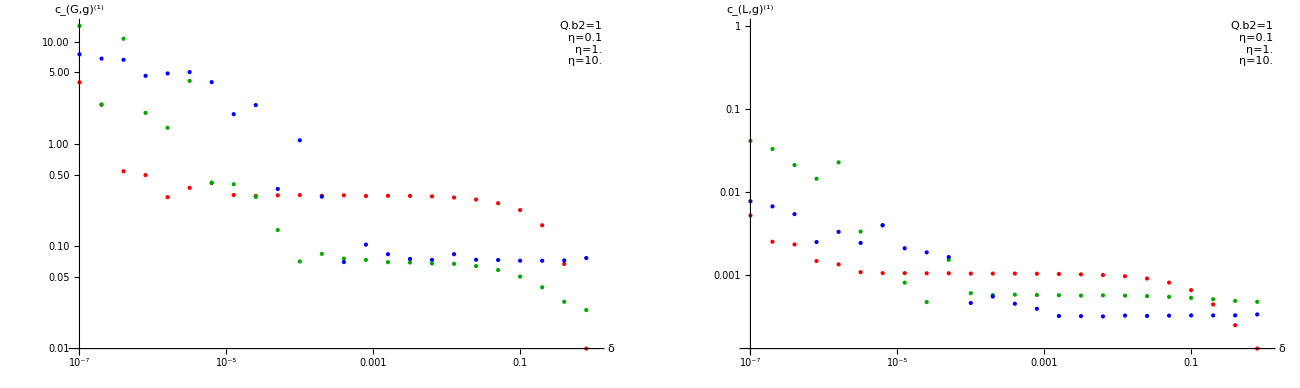

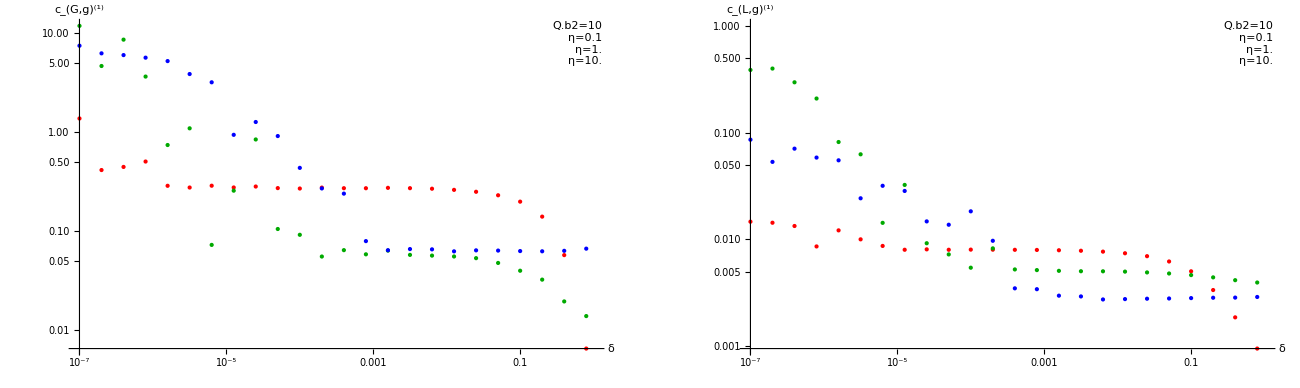

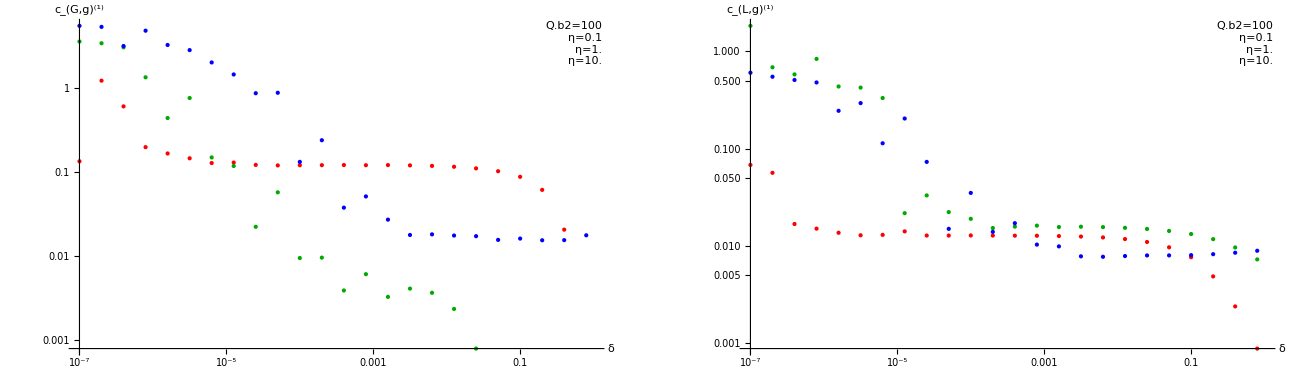

```mathematica
Module[{Q2s,ηs,m2V,δs,d,plt},
Q2s={1,10,100};
ηs=Table[10^k,{k,-1,1,1.}];
m2V=4.75^2;
δs=Table[10^k,{k,-7,0,.3}];
d=Get["~/Physik/PhD/MMa/data/c1g/deltaTest.m"];
plt[Q_]:=Module[{lG,lL,ins},
ins=Inset[Framed@Grid[{
{"Q.b2="<>ToString@Q},
{Text@Style["η="<>ToString@ηs[[1]],Red]},
{Text@Style["η="<>ToString@ηs[[2]],Darker@Green]},
{Text@Style["η="<>ToString@ηs[[3]],Blue]}
},Alignment->Left],Offset[{-2,-2},Scaled[{1,1}]],{Right,Top}];
lG=(η↦Table[{δ,({G,η,Q,δ}/.d)},{δ,δs}])/@ηs;
lL=(η↦Table[{δ,({L,η,Q,δ}/.d)},{δ,δs}])/@ηs;
Show[GraphicsRow[{
ListLogLogPlot[lG,PlotStyle-> {Red,Darker@Green,Blue},Epilog->ins,AxesLabel-> {"δ",Subsuperscript["c","G,g","(1)"]}],
ListLogLogPlot[lL,PlotStyle-> {Red,Darker@Green,Blue},Epilog->ins,AxesLabel-> {"δ",Subsuperscript["c","L,g","(1)"]}]
}],ImageSize-> 1300]
];

Print@plt[Q2s[[1]]];
Print@plt[Q2s[[2]]];
Print@plt[Q2s[[3]]];
]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00497882, 0.523606}. NIntegrate obtained -0.000201486 and 2.36877×10^-8 for the integral and error estimates.

2: {L,0.01,1} 27.0433

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00498508, 0.3903}. NIntegrate obtained -0.00152312 and 1.01407×10^-7 for the integral and error estimates.

1: {L,0.01,10} 55.52

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00486744, 0.594809}. NIntegrate obtained -1.76634 and 0.000125505 for the integral and error estimates.

7: {G,0.1,1} 67.15

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.810849 and 0.0000365432 for the integral and error estimates.

8: {G,0.01,1} 74.0833

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00488193, 0.568676}. NIntegrate obtained -0.00339639 and 2.59465×10^-7 for the integral and error estimates.

2: {L,0.1,1} 61.64

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00426376, 0.974152}. NIntegrate obtained -2.11255 and 0.000111578 for the integral and error estimates.

6: {G,1.,1} 105.53

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0153797, 0.0829785}. NIntegrate obtained -0.73761 and 0.0000815745 for the integral and error estimates.

8: {G,0.01,10} 50.5933

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.0262209 and 1.10727×10^-6 for the integral and error estimates.

1: {L,0.1,10} 88.6967

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -1.57396 and 0.0000578727 for the integral and error estimates.

7: {G,0.1,10} 93.84

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.0042674, 0.590396}. NIntegrate obtained -0.0785334 and 0.0000152262 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00426119, 0.944985}. NIntegrate obtained -1.88646 and 0.000276385 for the integral and error estimates.

8: {L,1.,10} 41.5233

6: {G,1.,10} 62.01

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00425533, 0.799986}. NIntegrate obtained -0.00912673 and 5.60224×10^-7 for the integral and error estimates.

2: {L,1.,1} 101.593

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -0.203088 and 0.0000560272 for the integral and error estimates.

5: {G,10.,1} 231.587

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.267139 and 0.000108176 for the integral and error estimates.

3: {G,100.,10} 326.793

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 19 recursive bisections in s4 near {s4, t1} = {0.00324968, 0.000961829}. NIntegrate obtained -0.203815 and 0.000121236 for the integral and error estimates.

5: {G,10.,10} 107.767

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.286691 and 0.000114768 for the integral and error estimates.

4: {G,100.,1} 356.89

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.0000918945 and 2.15×10^-7 for the integral and error estimates.

1: {L,10.,1} 413.613

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.000570361 and 1.51863×10^-6 for the integral and error estimates.

7: {L,10.,10} 407.07

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00067906 and 5.08954×10^-7 for the integral and error estimates.

8: {L,100.,1} 495.027

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 0.00597116 and 4.12896×10^-6 for the integral and error estimates.

6: {L,100.,10} 497.527

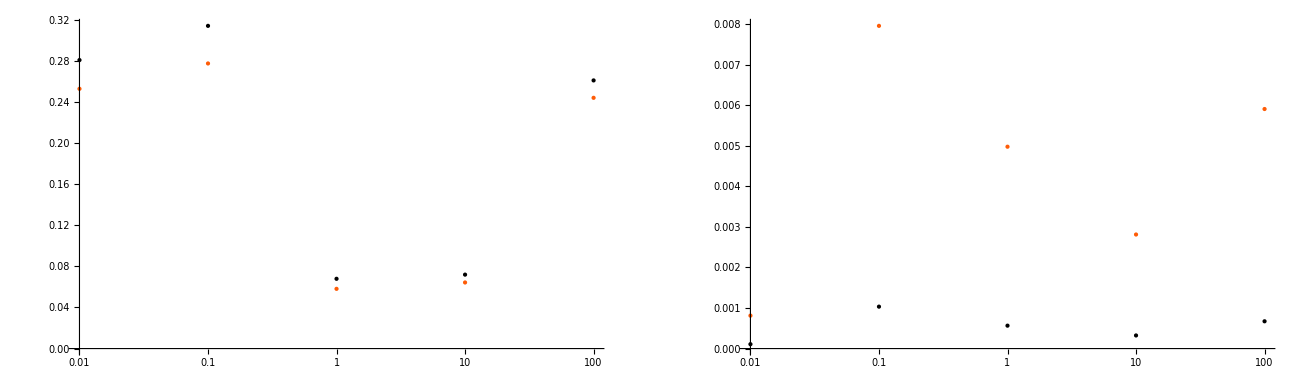

```mathematica
Module[{m2V,δ,Qs,ηs,ps,m,r,d,lLs,lGs,lTs,lPs},
m2V=4.75^2;
Qs=(*{1*^-2,1,10,100,1000}*){1,10};
ηs=Table[10^k,{k,-2,2,1.}];
ps=Tuples[{{G,L},ηs,Qs}];
m={};
SetSharedVariable[m];
(*ParallelDo[AppendTo[m,p-> c1g[p[[1]]][sOfη@p[[2]],p[[3]],m2V]],{p,ps}];*)
ParallelDo[
r=Timing[c1g[p[[1]]][sOfη@p[[2]],p[[3]],m2V]];
Print[$KernelID,": ",p," ",First@r];
AppendTo[m,p-> Last@r],{p,ps}];
d=Dispatch@m;
lGs=Table[{G,η,Q}/.d,{Q,Qs},{η,ηs}];
lLs=Table[{L,η,Q}/.d,{Q,Qs},{η,ηs}];
lTs=lGs+1/2lLs;
Show[GraphicsRow[{
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lTs],PlotRange-> {Full,Full},PlotStyle->ColorData[3,"ColorList"]],
ListLogLinearPlot[Evaluate[(l↦Transpose[{ηs,Re@l}])/@lLs],PlotRange-> {Full,Full},PlotStyle->ColorData[3,"ColorList"]]
}],ImageSize-> 1300]
]
```